Importing Dataset

```mathematica
dataset = Import["http://www-groups.dcs.st-and.ac.uk/history/Indexes/Full_Chron.html",{"Hyperlinks"}];
```

```mathematica
dataset1 =Flatten[StringCases[dataset,"http://www-groups.dcs.st-and.ac.uk/history/Biographies/"~~__]];
```

```mathematica
dataset2 = Import[#,"Text"]&/@dataset1
```

{6706,8997,7335,26071,13189,8342,33967,14134,17034,14494,2755,22932,25623,32677,25710,28993,20588,22485,15680,26426,25808}
 |  |  |  |

## HTML Parser

```mathematica
TemplateApply;

$mapping=Reverse[Normal[Templating`HTML`PackagePrivate`$SafeHTMLEntities],{2}];

htmlToText[txt_String]:=StringReplace[txt,$mapping]
```

```mathematica
htmls= Map[htmlToText,dataset2]
```

{6706,8997,7335,26071,13163,8342,33967,14134,17034,14494,2755,22907,25464,32564,25656,28923,20469,22478,15680,26396,25787}
 |  |  |  |

## Exporting List of HTMLs

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jofre/Documents/GitHub/KateSummer2018S/StudentDeliverables

```mathematica
Export["htmlbiographies.mx",htmls,"MX"]
```

htmlbiographies.mx

```mathematica
Export["listURLs.mx",dataset1,"MX"]
```

listURLs.mx

```mathematica
htmlList = Import["htmlbiographies.mx"]
```

{6706,8997,7335,26071,13163,8342,33967,14134,17034,14494,13304,28030,15557,14923,2747,18501,21861,14801,22484,22907,25464,32564,25656,28923,20469,22478,15680,26396,25787}
 |  |  |  |

```mathematica
Export["Biography1.m",dataset2]
```

```mathematica
bios =Import["htmlbiographies.mx"]
```

{6706,8997,7335,26071,13163,8342,33967,14134,17034,14494,13304,28030,2751,14801,22484,22907,25464,32564,25656,28923,20469,22478,15680,26396,25787}
 |  |  |  |

```mathematica
ClearAll[x]
```

```mathematica
fullNames =StringCases[htmlList,"<h1>"~~x__~~"</h1>"->x];
```

```mathematica
birthdate= StringCases[htmlList, "Born:<font color=\"green\"> "~~Shortest[y__]~~"<br>"->y]
```

{{about 1680 BC in Egypt},{about 800 BC in India},{about 750 BC in India},{about 624 BC in Miletus, Asia Minor (now Turkey)},{611 BC in Miletus near Söke, Turkey},{about 600 BC in India},{about 569 BC in Samos, Ionia},{about 520 BC in Shalatula (near Attock), now Pakistan},{499 BC in Clazomenae (30 km west of Izmir), Lydia (now Turkey)},{about 492 BC in Acragas (now Agrigento, Sicily, Italy)},{about 490 BC in Chios (now Khios), Greece},{about 490 BC in Elea, Lucania (now southern Italy)},{480 BC in (possibly) Athens, Greece},{about 480 BC in (possibly) Miletus, Asia Minor},{about 470 BC in Chios (now Khios), Greece},{465 BC in Cyrene (now Shahhat, Libya)},{about 460 BC in Abdera, Thrace, Greece},{about 460 BC in Elis, Peloponnese, Greece},{about 450 BC in Tarentum, Heraclea (now Taranto, Italy)},{about 428 BC in Tarentum, Magna Graecia (now Taranto, Italy)},{427 BC in Athens, Greece},{about 417 BC in Athens, Greece},{408 BC in Cnidus (on Resadiye peninsula), Asia Minor (now Knidos, Turkey)},{about 400 BC in China},{about 400 BC in Paros, Greece},{396 BC in Chalcedon (now Kadiköy, near Istanbul), Bithynia (now Turkey)},{about 390 BC in Greece},{387 BC in Heraclea Pontica (now Eregli, Turkey)},{384 BC in Stagirus, Macedonia, Greece},{about 380 BC in Alopeconnesus, Asia Minor (now Turkey)},{about 370 BC in Greece},{about 370 BC in Cyzicus, Asia Minor (now Turkey)},{about 360 BC in Pitane, Aeolis, Asia Minor (now Turkey)},{about 350 BC in Rhodes, Greece},{about 325 BC},{about 310 BC in Greece},{287 BC in Syracuse, Sicily (now Italy)},{280 BC in Soli, Cilicia, Asia Minor (now Soloi, Turkey)},{about 280 BC in Samos},{about 280 BC in Greece},{about 280 BC in Byzantium (Turkey)},{276 BC in Cyrene, North Africa (now Shahhat, Libya)},{about 262 BC in Perga, Pamphylia, Greek Ionia (now Murtina, Antalya, Turkey)},{about 250 BC in Caunus, Caria, Asia Minor (now in Turkey)},{about 240 BC in Carystus (now Káristos), Euboea (now Evvoia), Greece},{about 200 BC in India},{about 200 BC in Athens, Greece},{190 BC in Nicaea (now Iznik), Bithynia (now Turkey)},{about 190 BC in Alexandria, Egypt},{2nd century BC},{about 160 BC in Bithynia, Anatolia (now Turkey)},{about 150 BC in Sidon (now Saida in Lebanon)},{135 BC in Apameia, near Shaizar, Syria},{about 130 BC in Southwest China},{about 85 BC in possibly Fundi, Campania (now Italy)},{about 10 BC in (possibly) Rhodes, Greece},{1st century AD in possibly Lysimachia, Hellespont, Greece},{about AD 10 in (possibly) Alexandria, Egypt},{about 60 in Gerasa, Roman Syria (now Jarash, Jordan)},{about 70 in (possibly) Alexandria, Egypt},{about AD 70 in Smyrna (now Izmir), Turkey},{AD 78 in Nan-yang, China},{about AD 85 in Egypt},{about 120 in Western India},{129 in Lo-yang, China},{about 160 in Donglai, Shandong province, China},{about 200},{about 220 in Wei, China},{233 in Tyre (now Sur, Lebanon)},{about 240 in (possibly) Nicaea (now Iznik), Bithynia (now Turkey)},{about 290 in Alexandria, Egypt},{about 300 in Alexandria, Egypt},{about 300 in Antinoupolis, Egypt},{about 335 in (possibly) Alexandria, Egypt},{about 370 in Alexandria, Egypt},{about 400 in China},{about 400 in China},{8 February 411 in Constantinople (now Istanbul), Byzantium (now Turkey)},{about 420 in Larissa (now Shaizar), Syria},{429 in Jiankang, (now Nanking, Kiangsu province), China},{about 430 in China},{about 450 in Neapolis, Palestine (called Shechem in Bible, now Nablus, Israel)},{about 450 in Jiankang, (now Nanking, Kiangsu province), China},{about 474 in (possibly) Tralles (near Aydin in southwest Turkey)},{476 in Kusumapura (now Patna), India},{about 480 in in or near Rome, Byzantine Empire (now Italy)},{about 480 in Ascalon (now Ashqelon), Israel},{about 490 in Cilicia, Anatolia (now Turkey)},{about 500 in India},{505 in Kapitthaka, India},{about 580 in China},{598 in (possibly) Ujjain, India},{about 600 in (possibly) Saurastra (modern Gujarat state), India},{602 in Shaanxi province, China},{about 720 in India},{735 in York, Yorkshire, England},{about 780 in possibly Baghdad (now in Iraq)},{about 800 in possibly Baghdad, Iraq},{about 800 in Baghdad, (now in Iraq)},{about 800 in Baghdad, Iraq},{about 800 in India},{about 800 in possibly Mysore, India},{about 801 in Kufa, Iraq},{about 805 in Baghdad, Iraq},{808 in Al-Hirah (now in Iraq)},{about 810 in Baghdad, Iraq},{about 820 in Mahan, Kerman, Persia (now Iran)},{about 830 in India},{835 in Baghdad (now in Iraq)},{836 in Harran, Mesopotamia (now Turkey)},{about 840 in India},{about 850 in (possibly) Egypt },{about 850 in Harran (near Urfa), Mesopotamia (now Turkey)},{about 870 in possibly Bengal, India},{about 865 in possibly Nayriz, Iran},{about 880},{about 900 in Khurasan (eastern Iran)},{908 in   Baghdad, (now in Iraq)},{about 920 in possibly Damascus, Syria},{about 920 in India},{},{about 940 in Khudzhand, Tajikistan},{about 940 in Tabaristan (now Mazanderan), Persia (now Iran)},{about 940 in Benares (now Varanasi), India},{about 945 in Sijistan, Persia (now Iran)},{946 in Belliac, Auvergne, France},{950 in Egypt},{13 April 953 in Baghdad (now in Iraq)},{965 in   (possibly) Basra, Persia (now Iraq) },{970 in (possibly) Khwarazm (now Kara-Kalpakskaya, Uzbekistan)},{971 in Gilan (now in Iran)},{15 September 973 in Kath, Khwarazm (now Kara-Kalpakskaya, Uzbekistan)},{about 980 in Baghdad, Iraq},{980 in Kharmaithen (near Bukhara), Central Asia (now Uzbekistan)},{989 in Cordoba, Andalusia (now Spain)},{about 1010 in possibly Nasa, Khurasan,Iran},{about 1010 in China},{18 July 1013 in Saulgau, Swabia, Germany},{1019 in (probably) Rohinikhanda, Maharashtra, India},{1031 in Hangzhou, Zhejiang province, China},{18 May 1048 in Nishapur, Persia (now Iran)},{about 1060 in (possibly) Mathura, India},{1070 in Barcelona (now Spain)},{1075 in Bath, England},{1089 in Dhandhuka, Gujarat, India},{1092 in Tudela, Emirate of Saragossa (now Spain)},{about 1100 in possibly Seville (now Spain)},{1114 in Vijayapura, India},{1114 in Cremona (now Italy)},{about 1130 in Baghdad, Iraq},{about 1135 in Tus, Khorasan (now Iran)},{about 1140 in Paderborn, Roman Empire, now Germany},{1168 in Suffolk, England},{1170 in (probably) Pisa (now Italy)},{about 1175 in (probably) Northern England/Southern Scotland },{1192 in Ta-hsing (now Peking), China},{about 1195 in (possibly) Halifax, Yorkshire, England},{about 1200 in Lauingen an der Donau, Swabia (now Germany)},{18 February 1201 in Tus, Khorasan (now Iran)},{1202 in Puzhou (Anyue), Szechwan province, China},{1214 in Ilchester, Somerset, England},{about 1220 in Spain},{1220 in Novara (now Italy)},{1225 in Borgentreich (near Warburg), Germany},{1231 in Xingtai, Hebei province, China},{1235 in Majorca (now Spain)},{1236 in Marseilles, Spain (now France)},{about 1238 in Qiantang (now Hangzhou), Chekiang province, China},{about 1250 in Samarqand, Uzbekistan},{29 December 1256 in Marrakesh, Morocco},{about 1260},{about 1260 in Yan-shan, near Peking, China},{26 July 1271 in Poyang, now Jiangxi province, China},{1288 in Bagnols now Bagnols sur Cèze, Provence, France},{about 1288 in Ockham (near Ripley, Surrey), England},{about 1295 in Chichester, England},{1316 in Rickensdorf, Helmstedt, Lower Saxony (now Germany)},{about 1320 in possibly Damascus, Syria},{1323 in Allemagne (west of Riez), France},{about 1340 in Western India},{about 1340 in India},{1350 in Sangamagramma (near Cochin), Kerala, India},{1364 in Bursa, Turkey},{about 1370 in Alattur, Kerala, India},{1377 in Florence (now Italy)},{about 1380 in Kashan, Iran},{1393 in Soltaniyeh, Timurid, Persia (now Iran)},{about 1400 in possibly Andalusia (now Spain)},{1401 in Kues, Trier (now Germany)},{18 February 1404 in Genoa, French Empire (now Italy)},{1412 in   Bastah (now Baza, Spain)},{June 1420 in Borgo San Sepolcro (now Sansepolcro, Italy)},{30 May 1423 in Peuerbach, Austria},{about 1424 in Venice, Venetian States (now Italy)},{6 June 1436 in Unfinden (near Königsberg), Lower Franconia (now in Bayern, Germany)},{14 June 1444 in Trkkantiyur (near Tirur), Kerala, India},{1445

 in Paris, France},{1445 in Sansepolcro (now Italy)},{15 April 1452 in Vinci, near Empolia  (now Italy)},{1462 in Eger, Bohemia (now Cheb, Czech Republic)},{6 February 1465 in Bologna (now Italy)},{14 February 1468 in Nuremberg, Germany},{1469 in Gleghornie (near Haddington), Scotland},{about 1470 in Lyon, France},{1471 in Soyecourt, near Amiens, Picardy, France},{21 May 1471

 in Imperial Free City of Nürnberg (now in Germany)},{19 February 1473 in Toru&#324;, Poland},{1474 in Hackforth, Yorkshire, England},{1480 in Palencia (now Spain)},{1487 in Sarinena, Aragon (now Spain)},{1487 in Esslingen, Germany},{23 December 1492 in Staffelstein (near Bamberg), Upper Franconia (now Germany)},{20 December 1494 in Briançon, France},{16 September 1494 in Messina, Kingdom of Sicily (now Italy)},{16 April 1495 in Leisnig, Saxony (now Germany)},{1499 in Jauer, Silesia (now Jawor, Poland)},{about 1500 in Kerala, India},{1500 in Brescia, Republic of Venice (now Italy)},{24 September 1501 in Pavia, Duchy of Milan (now Italy)},{1502 in Alcácer do Sal, Portugal},{1506 in Urbino (now Italy)},{8 December 1508 in Dokkum, Friesland, The Netherlands},{1510 in Tenby, Wales},{5 March 1512 in Rupelmonde, Burgundian Netherlands (now Belgium)},{16 February 1514 in Feldkirch, Austria},{1515 in Cuts (near Noyon), Vermandois, France},{2 February 1522 in Bologna, Papal States (now Italy)},{January 1526 in Bologna, Papal States (now Italy)},{13 July 1527 in Tower Ward, London, England},{14 August 1530 in Venice, Venetian States (now Italy)},{1533 in China},{1 November 1535 in Vico Equense near Naples (now Italy)},{April 1536 in Perugia (now Italy)},{9 August 1537 in Candia (now Iráklion), Crete},{25 March 1538 in Bamberg (now in Germany)},{21 December 1540 in Uttoxeter, Staffordshire, England},{28 January 1540 in Hildesheim, Germany},{1540 in Fontenay-le-Comte, Poitou (now Vendée), France},{11 January 1545 in Pesaro (now Italy)},{14 December 1546 in Knutstorp, Skane, Denmark (now Svalöv, Sweden},{1546 in Wootton, Kent, England},{1546 in Breslau, now Wroc&#322;aw, Poland},{27 February 1547 in Baalbek, now in Lebanon},{1548 in Nola near Naples (now Italy)},{15 April 1548 in Bologna, Papal States (now Italy)},{1548 in Bruges, Burgundian Netherlands (now Belgium)},{30 November 1549 in Bradley (near Halifax), Yorkshire, England},{30 September 1550 in Göppingen, Baden-Würtemberg, Germany},{1550 in Merchiston Castle, Edinburgh, Scotland},{28 February 1552 in Lichtensteig, St Gallen, Switzerland},{6 October 1552 in Macerata, Papal States (now Italy)},{1552 in Naples (now Italy)},{ 1553 in Lagos, Portugal},{1555 in Lisbon, Portugal},{13 June 1555 in Padua, Venetian States (now Italy)},{1560 in Oxford, England},{February 1561 in Warleywood, Yorkshire, England},{6 January 1561 in Flensburg, Schleswig (now Germany)},{25 August 1561 in Ghent, Spanish Netherlands (now Belgium)},{24 August 1561 in Grünberg, Bohemia (now Zielona Góra, Poland)},{29 September 1561 in Leuven, Spanish Netherlands (now Belgium)},{24 April 1562 in Shanghai, China},{15 February 1564 in Pisa (now  Italy)},{8 March 1566 in Bologna, Papal States (now Italy)},{2 October 1568 in Ragusa, Dalmatia (now Dubrovnik, Croatia)},{27 December 1571

 in Weil der Stadt, Württemberg, Holy Roman Empire (now Germany)},{20 January 1573 in Gunzenhausen, Bavaria, Germany},{25 July 1573 in Markt Wald, near Mindelheim in Swabia (now in Germany)},{5 March 1574 in Eton, Buckinghamshire, England},{12 June 1577 in St Gall (now Sankt Gallen), Switzerland},{1578 in Brescia (now Italy)},{5 May 1580 in Ulm, Germany},{1580 in France},{13 June 1580 in Leiden, Netherlands},{9 October 1581 in Bourg-en-Bresse, France},{1581 in Hertfordshire, England},{23 February 1583 in Villefranche, Beaujolais, France},{8 September 1584 in Bruges, Spanish Netherlands (now Belgium)},{19 August 1584 in Ornans, Franche-Comté, Spanish Habsburgs (now France)},{1585 in Paris, France},{1586 in London, England},{22 October 1587 in Lübeck, Holstein (now Germany)},{15 February 1588 in Felsberg, Germany},{5 April 1588 in Westport, Malmesbury, Wiltshire, England},{8 September 1588 in Oizé, Maine, France},{2 May 1588 in Clermont (now Clermont-Ferrand), Auvergne, France},{about 1590 in Paris, France},{21 February 1591

 in Lyon, France},{22 January 1592 in Champtercier, Provence, France},{22 April 1592 in Herrenberg (near Tübingen), Württemberg (now Germany)},{8 December 1594 in Montluçon, France},{1595 in St Mihiel, France},{31 March 1596 in La Haye (now Descartes),Touraine, France},{1596 in The Hague, Holland},{17 November 1597 in Aldersgate, London, England},{1 March 1597 in Antwerp, Dutch Republic (now Belgium)},{1598 in Milan, Duchy of Milan, Habsburg Empire (now Italy)},{1598 in Le Mans, France},{17 April 1598 in Ferrara (now Italy)},{1600 in Lyon, France},{1600 in London, England},{1600 in Gouda, Netherlands},{7 October 1601 in Blois, France},{17 August 1601 in Beaumont-de-Lomagne, France},{18 March 1602 in Compiègne, France},{1602 in Alresford, Hampshire, England},{9 August 1602 in Noël-Saint-Martin, Villeneuve-sur-Verberie, Oise, France},{about 1604 in Paris, France},{28 September 1605 in Loudun, France},{23 May 1606 in Madrid, Spain},{about 1607 in Schweidnitz, Silesia (now &#346;widnica, Poland)},{28 January 1608 in Naples (now Italy)},{8 April 1608 in Le Grand Abergement, Ain, France},{15 October 1608 in Faenza, Romagna (now Italy)},{1610 in Paris, France},{1610 in Rotterdam, Netherlands},{28 January 1611 in Danzig, now Gda&#324;sk, Poland},{1 March 1611 in Southwick, Sussex, England},{6 February 1612 in Paris, France},{23 June 1612 in Antwerp, Dutch Republic (now Belgium)},{October 1614 in Grantham, Lincolnshire, England},{1614 in Fawsley (4 km S of Daventry), Northamptonshire, England},{15 May 1615 in Leiden, Netherlands},{about 1616 in Benares (now Varanasi), India},{23 November 1616 in Ashford, Kent, England},{1 April 1617 in Aspenden, Hertfordshire, England},{2 April 1618 in Bologna, Papal States (now Italy)},{1618 in Toxteth, Liverpool, England},{1618 in Lyon, France},{1618 in Paris, France},{30 January 1619 in Rome (now Italy)},{1620 in Castlelyons (N of Cork), Ireland},{1620 in Eutin, Holstein, Holy Roman Empire (now Germany)},{21 July 1620 in La Flèche, France},{1621 in Chambéry, France},{28 January 1622 in Rouen, France},{10 March 1622 in Zürich, Switzerland},{2 July 1622 in Visé, Spanish Netherlands (now Belgium)},{5 April 1622 in Florence (now Italy)},{21 September 1623 in Venice, Venetian States (now Italy)},{19 June 1623 in Clermont (now Clermont-Ferrand), Auvergne, France},{5 March 1624 in Wood Eaton (4km north of Oxford), England},{1624 in Modena (now Italy)},{10 June 1625 in Apáca, Transylvania, Hungary (now Romania)},{13 August 1625 in Roskilde, Denmark},{8 June 1625 in Perinaldo, Republic of Genoa (now Italy)},{24 September 1625 in Dordrecht, Netherlands},{1626 in Bologna, Papal States (now Italy)},{25 January 1627 in Lismore, County Waterford, Ireland},{8 February 1627 in Whitelee, Pendle Forest, Lancashire, England},{23 April 1628 in Amsterdam, Netherlands},{14 April 1629 in The Hague, Netherlands},{October 1630 in London, England},{1630 in France},{1631 in England},{20 October 1632 in East Knoyle, Wiltshire, England},{1633 in Xuangcheng, now Xuanzhou City, Anhui province, China},{8 September 1634 in Haarlem, Netherlands},{18 July 1635 in Freshwater, Isle of Wight, England},{16 December 1637 in Bishopsthorpe (near York), England},{November 1638 in Drumoak (near Aberdeen), Scotland},{6 August 1638 in Paris, France},{18 March 1640 in Paris, France},{15 June 1640 in Le Mans, France},{1 April 1640 in Copenhagen, Denmark},{16 June 1640 in Sainte-Olive, Bresse, France},{March 1642 in Fujioka, Kozuke, Japan},{4 January 1643 in Woolsthorpe, Lincolnshire, England},{20 August 1645 in Mexico City, Mexico},{19 August 1646 in Denby (near Derby), Derbyshire, England},{1 July 1646 in Leipzig, Saxony (now Germany)},{1 September 1647 in Milan, Hapsburg Empire (now Italy)},{17 January 1647 in Danzig, now Gda&#324;sk, Poland},{22 August 1647 in Blois, France},{15 January 1648 in Westminster, London, England},{20 December 1648 in Milan, Hapsburg Empire (now Italy)},{10 April 1651 in Kieslingswalde (near Görlitz), Germany (now S&#322;awnikowice, Poland)},{9 April 1652 in Lisieux, France},{21 April 1652 in Ambert, Basse-Auvergne, France},{1653 in Little Horton, near Bradford, Yorkshire, England},{1654 in Caen, France},{6 January 1655 in Basel, Switzerland},{8 November 1656 in Haggerston, Shoreditch (near London), England},{17 April 1656 in Dublin, Ireland},{11 June 1656 in Brissac, Maine-et-Loire, France},{11 February 1657 in Rouen, France},{3 June 1659 in Aberdeen, Scotland},{1 September 1659 in Courthézon, Vaucluse, France},{7 November 1660 in Lyon, France},{},{26 July 1663 in Colfontaine, near Nangis, Brie, France},{1663 in Hoddam, Dumfries, Scotland},{1664 in Edo (now Tokyo), Japan},{April 1667 in Inverbervie, Kincardine, Scotland},{27 July 1667 in Basel, Switzerland},{26 May 1667 in Vitry-le-François, Champagne, France},{5 September 1667 in San Remo, Genoa (now Italy)},{9 December 1667 in Norton-juxta-Twycross, Leicestershire, England},{1668 in Pinner, Middlesex, England},{9 June 1669 in Ostashkov, Russia},{25 February 1670 in Panitzsch, near Leipzig, Germany},{1 October 1671 in Cremona (now Italy)},{1 December 1671 in Edinburgh, Scotland},{20 September 1674 in Bologna, Papal States (now Italy)},{11 October 1675 in Norwich, England},{1675 in Llanfihangel Tre'r Beirdd, Anglesey, Wales},{28 May 1676 in Venice, Venetian Republic (now Italy)},{8 February 1677 in Paris, France},{27 September 1677  in Nuremberg, Germany},{1677 in Tarascon, Bouches-du-Rhône, France},{1678 in England},{16 July 1678 in Basel, Switzerland},{27 October 1678 in Paris, France},{1680 in Lichfield, Staffordshire, England},{1680 in England},{25 March 1681 in Bologna, Papal States (now Italy)},{19 May 1681 in Xuangcheng, now Xuanzhou City, Anhui province, China},{10 July 1682 in Burbage, Leicestershire, England},{6 December 1682 in Sinigaglia (now Senigallia, Italy)},{16 April 1682 in Bloomsbury, London, England},{January 1682 in Thurlstone, Yorkshire, England},{23 August 1683 in Venice, Venetian States (now Italy)},{12 March 1685 in Kilkenny, County Kilkenny, Ireland},{18 August 1685 in Edmonton, Middlesex, England},{21 October 1687 in Basel, Switzerland},{14 October 1687 in West Kilbride, Ayrshire, Scotland},{15 November 1688 in Montpellier, France},{not known},{26 September 1688 in 'sHertogenbosch, Netherlands},{18 July 1689 in Chester, Cheshire, England},{18 March 1690 in Königsberg, Brandenburg-Prussia (now Kaliningrad, Russia)},{about 1690 in Amber (now Jaipur), India},{May 1692 in Garden (near Stirling), Scotland},{6 February 1695 in Basel, Switzerland},{16 February 1698 in Le Croisic, France},{ February 1698 in Kilmodan (12 km N of Tighnabruaich), Cowal, Argyllshire, Scotland},{28 September 1698 in Saint Malo, France},{25 August 1699 in Crécy-en-Brie (near Paris), France},{8 February 1700 in Groningen, Netherlands},{28 November 1700 in Bisley, Gloucester, England},{1700},{about 1700 in Inverary, Scotland},{14 May 1701 in Hurworth, near Darlington, England},{28 January 1701 in Paris, France},{1702 in London, England},{28 October 1703 in Clotet-de-Cessous, France},{15 January 1708 in Castiglione, Tuscany (now Italy)},{31 July 1704 in Geneva, Switzerland},{13 August 1704 in Claveyson, Drôme, France},{9 October 1704 in Pozsony, Hungary (now Bratislava, Slovakia)},{17 December 1706 in Paris, France},{17 January 1706 in Boston, Massachusetts, British colony},{7 September 1707 in Montbard, Côte d'Or, France},{15 April 1707 in Basel, Switzerland},{11 January 1707 in Castelfranco Veneto near Treviso (now Italy)},{1707 in Bath, England},{28 May 1710 in Basel, Switzerland},{1710 in West Africa},{20 August 1710 in Market Bosworth, Leicestershire, England},{31 October 1711 in Bologna, Papal States (now Italy)},{18 May 1711 in Ragusa, Dubrovnik Republic (now Dubrovnik, Croatia)},{31 July 1712 in Büdingen, Germany},{7 May 1713 in Paris, France},{17 June 1714 in Thury, near Clermont, Oise, France},{1714 in St Andrews, Scotland},{31 January 1715 in Sinigaglia (now Senigallia, Italy)},{},{15 January 1717 in Rothesay, Isle of Bute, Scotland},{16 May 1718 in Milan, Habsburg Empire (now Italy)},{1718 in Rimaszombat, Hungary (now Rimavská Sobota, Slovakia)},{27 September 1719 in Leipzig, Germany},{23 January 1719 in Peakirk (near Peterborough), England},{5 January 1723 in Paris, France},{17 February 1723 in Marbach, Württemberg, Germany},{23 February 1723 in Tyn-ton, Llangeinor, Glamorgan, Wales},{13 December 1724 in Rostock, Mecklenberg-Schwerin (now Germany)},{27 September 1725 in Kiltullagh near Athenry, County Galway, Ireland},{5 September 1725 in Lyon, France},{3 June 1726 in Edinburgh, Scotland},{13 April 1728 in Milan, Austrian Habsburg (now Italy)},{26 August 1728 in Mülhausen, Alsace (now Mulhouse, France)},{11 November 1729 in Paris, France},{31 March 1730 in Nemours, France},{11 August 1730 in Tartaras (near Rive de Gier), Rhône-et-Loire, France},{9 November 1731 in Baltimore, Maryland, USA},{26 September 1731 in Ala, Trento (now Italy)},{15 December 1731 in London, England},{1732 in Shiba, Edo (now Tokyo), Japan},{15 December 1732 in Neubrandenburg, Mecklenburg-Strelitz, Germany},{11 July 1732 in Bourg-en-Bresse, Ain, France},{5 October 1732 in Kensington Gore, London, England},{8 April 1732 in Paper Mill Run, near Germantown, Pennsylvania, USA},{4 May 1733 in Dax, France},{11 January 1734 in Paris, France},{25 June 1734 in Canaveses, Portugal},{18 October 1735 in Cerea (now Italy)},{15 October 1735 in Salterhebble, near Halifax, Yorkshire, England},{28 February 1735 in Paris, France},{19 August 1736 in Ausas, Kristianstad, Sweden},{14 June 1736 in Angoulême, France},{25 January 1736 in Turin, Sardinia-Piedmont (now Italy)},{16 September 1736 in Tetenbüll (near Tönning), South Schleswig (now Germany)},{1736 in Old Heath (near Shrewsbury), Shropshire, England},{14 August 1737 in Newcastle-upon-Tyne, England},{12 June 1737 in Ferryport-on-Tay, now Tayport, Scotland},{15 November 1738 in Hanover, Electorate of Holy Roman Empire (now Germany)},{19 August 1739 in Hamburg, Germany},{24 December 1740 in Äbo, Sweden (now Turku, Finland)},{13 July 1741 in Dresden, Germany},{6 August 1741 in Applethwaite, Westmoreland, England},{17 September 1743 in Ribemont, France},{4 November 1744 in Basel, Switzerland},{1744 in Lisbon, Portugal},{16 August 1744 in Laon, France},{October 1745 in Westminster, London, England},{8 June 1745 in Vestby (near Dröbak), Norway},{9 May 1746 in Beaune, Bourgogne, France},{23 June 1746 in Logie, near Montrose, Scotland},{10 February 1747 in  Yamagata, Japan},{30 June 1748 in Paris, France},{10 March 1748 in Benvie (near Dundee), Scotland},{19 April 1748 in Besançon, France},{19 September 1749 in Amiens, France},{1749 in North Tawton, Devon, England},{23 March 1749 in Beaumont-en-Auge, Normandy, France},{October 1750 in Leslie, Fife, Scotland},{16 March 1750 in Hannover, Hanover (now Germany)},{24 April 1750 in Geneva, Switzerland},{13 May 1750 in Bergamo, Lombardo-Veneto (now Italy)},{26 May 1750 in Bridgend, Wales},{29 December 1751 in Hardwick, Buckinghamshire, England},{18 September 1752 in Paris, France},{13 May 1753 in Nolay, Burgundy, France},{29 October 1753 in Naples, Kingdom of Naples (now Italy)},{22 November 1753 in Edinburgh, Scotland},{October 1753 in Corney, Cumberland, England},{2 December 1754 in Sézanne, Haute Marne, France},{23 March 1754 in Zagorica, Ljubljana, Austrian Empire (now Slovenia)},{22 July 1755 in Chamelet, Beaujolais, France},{30 January 1755 in Basel, Switzerland},{27 April 1755 in Rosières-aux-Salines, France},{10 April 1756 in Logie (near St Andrews), Scotland},{4 October 1759 in Mutzig, Alsace},{17 October 1759 in Basel, Switzerland},{2 March 1759 in Livorno (now Italy)},{8 July 1760 in Strasbourg, France},{ 28 September 1761 in Limonade, Cap-Français, Saint-Domingue (now Haiti)},{21 February 1764 in Yangzhou, Jiangsu province, China},{4 November 1765 in Caen, France},{17 February 1765 in Dundee, Scotland},{28 April 1765 in Paris, France},{2 February 1765 in Osipovo, Vladimir gubernia, Russia},{22 December 1765 in Stuttgart, Württemberg (now Germany)},{22 September 1765 in Valentano, Papal States (now Italy)},{July 1766 in Woodbridge, Suffolk, England},{1766 in Woburn, Bedfordshire, England},{17 April 1766 in Largo, Fife, Scotland},{27 June 1767 in Contamines, Haute-Savoie, France},{18 July 1768 in Geneva, Switzerland},{21 March 1768 in Auxerre, Bourgogne, France},{7 April 1768 in Saverne, Bas-Rhin, France},{1768 in Paris, France},{8 December 1768 in Yuanhe (now Suzhou, Jiangsu province), China},{1 September 1768 in Modena, Duchy of Modena and Reggio (now Italy)},{19 July 1768 in Mont-de-Laval (N of Morteau), Doubs, France},{23 September 1768 in Dysart, Scotland},{12 August 1769 in Brunswick, Brunswick-Lüneburg, Germany},{20 November 1769 in Astalonga, San Giuseppe d'Ottajano, Kingdom of Naples (now San Giuseppe Vesuviano,  Italy},{6 May 1769 in Mézières, Ardennes, France},{22 September 1769 in Champagne, France},{19 June 1771 in Nancy, France},{12 September 1771 in Paris, France},{ 27 January 1772 in Overton, Lecropt, Perthshire, Scotland},{5 February 1772 in New Ross, County Wexford, Ireland},{26 March 1773 in Salem, Massachusetts, USA},{30 April 1773 in Leipzig, Saxony, now Germany},{16 August 1773 in Paris, France},{28 April 1773 in Norwich, England},{13 June 1773 in Milverton, Somerset, England},{21 April 1774 in Paris, France},{29 January 1774 in Yaxley, Huntingdonshire (now Cambridgeshire), England},{3 February 1774 in Wolfenbüttel, Brunswick, now Germany},{30 September 1775 in Carrickfergus, Ireland},{20 January 1775 in Lyon, France},{9 February 1775 in Bolya (near Nagyszeben), Transylvania, Hungary },{20 June 1775 in Saverne, Bas-Rhin, France},{23 July 1775 in Paris, France},{15 October 1776 in Norwich, England},{1 April 1776

 in Paris, France},{11 October 1777 in Lyon, France},{30 April 1777

 in Brunswick, Duchy of Brunswick (now Germany)},{8 July 1777 in Sosa (near Eibenstock), Saxony (now Germany)},{3 January 1777 in Paris, France},{31 July 1777 in Greenock, Scotland},{23 August 1778 in Wolsztyn, Poland},{5 March 1779 in London, England},{11 March 1780 in Eichwerder, (near Wriezen) Prussia (now Germany)},{26 December 1780 in   Jedburgh, Roxburghshire, Scotland},{19 January 1781 in Rosano, Casalnoceto, Tortona, Piedmont, now Italy},{5 October 1781 in Prague, Bohemia, Austrian Habsburg domain (now Czech Republic)},{6 November 1781 in Voghera (now Italy)},{21 June 1781 in Pithiviers, France},{4 April 1782 in Naples, Kingdom of Naples (now Italy)},{19 December 1783 in Sèvres, France},{25 November 1783 in Mâcon, France},{22 July 1784 in Minden, Westphalia (now Germany)},{6 October 1784 in Varzy, France},{10 February 1785 in Dijon, France},{26 February 1786 in Estagel, Roussillon, France},{2 February 1786 in Rennes, Bretagne, France},{1786 in Bristol, England},{29 July 1786 in Cluses, Savoy, France},{13 November 1786 in Annaghmore, near Ballynahinch, Co. Down, Ireland},{1786 in Shandrum, County Limerick, Ireland},{25 August 1787 in Port-au-Prince, Saint-Domingue, now Haiti},{3 January 1788 in Eilsum, Frisia, Germany},{10 May 1788 in Broglie, France},{8 March 1788 in Glasgow, Scotland},{1 July 1788 in Metz, Lorraine, France},{20 July 1789 in Mezzana Corti, now Cava Manara, Savoy,

Mezzana Corti, now Cava Manara, Savoy, Italy},{21 August 1789 in Paris, France},{16 March 1789 in Erlangen, Bavaria (now Germany)},{4 April 1790 in Valenciennes, France},{17 November 1790 in Schulpforta, Saxony (now Germany)},{26 July 1790 in South Hadley, Massachusetts, USA},{19 September 1790 in Cuddalore, Tamil Nadu, India},{26 December 1791 in London, England},{22 September 1791 in Newington Butts, Surrey (now London) England},{2 October 1791 in Grandvilliers, Oise, France},{possibly 1791 in Valay, Haute-Sâone, France},{9 April 1791 in Thornton Hall, Denton, County Durham, England},{2 October 1791 in Vesoul, Haute-Saône, France},{30 June 1791 in  Mézières, France},{21 May 1792 in Paris, France},{7 March 1792 in Slough, Buckinghamshire, England},{1 December 1792 in Nizhny Novgorod (was Gorky from 1932-1990), Russia},{6 May 1792 in Erlangen, Bavaria (now Germany)},{15 November 1793 in Epernon, France},{July 1793 in Sneinton, Nottingham, England},{2 February 1793 in Kingston-on-Soar, Derbyshire, England},{1 May 1793 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{21 January 1793 in France},{12 April 1794 in Le Bourget, near Paris, France},{15 November 1794 in Bad König, German},{24 May 1794 in Lancaster, Lancashire, England},{4 December 1795 in Ecclefechan, Dumfriesshire, Scotland},{23 March 1795 in Vang, Valdres, Oppland, Norway},{22 July 1795 in Tours, France},{15 August 1795 in Lagrange-aux-Bois, France},{19 October 1795 in Paris, France},{31 March 1795 in Rennes, France},{6 October 1795 in Bordeaux, France},{9 January 1795 in Marylebone, London, England},{28 August 1796 in Paris, France},{14 June 1796 in Rassnova: near Brünn, Austria-Hungary (now Brno, Czech Republic)},{1 June 1796 in Paris, France},{22 February 1796 in Ghent, French Empire, (now Belgium)},{18 March 1796 in Utzenstorf, Switzerland},{5 February 1797 in St Malo, France},{15 October 1797 in Lauterbourg, France},{23 August 1797 in Villiers-en-Bière, Seine-et-Marne, France},{4 October 1797 in Paris, France},{17 April 1798 in Lons-le-Saulnier, France},{25 March 1798 in Vienenburg (near Hildesheim), Germany},{11 September 1798 in Joachimsthal, Germany (now Jachymov, Czech Republic)},{27 October 1798 in Posen, Prussia (now Pozna&#324;, Poland)},{24 January 1798 in Imperial Free City of Rothenburg (now Rothenburg ob der Tauber, Germany)},{26 February 1799 in Paris, France},{7 November 1799 in Brunswick, Germany},{30 May 1800 in Jena, Germany},{31 March 1800 in Mitcham, Surrey, England},{16 April 1800 in Dublin, Ireland},{11 February 1800 in Melbury Sampford, Dorset, England},{27 July 1801 in Alnwick, Northumberland, England},{16 January 1801 in Snogbaek, Denmark},{28 August 1801 in Gray, France},{24 September 1801 in Pashennaya (now Poltava oblast), Ukraine},{14 October 1801 in Brussels, French Empire (now Belgium)},{16 July 1801 in Elberfeld (now Wuppertal), Duchy of Berg (now Germany)},{15 May 1801 in Brody, Galicia (now Ukraine)},{5 August 1802 in Frindöe (near Stavanger), Norway},{15 December 1802 in Kolozsvár, Hungary (now Cluj, Romania)},{21 June 1802 in Esch-sur-Alzette, French Empire (now Luxembourg)},{22 November 1803 in Bassano, Vicenza (now Italy)},{29 November 1803 in Salzburg, Austria},{1 January 1803 in Florence, Italy},{28 February 1803 in Stuttgart, Germany},{29 September 1803 in Geneva, Switzerland},{16 December 1804 in Bar, Podolskaya gubernia (now Vinnitsa oblast), Ukraine},{10 December 1804 in Potsdam, Prussia (now Germany)},{25 November 1804 in Bodmin, Cornwall, England},{28 October 1804 in Brussels, French Empire (now Belgium)},{4 October 1804 in Wittenberg, Saxony (now Germany)},{13 February 1805 in Düren, French Empire (now Germany)},{4 August 1805 in Dublin, Ireland},{30 January 1805 in Kirkcaldy, Fife, Scotland},{25 August 1806 in Lavagh, County Leitrim, Ireland},{27 June 1806

 in Madura, Madras Presidency, India (now Madurai, Tamil Nadu, India)},{4 December 1806 in Dublin, Ireland},{31 March 1806 in Bolton (near Manchester), England},{23 January 1806 in Kalisz, Russian Empire (now Poland)},{1806 in Mallow, Cork County, Ireland},{10 August 1806 in Mittelschmiedeberg (near Annaberg), Germany},{6 January 1807 in Spisská Belá, Hungary (now in Slovakia)},{29 June 1807 in Frankfurt am Main, Germany},{28 December 1808 in Cerisiers, France},{1808 in Dunster, Somerset, England},{25 July 1808 in Frankfurt am Main, Germany},{9 May 1808 in Parkhead, near Glasgow, Scotland},{15 April 1809 in Stettin, Prussia (now Szczecin, Poland)},{24 March 1809 in Saint-Omer, France},{1809 in Landahussy (near Strabane), Ireland},{4 September 1809 in Chambéry, Savoy, France},{4 April 1809 in Salem, Massachusetts, USA},{4 June 1809 in St Mary Woolnoth, London, England},{31 July 1810 in Avoca, County Wicklow, Ireland},{29 January 1810 in Sorau, Brandenburg, Prussia (now Germany)},{25 October 1811

 in Bourg La Reine (near Paris), France},{14 March 1811 in Limerick, Ireland},{22 April 1811 in Königsberg, Prussia (now Kaliningrad, Russia)},{11 March 1811 in Saint-Lô, France},{1811 in Haining, Zhejiang Province, China},{1811 in Edinburgh, Scotland},{29 September 1812 in Rostock, Germany},{6 December 1812 in Dublin, Ireland},{25 January 1812 in Corsenside (8 km NE of Bellingham), Northumberland, England},{9 April 1813 in Madeley, Shropshire, England},{13 April 1813 in Edinburgh, Scotland},{18 July 1813 in Paris, France},{30 May 1814 in Bruges, French Empire (now Belgium)},{24 January 1814 in St Austell, Cornwall, England},{16 May 1814 in Lisbon, Portugal},{1 October 1814 in Cerkno, Austrian Empire (now Slovenia)},{1814 in Ennis, County Clare, Ireland},{20 April 1814 in Pisa (now Italy)},{15 January 1814 in Grasswil, Bern, Switzerland},{3 September 1814 in London, England},{5 June 1814 in Paris, France},{2 November 1815 in Lincoln, Lincolnshire, England},{10 December 1815 in Piccadilly, Middlesex (now in London), England},{1 June 1815 in Otrada, Moscow gubernia (now oblast), Russia},{31 October 1815 in Ostenfelde, Westphalia (now Germany)},{9 April 1816 in Lusigny-sur-Barse, France},{7 February 1816 in Périgueux, France},{10 June 1816 in Königsberg, Prussia (now Kaliningrad, Russia)},{7 July 1816 in  Fällanden (near Zürich), Switzerland},{22 February 1817 in Berlin, Germany},{19 July 1817 in St Hippolyte, Doubs, Franche-Comté, France},{29 January 1817 in Bedford (now Fulton) County, Pennsylvania, USA},{5 March 1817 in Piacenza, Habsburg Empire (now Italy)},{4 January 1818 in Fredrikstad, Norway},{10 March 1818 in Hilltown, Bucks county, Pennsylvania, USA},{9 March 1818 in Goldberg, Prussian Silesia (now Z&#322;otoryja, Poland)},{5 June 1819 in Lidcott, near Launceston, Cornwall, England},{16 July 1819 in Angerburg, East Prussia (now W&#281;gorzewo, Poland)},{22 December 1819 in Montpellier, France},{7 September 1819 in Morteau, Doubs, France},{14 January 1819 in Great Oakley, Essex, England},{23 September 1819 in Paris, France},{18 September 1819 in Paris, France},{25 September 1819 in Dublin, Ireland},{30 August 1819 in Paris, France},{13 August 1819 in Skreen, County Sligo, Ireland},{12 May 1820 in Coolattin, Kilbehenny, Co. Limerick, Ireland},{24 May 1820 in Milford, Pennsylvania, USA},{3 July 1820 in Carpentras, France},{12 May 1820 in Florence (now Italy)},{16 April 1820 in Argenteuil, Val-d'Oise, France},{5 July 1820 in Edinburgh, Scotland},{23 November 1820 in Rye, Sussex, England},{16 August 1821 in Richmond, Surrey, England},{16 May 1821 in Okatovo, Kaluga Region, Russia},{21 December 1821 in Carlow, Ireland},{16 March 1821 in Berlin, Germany},{31 August 1821 in Potsdam, Prussia (now  Germany)},{1821 in Panipat, India},{24 October 1821 in Zweibrücken, Germany},{11 March 1822 in Paris, France},{2 January 1822 in Koslin, Prussia (now Koszalin, Poland)},{16 February 1822 in Sparkbrook (near Birmingham), England},{24 December 1822 in Dieuze, Lorraine, France},{4 March 1822 in Versailles, France},{22 September 1822 in Kinghorn, Fife, Scotland},{16 November 1823 in Stalden bei Brugg, Switzerland},{21 October 1823 in Pistoia, Tuscany (now Italy)},{2 July 1823 in Craigflower, Fife, Scotland},{15 December 1823 in Libav, Russia (now Liepaja, Latvia)},{16 April 1823 in Berlin, Germany},{7 April 1823 in Thaon, Calvados, France},{7 December 1823 in Liegnitz, Prussia (now Legnica, Poland)},{13 April 1823 in Weimar, Germany},{28 September 1824 in Dublin, Ireland},{22 December 1824 in Milan, Lombardo-Veneto (now Italy)},{7 March 1824 in Lodi (now Italy)},{23 June 1824 in Hamburg, Germany},{12 March 1824 in Königsberg, Prussia (now Kaliningrad, Russia)},{26 June 1824 in Belfast, Ireland},{1 May 1825 in Lausen, Basel-Land, Switzerland},{24 October 1825 in  Christiania (now Oslo), Norway},{29 March 1825 in Alessandria, Piemonte (now Italy)},{11 January 1825 in London, England},{12 November 1825 in Maliivka, Zolotonosha, Poltava, Ukraine},{2 October 1825 in Kennington, Surrey, England},{11 January 1826 in Naples, Kingdom of Naples and Sicily (now Italy)},{27 June 1826 in Dublin, Ireland},{31 July 1826 in Neustadt-Eberswalde, Brandenburg, Prussia (now Germany)},{17 September 1826 in Breselenz, Hanover (now Germany)},{2 November 1826 in Dublin, Ireland},{7 December 1826 in Darmstadt, Germany},{30 August 1827 in Buda, Hungary},{20 October 1827 in Southwark, London, England},{15 December 1827 in Horncastle, Lincolnshire, England},{25 February 1827 in Marylebone, London, England},{21 June 1828 in Mondovi (now Italy)},{25 May 1828 in Riga, Russia (now Latvia)},{23 August 1829 in Mannheim, Baden (now Germany)},{10 November 1829 in Montjoie Aachen (now Monschau), Germany},{8 July 1829 in Airdrie, Lanarkshire, Scotland},{11 August 1829 in Prinknash Park, Upton St Leonards, Gloucestershire, England},{8 January 1829 in Königsberg, Prussia (now Kaliningrad, Russia)},{30 September 1829 in Eccles (near Manchester), England},{7 December 1830 in Pavia, Lombardy (now Italy)},{22 April 1830 in Heckmondwike, Yorkshire, England},{29 March 1830 in London, England},{21 March 1831 in London, England},{6 October 1831 in Braunschweig, duchy of Braunschweig (now Germany)},{2 December 1831 in Berlin, Germany},{17 July 1831 in Paris, France},{13 June 1831 in Edinburgh, Scotland},{20 January 1831 in   Quebec, Canada},{31 August 1831 in Zug, Switzerland},{28 April 1831 in Dalkeith, Midlothian, Scotland},{11 March 1832 in Wickwar, Gloucestershire, England},{19 May 1832 in Gray, Haute-Saône, France},{27 January 1832 in Daresbury, England},{3 April 1832 in Chemnitz, Saxony, Germany},{14 May 1832 in Königsberg, East Prussia (now Kaliningrad, Russia)},{7 May 1832 in Königsberg, Germany (now Kaliningrad, Russia)},{18 August 1832 in Sommières, Occitanie, Languedoc, France},{12 December 1832 in Christiania (now Oslo), Norway},{26 April 1832 in Walworth, Surrey, England},{10 April 1832 in Darmstadt-Bessungen, Darmstadt, Grand Duchy of Hesse, now Germany},{19 January 1833 in Königsberg, East Prussia (now Kaliningrad, Russia)},{28 September 1833 in Bourbonne-les-Bains, Haute-Marne, France},{11 December 1833 in Venlo, Belgium (now Netherlands)},{5 May 1833 in Moschin (near Posen), Prussia (now Pozna&#324;, Poland)},{27 June 1834 in Watertown, Connecticut, USA},{29 May 1834 in Stewarton, Ayrshire, Scotland},{9 April 1834 in Bar-le-Duc, France},{4 August 1834 in Hull, England},{3 April 1835 in Philadelphia, Pennsylvania, USA},{16 November 1835 in Cremona, Lombardy, Austrian Empire (now Italy)},{17 December 1835 in Pavia (now Italy)},{1 September 1835 in Liverpool, England},{3 August 1835 in Steuben County, New York, USA},{15 May 1835 in Metz, France},{12 November 1835 in Chalon-sur-Saône, France},{1835 in England},{12 March 1835 in Wallace, Nova Scotia, Canada},{24 August 1835 in Dublin, Ireland},{24 March 1835 in St Peter (near Klagenfurt), Austria},{2 March 1836 in Berlin, Germany},{22 June 1837 in Berlin, Germany},{22 November 1837 in Hottingen, Zürich, Switzerland},{14 September 1837 in Dusheti (near Tiflis, now Tbilisi), Georgia},{27 April 1837 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{15 October 1837 in Posen, Prussia (now Pozna&#324;, Poland)},{19 February 1837 in Zhidovinovo, Tot'ma, Vologda, Russia},{17 July 1837 in Eschweiler (near Aachen), Germany},{11 January 1837 in Strontian, Argyllshire, Scotland},{16 August 1837 in Ypres, Belgium},{20 December 1838 in Marylebone, Middlesex, England},{10 April 1838 in New Hartford, Connecticut, USA},{3 March 1838 in New York, USA},{28 April 1838 in Pest, Hungary},{5 January 1838 in La Croix-Rousse, Lyon, France},{20 June 1838 in Ritzebüttel, near Cuxhaven, Germany},{24 December 1838 in Copenhagen, Denmark},{18 March 1839 in St Hilaire-Cottes, Pas-de-Calais, France},{May 1839 in Newcastle, England},{11 February 1839 in New Haven, Connecticut, USA},{14 February 1839 in Halle, Germany},{15 February 1839 in Leipzig, Germany},{10 September 1839 in Cambridge, Massachusetts, USA},{16 June 1839 in Soro, Denmark},{9 December 1839 in Dresden, Germany},{20 April 1839 in Rome (now Italy)},{15 February 1839 in Grimstrup, West Jutland, Denmark},{23 January 1840 in Eisenach, Grand Duchy of Saxe-Weimar-Eisenach (now in Germany)},{1 July 1840 in Dublin, Ireland},{ 9 March 1840 in Meldorf, Holstein (now Germany)},{22 November 1840 in Quimper, Finistère, France},{19 September 1840 in Carlisle, Pennsylvania , USA},{20 March 1840 in Schroda, Posen, Prussia (now &#346;roda Wielkopolska, Poland)},{30 October 1840 in Luxembourg City, Luxembourg},{4 May 1840 in Töss, Zürich canton, Switzerland},{11 December 1840 in Laucha (Unstrut), Germany},{23 June 1841 in Owego, Tioga County, New York,USA},{2 September 1841 in Echternach, Luxembourg},{31 January 1841 in   Philadelphia, Pennsylvania , USA},{25 November 1841 in Mannheim, Germany},{6 January 1841 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{9 November 1842 in Chivasso, Turin, Kingdom of Sardinia (now Italy)},{13 March 1842 in Saint-André de Sangonis, Hérault, France},{20 September 1842 in Darmstadt, Germany},{10 February 1842 in Skibbereen, Co. Cork, Ireland},{14 August 1842 in Nimes, Gard, Languedoc, France},{},{17 December 1842 in Nordfjordeide, Norway},{4 April 1842 in   Amiens, France},{24 March 1842 in Peterhead, Scotland},{12 November 1842 in Langford Grove (near Maldon), Essex, England},{23 August 1842 in Belfast, Ireland},{16 August 1842 in Brody, Austria-Hungary (now Ukraine)},{2 February 1842 in Warsaw, Poland},{3 May 1842 in Hall (now Solbad Hall in Tirol), Austria},{2 July 1842 in Forgue near Huntly, Scotland},{5 March 1842 in Heidelberg, Germany},{4 August 1843 in Handog, Lit Parish, Jämtland Province, Sweden},{26 February 1843 in Langenthal, Bern, Switzerland},{22 October 1843 in Auchencairn near Kirkcudbright, Kirkcudbrightshire, Scotland},{8 November 1843 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{25 January 1843 in Hermsdorf, Silesia (now Poland)},{2 January 1843 in Balgonie, Fife, Scotland},{20 December 1843 in Mantes-la-Jolie, Yvelines, France},{27 September 1843 in Villefranche-de-Rouergue, Aveyron, France},{7 November 1843 in Magdala, Thuringia, Germany},{20 February 1844 in Vienna, Austria},{30 October 1844 in Rouen, France},{18 February 1844 in Mannheim, Germany},{3 June 1844 in Belle-Maison, Marchin, near Huy, Belgium},{25 August 1844 in Stonebyres, Falls of Clyde, Lanarkshire, Scotland},{24 September 1844 in Mannheim, Baden, Germany},{27 July 1844 in Kotterbach, Zips district, Austro-Hungary (now Rudnany, Slovakia)},{18 November 1844 in Greiffenberg, Prussia, Germany},{11 January 1845 in Väsby, Malmöhus County, Sweden},{12 May 1845 in Vignot (part of Commercy), France},{3 March 1845 in St Petersburg, Russia},{4 May 1845 in Exeter, Devon, England},{9 July 1845 in Downe, Kent, England},{14 November 1845 in Pisa (now Italy)},{8 February 1845 in Edgeworthstown, County Longford, Ireland},{7 July 1845 in Wila, Zürich canton, Switzerland},{11 December 1845 in Kolodeje, Pardubice, Czech Republic},{14 September 1845 in Peterhead, Scotland},{13 January 1845 in Nuits-St-Georges, Côte-d'Or, France},{8 November 1846 in Forli (now  Italy)},{19 April 1846 in Millsboro, Washington County, Pennsylvania, USA},{16 March 1846 in Stockholm, Sweden},{30 June 1846 in Halle, Germany},{15 October 1846 in Elisavetgrad (now Kirovograd), Ukraine},{9 November 1846 in Nagykörös, Hungary},{21 January 1846 in Wormerveer, Netherlands},{24 August 1846 in Rush Creek Township, Fairfield County, Ohio, USA},{6 March 1847 in Santo Stefano di Magra, La Spezia (now Italy)},{9 November 1847 in Asti, Piemonte (now Italy)},{28 March 1847 in Sárosd, Fejér County, Hungary},{15 December 1847 in Épinal, France},{2 July 1847 in Lochgelly, Fife, Scotland},{29 November 1847 in Twickenham, London, England},{10 May 1847 in Burbach (near Siegen), Westphalia, Germany},{1 December 1847 in Windsor, Connecticut, USA},{10 December 1847 in Yorkshire Centre, now Delevan, Cattaraugus County, New York, USA},{21 November 1847 in Montrose, Angus, Scotland},{17 January 1847 in Orekhovo, Vladimir gubernia, Russia},{12 April 1847 in St Petersburg, Russia},{26 March 1848 in Moscow, Russia},{4 September 1848 in Berlin, Germany},{27 July 1848 in Pest (now part of Budapest), Hungary},{8 November 1848 in Wismar, Mecklenburg-Schwerin (now Germany)},{5 November 1848 in Lewisham, Kent, England},{6 February 1848 in Nuremberg, Germany},{31 March 1848 in 'sHertogenbosch, Netherlands},{22 May 1848 in Potsdam,Prussia (now  Germany)},{4 January 1848 in Hedingen (2 km N of Affoltern), Zürich Canton, Switzerland},{24 March 1848 in Mantes-sur-Seine, France},{31 August 1848 in Prague, Bohemia (now Czech Republic)},{1849 in Hawick, Roxburghshire, Scotland},{26 October 1849 in Berlin-Charlottenburg, Prussia (now Germany)},{2 February 1849 in Asperhofen (E of Herzogenburg), Austria},{27 July 1849 in Manchester, England},{6 July 1849 in Kensington, London, England},{25 April 1849 in Düsseldorf, Prussia (now Germany)},{16 December 1849 in Györ, Hungary},{29 November 1849 in   Stockport, England},{28 July 1849 in Leith, near Edinburgh, Scotland},{22 February 1849 in Tula, Russia},{21 July 1849 in Rochester, Oakland County, Michigan, USA},{14 August 1850 in Hampstead, London, England},{15 February 1850 in Sandymount, near Dublin, Ireland},{27 June 1850 in Nustrup (18 km W of Haderslev), Denmark},{18 May 1850 in   Camden Town, London, England},{15 January 1850

 in Moscow, Russia},{2 September 1850 in Ohlau, Lower Silesia (now O&#322;awa, Poland)},{8 October 1850 in Edinburgh, Scotland},{29 April 1850 in Boston, Massachusetts, USA},{11 November 1851 in Paris, France},{8 March 1851 in Old Meldrum (near Aberdeen), Scotland},{19 January 1851 in Prague, Bohemia (now Czech Republic)},{12 May 1851 in Warsaw, Russian Empire (now Poland)},{1 June 1851 in Oxford, England},{3 August 1851 in Kill-o'-the Grange, Monkstown, Co. Dublin, Ireland},{11 August 1851 in Wilchingen (Schaffhausen canton), Switzerland},{15 February 1851 in Iasi, Romania},{7 May 1851 in Dorpat, Livonia, Russian Empire (now Tartu, Estonia)},{23 September 1851 in Granville, Ohio, USA},{1851 in Huntly, Aberdeenshire, Scotland},{24 July 1851 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{19 June 1851 in Keith, Scotland},{28 January 1851 in São Cosmado, Armamar, Viseu, Portugal},{27 December 1851 in Winterthur, Zürich canton, Switzerland},{2 July 1852 in Paddington, London, England},{26 October 1852 in Douai, France},{8 January 1852 in Rome (now Italy)},{16 August 1852 in Töss, Zürich, Switzerland},{23 September 1852 in Oberuzwil, St Gallen canton, Switzerland},{26 October 1852 in Homburg, Thurgau canton, Switzerland},{30 November 1852 in Mtsensk, Oryol Gubernia, Russia},{9 March 1852 in Liège, Belgium},{12 April 1852 in Hannover, Hanover (now Germany)},{26 July 1852 in Peabody, Massachusetts, USA},{22 June 1852 in Prague, Bohemia (now Czech Republic)},{18 January 1853 in Eger, Heves County, Hungary},{23 November 1853 in Newark, New Jersey, USA},{27 June 1853 in Girvan, Ayrshire, Scotland},{18 July 1853 in Arnhem, Netherlands},{24 October 1853 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{11 March 1853 in Trieste, Austria (now Italy)},{12 January 1853 in Lugo, Papal States (now Italy)},{17 April 1853 in Landsberg an der Warthe, Prussia (now Gorzów-Wielkopolski, Poland)},{28 April 1854 in Portsea, near Portsmouth, England},{29 November 1854 in Zürich, Switzerland},{19 December 1854 in Melle, Deux-Sèvres, France},{23 January 1854 in Gyöngyös, Hungary},{26 September 1854 in Sliema, Malta},{19 June 1854 in Liminka, Northern Ostrobothnia, Finland},{11 February 1854 in Beverly, Massachusetts, USA},{February 1854 in St Andrews, Fife, Scotland},{29 April 1854 in Nancy, Lorraine, France},{8 November 1854 in Halmstad, Sweden},{23 July 1854 in Lysianka, Cherkasy, Kiev gubernia, Ukraine},{7 May 1854 in Chioggia (now Italy)},{27 September 1855 in Strasbourg, France},{15 March 1855 in Wing, Rutland, England},{5 August 1855 in Milan, Lombardo-Veneto (now Italy)},{20 December 1855 in Pittston, Luzerne county, Pennsylvania, USA},{21 October 1855 in Palermo, Sicily (now Italy)},{25 January 1855 in Randers, Denmark},{20 July 1855 in Paris, France},{28 January 1855 in Schwanheim (near Bensheim), Hesse, Germany},{19 November 1855 in London, England},{25 January 1855 in Marosvásárhely, Transylvania, Hungary },{12 June 1855 in Worms, Germany},{18 January 1856 in Parma (now Italy)},{12 February 1856 in La Chaux-de-Fonds, Switzerland},{27 October 1856 in Derby, England},{30 June 1856 in Penicuik, Midlothian, Scotland},{8 February 1856 in Kintail, Scotland},{14 June 1856 in Ryazan, Russia},{2 September 1856 in Magdeburg, Germany},{18 July 1856 in Novara (now Italy)},{24 July 1856 in Paris, France},{2 August 1856 in Wiesbaden, Germany},{30 August 1856 in Bremen, Germany},{29 December 1856 in Zwolle, Overijssel, The Netherlands},{31 December 1856 in Kirkton of Mailler, Perthshire, Scotland},{6 December 1856 in Munich, Germany},{12 May 1857 in Bergzabern, Rhenish Palatinate (now Germany)},{10 April 1857 in   Mayfield, Sussex, England},{3 May 1857 in Cargill, near Perth, Scotland},{22 February 1857 in Hamburg, Germany},{22 June 1857 in Selzach, Solothurn canton, Switzerland},{11 July 1857 in Magheragall, County Antrim, Ireland},{6 June 1857 in Yaroslavl, Russia},{27 March 1857 in London, England},{1857  in Moscow, Russia},{15 May 1857 in Karlsruhe, Germany},{14 September 1858 in Chambersburg, Pennsylvania , USA},{18 June 1858 in Glasgow, Scotland},{29 July 1858 in La Spezia (now Italy)},{19 April 1858 in Greenlaw, Berwickshire, Scotland},{21 May 1858 in Lanzac, Lot, France},{23 June 1858 in Cambridge, England},{17 January 1858 in Toulouse, France},{27 August 1858 in Cuneo, Piemonte, Kingdom of Sardinia (now Italy)},{23 April 1858 in Kiel, Schleswig-Holstein (now  Germany)},{8 June 1858 in Lincoln, England},{6 September 1859 in Lgov, Kursk gubernia, Russia},{28 February 1859 in St Aignan (near Thusis), Graubünden, Switzerland},{12 March 1859 in Naples (now Italy)},{8 October 1859 in Calitri, Avellino, Kingdom of the Two Sicilies (now Italy)},{29 November 1859 in Travers, Neuchâtel canton, Switzerland},{3 April 1859 in Wiesbaden, Germany},{22 December 1859 in Stuttgart, Germany},{7 January 1859 in Paris, France},{26 March 1859 in Hildesheim, Lower Saxony, Germany},{8 May 1859 in Nakskov, Denmark},{10 August 1859 in Arkhangelsk, Russia},{10 August 1859 in Vienna , Austria},{25 March 1859 in Velyka Znamianka, Tavricheskaya gubernia, Ukraine},{24 May 1859 in Mantua, Kingdom of Lombardy-Venetia, Austria (now Italy)},{5 May 1860 in Lintrathen, Angus, Scotland},{2 February 1860 in Neu-Roddahn, near Neustadt an der Dosse, Prussia (now Germany)},{29 February 1860 in Buffalo, New York, USA},{20 February 1860 in Milínov (near Pilsen), South Bohemia (now Czech Republic)},{21 August 1860 in Leith, Edinburgh, Scotland},{9 September 1860 in Woodbridge, Suffolk, England},{January 1860 in Shawlands, Glasgow, Scotland},{22 June 1860 in Lucca, Tuscany (now Italy)},{22 August 1860 in Caputh, Perthshire, Scotland},{21 January 1860 in Cortland, New York, USA},{8 June 1860 in Cork, Ireland},{},{3 May 1860 in Ancona, Papal States (now Italy)},{15 March 1860 in Highgate, London, England},{28 February 1861 in Kirkcaldy, Fife, Scotland},{1 August 1861 in Bergshyddan, Djurg&#229;rden, Sweden},{13 August 1861 in Arezzo, Italy},{15 October 1861 in Schweinfurt, Germany},{30 April 1861 in West Linton, Peebleshire, Scotland},{20 September 1861 in Ashland, Massachusetts, USA},{10 June 1861 in Paris, France},{26 December 1861 in Lugau (near Chemnitz), Germany},{22 July 1861 in Chemnitz, Saxony, Germany},{24 September 1861 in Helmstedt, Germany},{18 August 1861 in Shorncliffe, Folkestone, Kent, England},{5 October 1861 in Barnetby le Wold, Lincoln, England},{8 September 1861 in   Newport, Shropshire, England},{29 December 1861 in Königsberg, Prussia (now Kaliningrad, Russia)},{23 February 1861 in Canonbury, London, England},{10 September 1861 in Riga, Russia (now Latvia)},{31 May 1861 in Papa Westray, Orkney, Scotland},{21 July 1861 in Watkins, New York, USA},{20 May 1861 in Cazenovia, New York, USA},{15 February 1861 in Ramsgate, Isle of Thanet, Kent, England},{2 March 1862 in Edinburgh, Scotland},{1862 in Edinburgh, Scotland},{14 March 1862 in Christiania (now Oslo), Norway},{26 March 1862 in Bleienbach, Bern canton, Switzerland},{27 May 1862 in Lisburn, Co Antrim, Ireland},{},{22 February 1862 in Stilesville, Hendricks county, Indiana, USA},{23 January 1862 in Wehlau, near Königsberg, Prussia (now Kaliningrad, Russia)},{19 March 1862 in Grüssow, Mecklenburg, Germany},{7 February 1862 in Lausanne, Switzerland},{19 May 1862 in Mantua, Austrian Empire (now Italy)},{11 February 1862 in Witney, England},{28 August 1862 in Rome, Italy},{24 September 1862 in Ripon, Wisconsin, USA},{26 January 1862 in Marietta, Ohio, USA},{12 August 1862 in Blet, Cher, France},{30 March 1862 in Oxford, England},{20 August 1862 in Berlin, Prussia (now Germany)},{23 March 1862 in Coburg, Germany},{17 November 1862 in Aberdeen, Scotland},{24 January 1863 in Opava, Austrian Silesia (now Czech Republic)},{1 May 1863 in Naples, Italy},{10 August 1863 in McDowall Street, Edinburgh, Scotland},{14 May 1863 in Hamilton, Ontario, Canada},{6 September 1863 in Kirillov, Novgorod gubernia, Russia},{15 August 1863 in Visyaga, Simbirskoy (now Ulyanovskaya), Russia},{17 April 1863 in Weston-super-Mare, England},{4 February 1863 in Bridge of Allan, near Stirling, Scotland},{18 September 1863 in Odessa, Ontario, Canada},{26 October 1863 in Maldon, Victoria, Australia},{31 July 1863 in Lynnville, Pennsylvania, USA},{23 July 1863 in Winnsboro, South Carolina, USA},{22 December 1863 in Potenza, Basilicata, Italy},{1863 in Muthill, Perthshire, Scotland},{17 December 1863 in Abbeville, Picardy, France, },{5 December 1863 in Paris, France},{2 September 1863 in Örebro, Sweden},{9 April 1863 in Sopron, Hungary},{17 July 1863 in Tottenham, Middlesex, England},{20 August 1863 in Saluzzo, Italy},{21 November 1863 in Sydney, New South Wales, Australia},{19 February 1863 in Tönsberg, Norway},{24 April 1863 in Crema, Italy},{7 June 1863 in Middletown, Connecticut, USA},{21 March 1863 in Edinburgh, Scotland},{20 October 1863 in London, England},{3 October 1863 in Romanowka, Poland},{21 November 1864 in Sassari, Sardinia, Italy},{31 August 1864 in George Street, Edinburgh, Scotland},{14 March 1864 in Buda (now part of Budapest), Hungary},{22 June 1864 in Alexotas, Russian Empire (now Kaunas, Lithuania)},{10 March 1864 in Boston, Massachusetts, USA},{1 November 1864 in Nagyszombat, Hungary (now Trnava, Slovakia)},{9 January 1864 in Nizhny Novgorod (was Gorky from 1932-1990), Russia},{13 January 1864 in Gaffken, near Fischhausen, East Prussia (now Primorsk Kaliningrad Oblast Russia)},{14 November 1865 in Bagheria, Sicily,  Italy},{23 October 1865 in Walka, Livonia (now Valka, Latvia)},{14 August 1865 in Venice, Italy},{22 May 1865 in Northallerton, Yorkshire, England},{5 July 1865 in Amanda, Fairfield County, Ohio, USA},{12 May 1865 in New York, USA},{8 December 1865 in Versailles, France},{20 October 1865 in Kazan, Russia},{30 January 1865 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{19 January 1865 in Edinburgh, Scotland},{2 December 1865 in Orslev, Denmark},{7 February 1865 in Naples, Italy},{19 May 1865 in Tobermory, Isle of Mull, Argyle, Scotland},{6 May 1865 in St Nicholas, Aberdeen, Scotland},{20 April 1865 in Swinton School House, Swinton, Berwickshire, Scotland},{8 March 1865 in Marseilles, France},{11 February 1865 in Hammarlöv, Skane County, Malmöhus, Sweden},{15 July 1865 in Ybbs an der Donau, Melk, Niederösterreich, Austria},{3 July 1866 in Cambridge, England},{21 November 1866 in Waterbeck, Dumfriesshire, Scotland},{6 March 1866 in Bologna, Kingdom of Sardinia (now Italy)},{29 November 1866 in   Hull, Yorkshire, England},{8 May 1866 in Massa, Tuscany, Italy},{4 March 1866 in Amiens, France},{22 January 1866 in Amsterdam, The Netherlands},{7 April 1866 in Stockholm, Sweden},{19 July 1866 in Königsberg, Prussia (now Kaliningrad, Russia)},{2 May 1866 in Ballystockhart, Comber, County Down, Ireland},{16 June 1866 in New Haven, Connecticut, USA},{25 June 1866 in Schull, Co Cork, Ireland},{21 November 1866 in Altendorf (near Holzminden), Germany},{19 February 1866 in Montgomery City, Missouri},{5 November 1866 in Pressburg (now Bratislava), Slovakia},{14 August 1866 in Louvain, Belgium},{22 June 1866 in Szczuczyn, Poland (now Shchuchyn, Belarus)},{28 August 1867 in Boston, Massachusetts, USA},{1867 in Glasgow, Scotland},{25 August 1867 in Amsterdam, The Netherlands},{27 November 1867 in Pickering, Yorkshire, England},{June 1867 in Kippen, Stirlingshire, Scotland},{25 August 1867 in Ust, Novgorod guberniya, Russia},{3 November 1867 in Pitschen, Upper Silesia (now Byczyna, Poland)},{27 July 1867 in Somerset, Indiana, USA},{14 August 1867 in Soquel, Santa Cruz, California, USA},{21 November 1867 in Viatka (now Kirov), Russia},{1868 in Hunslet, Leeds, England},{30 June 1868 in Clerkenwell, Middlesex, England},{7 August 1868 in St Petersburg, Russia},{29 September 1868 in Woonsocket, Rhode Island, USA},{15 March 1868 in Haslemere (near London), England},{17 July 1868 in Muthill, near Crieff, Perthshire, Scotland},{17 January 1868 in Ris-Orangis (near Paris), France},{24 February 1868 in Buckhaven, Fife, Scotland},{3 September 1868 in Kippen, Stirlingshire, Scotland},{4 April 1868 in Cambridge, England},{5 January 1868 in Cambridge, Massachusetts, USA},{8 November 1868 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{24 December 1868 in   Berlinchen, Prussia (now Barlinek, Poland)},{4 July 1868 in Lancaster, Worcester County, Massachusetts, USA},{21 June 1868 in Portsoy, Scotland},{December 1868 in Broughshane, Co. Antrim, Ireland},{13 January 1868 in Kirkmichael, Banffshire, Scotland},{14 October 1868 in Venice, Italy},{5 December 1868 in Königsberg, Prussia (now Kaliningrad, Russia)},{14 February 1868 in Selkirk, Scotland},{27 June 1868 in Swinton, Berwickshire, Scotland},{28 April 1868 in Zhuravka, Poltava guberniya, Russia (now Ukraine)},{9 April 1869 in Dolomieu (near Chambéry), Savoie, Rhône-Alpes, France},{5 April 1869 in Ranenburg (now Chaplygin), Russia},{2 December 1869 in Moscow, Russia},{21 April 1869 in Elze, Hanover, Prussia, now Germany},{10 March 1869 in Shavli, Kovno (now Kaunas, Lithuania)},{13 April 1869 in Cumberland, England},{30 December 1869 in Elizabeth, New Jersey, USA},{7 August  1869 in Forreston, Illinois, USA},{9 November 1869 in Dixon, Iowa, USA},{11 March 1870 in Le Havre, France},{18 March 1870 in Halifax, Nova Scotia, Canada},{12 February 1870 in Helensburgh, Dumbartonshire, Scotland},{1870 in Kelso, Roxburghshire, Scotland},{16 August 1870 in Hull, England},{25 January 1870 in Stockholm, Sweden},{26 November 1870 in Culross, Fife, Scotland},{11 December 1870 in London, England},{7 March 1870 in Helsingfors, Russian Empire (now Helsinki, Finland)},{20 May 1870 in Villeurbanne, Rhône, France},{8 June 1870 in Kilmarnock, Scotland},{17 October 1870 in Edinburgh, Scotland},{1871 in Coimbatore district, India},{6 September 1871 in Zürich, Switzerland},{7 January 1871 in Saint Affrique, Aveyron, Midi-Pyrénées, France},{13 March 1871 in Sainte-Marie-aux-Mines (near Colmar), France},{5 January 1871 in Leghorn (now Livorno), Tuscany, Italy},{24 July 1871 in Frankfurt, Germany},{5 January 1871 in Mantua, Italy},{4 March 1871 in Polotsk, Belarus},{2 November 1871 in Copenhagen, Denmark},{19 October 1871 in Glasgow, Scotland},{1871 in Edinburgh, Scotland},{13 June 1871 in Laurahütte, Silesia, Germany (now Siemianowice &#346;l&#261;skie, Poland)},{23 June 1871 in Bridge-of-Weir, Kilbarchan (near Paisley), Scotland},{18 February 1871 in Morham (near Haddington), Scotland},{27 July 1871 in Berlin, Germany},{3 March 1872 in Lübz an der Elde, Mecklenburg, Germany},{24 December 1872 in Wishaw, Lanarkshire, Scotland},{5 March 1872 in L'Etivaz, Vaud canton, Switzerland},{31 December 1872 in Ternopil, Galicia (now Ukraine)},{13 June 1872 in Edinburgh, Scotland},{1872 in Weydale, Thurso, Caithness, Scotland},{18 June 1872 in Leith (near Edinburgh), Scotland},{29 April 1872 in LeRoy, Michigan, USA},{21 June 1872 in Rieti, Lazio, Italy},{24 October 1872 in Sokyryntsi, Pryluka, Poltava gubernia, Ukraine},{18 May 1872

 in Ravenscroft, Trelleck, Monmouthshire, Wales},{22 July 1872 in Edinburgh, Scotland},{6 May 1872 in Sneek, Netherlands},{28 May 1872 in Vorderbrühl, near Vienna, Austria},{10 March 1872 in Bergen, Norway},{18 November 1872 in Genoa, Italy},{9 January 1873 in Illar, Denmark},{13 September 1873 in Berlin, Germany},{28 September 1873 in Brookline, Boston, Massachusetts, USA},{5 December 1873 in Greifswald, Prussia now Germany},{23 August 1873 in Budapest, Hungary},{January 1873 in Edinburgh, Scotland},{29 March 1873 in Padua, Veneto, Italy},{20 June 1873 in Rawitsch, Germany (now Rawicz, Poland)},{1 October 1873 in Riga, Latvia},{11 December 1873 in Grad on Bled, Austrian Empire (now Slovenia)},{22 September 1873 in Brosca, near Dorohoi, Romania},{9 October 1873 in Frankfurt am Main, Germany},{28 October 1873 in Kasko, Vaasa, Finland},{24 October 1873 in Southport, Lancashire, England},{16 April 1873 in Widnes, Lancashire, England},{21 January 1874 in Paris, France},{1 April 1874 in Birmingham, England},{20 September 1874 in Budapest, Hungary},{},{22 January 1874 in Independence, Iowa, USA},{20 May 1874 in Brussels, Belgium},{26 April 1874 in Clinton, New York, USA},{3 September 1874 in Skien, Norway},{4 October 1874 in Turnu Severin, Romania},{26 March 1875 in Danzig, Germany (now Gda&#324;sk, Poland)},{18 April 1875 in Verona, Italy},{7 October 1875 in Stewiacke, Colchester County, Nova Scotia, Canada},{6 March 1875 in Armadale, West Lothian, Scotland},{8 February 1875 in Wolverhampton, England},{20 December 1875 in Palermo, Sicily, Italy},{15 October 1875 in Montguyon, Charentes Maritime, France},{2 October 1875 in Wexford, Ireland},{6 April 1875 in Palermo, Sicily, Italy},{12 July 1875 in Vienna, Austria},{28 June 1875 in Beauvais, Oise, Picardie, France},{14 May 1875 in Turin, Italy},{30 April 1875 in Edinburgh, Scotland},{4 February 1875 in Freising, near Munich, Germany},{10 January 1875 in Mogilev, Russian Empire (now Belarus)},{21 April 1875 in Kazuya Village (near Gifu), Japan},{26 August 1875 in Ravenna, Italy},{15 January 1876 in Falkirk, Stirlingshire, Scotland},{9 May 1876 in Chicago, Illinois, USA},{20 July 1876 in Frankfurt am Main, Germany},{19 November 1876 in Kiev, Ukraine},{13 January 1876 in York, Pennsylvania, USA},{17 March 1876 in Misson (N of Sisteron), Alpes-de-Haute-Provence, France},{13 June 1876 in Canterbury, England},{19 May 1876 in Glasgow, Scotland},{27 September 1876 in Union City, Randolph, Indiana, USA},{4 May 1876 in Essen, Germany},{8 September 1876 in Edinburgh, Scotland},{29 April 1876 in Nice, France},{13 January 1876 in Dorpat, Estonia (Russian Empire) (now Tartu, Estonia)},{29 September 1876 in Morano Calabro, Cosenza, Calabria, Italy},{13 November 1876 in Hamburg, Germany},{7 June 1877 in Widnes, Lancashire, England},{22 December 1877 in Valperga Canavese, Italy},{5 May 1877 in Dalkeith, near Edinburgh, Scotland},{11 September 1877 in Pavia, Italy},{28 December 1877 in Dunfermline, Fife, Scotland},{5 April 1877 in Kaiserslautern, Germany},{19 January 1877 in Dundee, Angus, Scotland},{16 January 1877 in Dylta bruk, Sweden},{12 September 1877 in Düren, Rhineland, Germany},{7 February 1877 in Cranleigh, Surrey, England},{11 September 1877 in Ormskirk, Lancashire, England},{June 1877 in Edinburgh, Scotland},{14 Feb 1877 in Berlin, Germany},{26 October 1877 in Madison, Wisconsin, USA},{7 April 1877 in Bittelschiess, near Messkirch, Germany},{23 January 1878 in Prague, Bohemia, Austro-Hungary (now Czech Republic)},{24 February 1878 in Halle, Germany},{17 April 1878 in Chiusa di Pesio (Cuneo), Italy},{3 November 1878 in Williamstown, Pennsylvania, USA},{13 November 1878 in Hamburg, Germany},{1878 in Midgley, Yorkshire, England},{1 January 1878 in Lonborg (near Tarm), Jutland, Denmark},{28 February 1878 in Lorient, France},{2 September 1878 in Maligny, Yonne, Bourgogne, France},{8 January 1878 in Sansepolcro, Alta Valle del Tevere, Italy},{9 April 1878 in Budapest, Hungary},{5 August 1878 in Rochester, New York, USA},{2 April 1878 in New York City, New York, USA},{10 July 1878 in Linwood, Pennsylvania, USA},{16 May 1878 in Warsaw, Russian Empire (now Poland)},{26 June 1878 in Krefeld, German},{21 December 1878 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{20 July 1879 in Zhytomyr, Zhytomyrs'ka oblast, Ukraine},{1 March 1879 in Goodwater, Coosa County, Alabama, USA},{14 March 1879 in Ulm, Württemberg, Germany},{19 January 1879 in Venice, Italy},{27 September 1879 in Vienna, Austria},{16 October 1879 in Ashbourne, Derbyshire, England},{29 November 1879 in St Petersburg, Russia},{1879 in Inverkip, Renfrew, Scotland},{27 July 1879 in Dennistoun, Glasgow, Scotland},{1879 in Glasgow, Scotland},{13 April 1879 in Arezzo, Tuscany, Italy},{24 November 1879 in Beawar, Rajasthan, India},{25 April 1879 in Hartford, Connecticut, USA},{5 March 1880 in Odessa, Ukraine},{6 December 1880 in Paris, France},{20 June 1880 in Edinburgh, Scotland},{28 October 1880 in Palermo, Italy},{18 January 1880 in Vienna, Austria},{9 February 1880 in Pécs, Hungary},{30 June 1880 in Basel, Switzerland},{29 February 1880 in Lentini, near Syracuse, Sicily},{4 October 1880 in North Berwick, Scotland},{7 May 1880 in Frankenthal, Pfalz, Germany},{22 January 1880 in Györ, Austria-Hungary (now Hungary)},{19 April 1880 in Novoe, Yaroslavl guberniya, Russia},{31 August 1880 in Schleinz (E of Neunkirchen), Austria},{24 June 1880 in Decorah, Iowa, USA},{1881 in Owen Sound, Ontario, Canada},{27 February 1881 in Overschie (now a suburb of Rotterdam), Netherlands},{7 May 1881 in Hackney, London, England},{28 May 1881 in Kolozsvár, Hungary (now Cluj-Napoca, Romania)},{2 February 1881 in Wallern, Bohemia (now Volary, Czech Republic)},{11 June 1881 in Cambridge, England},{11 May 1881 in Budapest, Hungary},{22 May 1881 in Longside, Aberdeenshire, Scotland},{11 October 1881 in Newcastle upon Tyne, Northumberland, England},{21 August 1881 in London, England},{28 September 1881 in Maud, Aberdeenshire, Scotland},{20 October 1881 in Memphis, Tennessee, USA},{1 August 1881 in Breslau, Germany (now Wroc&#322;aw, Poland)},{28 April 1882 in Adam, Tutova county, Romania},{13 February 1882 in Warsaw, Russian Empire (now Poland)},{3 March 1882 in Lemberg, Austria-Hungarian Empire (now Lviv, Ukraine)},{29 May 1882 in Manchester, England},{11 December 1882 in Breslau, Germany (now Wroc&#322;aw, Poland)},{15 August 1882 in Villefranche-sur-Saône, France},{14 October 1882 in Manhattan, New York, USA},{6 June 1882 in Fulbourn, near Cambridge, England},{28 December 1882 in Kendal, Westmorland, England},{16 October 1882 in Berlin, Germany},{22 July 1882 in Berlin, Germany},{15 February 1882 in Luckenwalde, Germany},{14 November 1882 in Dallas, Texas, USA},{23 March 1882 in Erlangen, Bavaria, Germany},{14 March 1882 in Warsaw, Russian Empire (now Poland)},{21 October 1882 in Philadelphia, Pennsylvania, USA},{2 February 1882 in Forfar, Angus, Scotland},{7 February 1883 in Peterhead,  Aberdeenshire, Scotland},{8 December 1883 in Prague, Bohemia (now Czech Republic)},{24 October 1883 in Valhuon, Pas-de-Calais, France},{6 January 1883 in Maracaibo, Venezuela},{31 October 1883 in Methil, Fife, Scotland},{30 September 1883 in Striegau, German Empire (now Strzegom, Poland)},{5 June 1883 in Cambridge, England},{18 October 1883 in Turin, Italy},{12 April 1883 in Stoneham, Massachusetts, USA},{9 December 1883 in Irkutsk, Russia},{13 June 1883 in West Loch Tarbert, Argyll, Scotland},{15 January 1883 in Bootle, Liverpool, England},{19 April 1883 in Lemberg, Austria Empire (now Lviv, Ukraine)},{9 December 1883 in Moscow, Russia},{28 August 1883 in Nieuwer Amstel (now part of Amsterdam), Netherlands},{5 May 1883 in Calliope (now Hawarden), Iowa, USA},{25 December 1883 in London, England},{31 March 1884 in Târgovi&#537;te, Dambovita County, Romania},{21 March 1884 in Overisel, Michigan, USA},{1 December 1884 in Livorno, Italy},{5 January 1884 in  Auch, Gers, France},{22 April 1884 in Västra Ämtervik, Värmland, Sweden},{20 March 1884 in Vienna, Austria},{23 May 1884 in Motta di Livenza, near Treviso, Italy},{1 June 1884 in Vienna, Austria},{21 September 1884 in Budapest, Hungary},{3 September 1884 in Moscow, Russia},{4 April 1884 in Dreghorn, Ayrshire, Scotland},{7 October 1884 in Erlangen, Middle Franconia, Bavaria, Germany},{18 June 1884 in Cottbus, Brandenburg, Germany},{2 June 1884 in London, England},{25 December 1884 in Guadalajara, Jalisco, Mexico},{17 December 1884 in Berlin, Germany},{11 December 1884 in Hungary},{7 September 1884 in Lyon, France},{15 June 1884 in Musselburgh, East Lothian, Scotland},{18 June 1884 in Chippendale, Sydney, Australia},{2 May 1884 in Belfast (Port Fairy), Victoria, Australia},{29 June 1884 in Prague, Bohemia, Austro-Hungarian Empire (now Czech Republic)},{20 June 1885 in Tonbridge, Kent, England},{13 September 1885 in Graz, Austria-Hungary (now Austria)},{7 October 1885 in Copenhagen, Denmark},{13 October 1885 in Lier, Hordaland County, Norway},{3 June 1885 in Naples, Italy},{26 May 1885 in Kinghorn, Fife, Scotland},{29 May 1885 in Biebrich, Germany},{11 October 1885 in Budapest, Hungary},{9 November 1885 in Opeln, Germany (now Opole, Poland)},{9 June 1885 in Rochester, Kent, England},{22 January 1885 in Cambuslang, Glasgow, Scotland},{26 October 1885 in Slagelse, near Soro, Sjaelland, Denmark},{2 May 1885 in Lercara Friddi, Palermo, Italy},{16 January 1885 in Bussy, Kanton Freiburg, Switzerland},{16 April 1885 in Benesov near Prague, Austria-Hungary (now Czech Republic)},{10 June 1885 in Basel, Switzerland},{5 March 1885 in Peabody, Massachusetts, USA},{19 April 1885 in Gallipoli, Lecce, Italy},{31 August 1885 in Tettenhall, Wolverhampton, England},{9 November 1885 in Elmshorn (near Hamburg), Schleswig-Holstein, Germany},{10 March 1885 in Latvia},{15 April 1886 in Ploie&#537;ti, Prahova County, Romania},{4 December 1886 in Goddelau, Darmstadt in Hessen, Germany},{29 April 1886 in Glasgow, Scotland},{30 January 1886 in Udine, Austrian Empire (now Italy)},{19 July 1886 in Zenta, Bácska, Austria-Hungary (now Serbia)},{25 October 1886 in Missouri, USA},{1 January 1886 in Aberfeldy, Scotland},{30 March 1886 in Serpukhov (near Ivanovo-Vosniesiensk), Russia},{15 September 1886 in Paris, France},{15 August 1886 in Cambuslang, Lanarkshire, Scotland},{10 February 1886 in Palermo, Sicily, Italy},{16 November 1886 in Györ, Hungary},{7 March 1886 in St John's Wood, London, England},{31 January 1886 in Westward Ho!, Devon, England},{2 August 1887 in Minsk, Russian Empire (now Belarus)},{12 December 1887 in Livorno, Italy},{22 April 1887 in   Copenhagen, Denmark},{19 December 1887 in Newnham Grange, Cambridge, England},{11 May 1887 in Boston, Massachusetts, USA},{5 March 1887 in Würzburg, Germany},{20 September 1887 in Buk, Posen, Germany (now Pozna&#324;, Poland)},{22 July 1887 in Hamburg, Germany},{11 February 1887 in Paisley, Renfrewshire, Scotland},{13 August 1887 in Zablotow, Galicia, Austria-Hungary (now Ukraine)},{13 December 1887 in Budapest, Hungary},{16 December 1887 in Tetschen, Bohemia (now Decin, Czech Republic)},{22 December 1887 in Erode, Tamil Nadu state, India},{12 August 1887 in Erdberg, Vienna, Austria},{23 May 1887 in Sandsvaer, Buskerud, Norway},{10 June 1887 in St Petersburg, Russia},{14 January 1887 in Jas&#322;o, Galicia, Austrian Empire (now Poland)},{14 September 1887 in Bucharest, Romania},{19 September 1888 in Sea Bright, New Jersey, USA},{14 May 1888 in Ottumwa, Iowa, USA},{23 November 1888 in Mirecourt, Vosges, France},{17 October 1888 in London, England},{11 March 1888 in Dudley Hill (near Bradford), England},{7 April 1888 in West Calder, Scotland},{10 February 1888 in Olviopol (near Odessa), Ukraine},{1888 in Dundee, Scotland},{29 January 1888 in Eccles (near Manchester), England},{8 January 1888 in Lublinitz, Germany (now Lubliniec, Poland)},{24 June 1888 in Éply, Meurthe-et-Moselle, France},{28 June 1888 in Kanungoyapara village, Chittagong (now in Bangladesh)},{16 June 1888 in St Petersburg, Russia},{7 July 1888 in Armadale, West Lothian, Scotland},{24 July 1888 in Bridgewater, Massachusetts, USA},{12 June 1888 in Warsaw, Russian Empire (now Poland)},{10 February 1888 in Edinburgh, Scotland},{1888 in Beuthen (now Bytom), Upper Silesia (now Poland)},{27 February 1888 in Leith, near Edinburgh, Scotland},{25 September 1888 in Warsaw, Russian Empire (now Poland)},{28 January 1888 in Philadelphia, Pennsylvania, USA},{14 February 1888 in Berlin, Germany},{16 August 1888 in Logrono, Spain},{24 May 1888 in Porto Empedocle, Italy},{11 July 1888 in Chernigov, Ukraine},{25 June 1888 in Dresden, Germany},{3 October 1888 in Friendship, Kansas, USA},{12 February 1889 in Rome, Italy},{14 March 1889 in Bergamo, Italy},{9 January 1889 in Valparaiso, Chile},{8 February 1889 in Broughty Ferry, Angus, Scotland},{27 September 1889 in Shotesham All Saints, near Norwich, England},{17 January 1889 in Fedsden, Roydon, Essex, England},{5 May 1889 in Vitry-le-François, Marne, France},{5 August 1889 in Berlin, Germany},{20 November 1889 in Marshfield, Missouri, USA},{3 October 1889 in Overton, Yarmouth County, Nova Scotia, Canada},{28 February 1889 in Edinburgh, Scotland},{11 August 1889 in Chkhenisi, Russia (now Samtredia, Georgia)},{4 September 1889 in Smolensk, Russia},{23 January 1889 in Borisoglebsk, Russia},{27 January 1889 in Utrecht, The Netherlands},{26 April 1889 in Vienna, Austria},{18 April 1889 in Islington, London, England},{21 December 1889 in Melrose, Massachusetts, USA},{19 September 1889 in Kuna, near Haisyn, Russian Empire (now Ukraine)},{11 July 1890 in Geraci Siculo (near Palermo), Italy},{1890 in Canonbury, London, England},{4 January 1890 in Newark, New Jersey, USA},{4 December 1890 in Waterbury, Connecticut, USA},{15 March 1890 in St Petersburg, Russia},{13 October 1890 in Hamburg, Germany},{17 February 1890 in London, England},{11 September 1890 in Washington, D.C., USA},{27 October 1890 in Cincinnati, Ohio, USA},{15 October 1890 in Mjels, Als, Schleswig (now Denmark)},{31 October 1890 in Clermont-Ferrand, France},{13 February 1890 in Australia},{25 January 1890 in Germeneitz (near &#352;v&#279;k&#353;na), &#352;ilut&#279; District Municipality, Klaipeda County, Lithuania},{24 January 1891 in Berdyansk, Russia},{10 November 1891 in Ayr, Scotland},{16 April 1891 in Debrecen, Hungary},{17 February 1891 in Munich, Germany},{13 June 1891 in Paris, France},{30 November 1891 in Amblecote, Staffordshire, England},{9 May 1891

 in London, England},{22 April 1891 in Fatfield (near Durham), England},{1 May 1891 in Ealing, London, England},{13 February 1891 in Nizhny Lomov, Penza guberniya (now oblast), Russia},{26 September 1891 in Hamburg, Germany},{30 September 1891 in Mogilev, Russian Empire, now Belarus},{18 March 1891 in New Canton Illinois, USA},{22 March 1891 in Hampstead, London, England},{4 June 1891 in Bad Radkersburg, Styria, Austria},{14 September 1891 in Milolyub, Velikie Luki, Pskov province, Russia},{10 October 1891 in Lanton, Jedburgh, Roxburghshire, Scotland},{1 December 1892 in Attipattu, Chingleput district, Tamil Nadu, India},{30 March 1892 in Kraków, Austrian Empire (now Poland)},{28 January 1892 in Bergamo, Italy},{15 August 1892 in Dieppe, France},{8 December 1892 in Whichford, near Chipping Norton, Warwickshire, England},{8 July 1892 in Visseltofta, Sweden },{29 November 1892 in Cologne (Köln), Germany},{27 September 1892 in Chovnitsy, (now Kivertsi) Ukraine},{18 April 1892 in Moscow, Russia},{24 March 1892 in Waterville, Maine, USA},{1 December 1892 in Vienna, Austria},{3 April 1892 in Wandsbeck (part of Hamburg), Schleswig-Holstein, Germany},{2 July 1892 in Warsaw, Russian Empire (now Poland)},{20 November 1893 in Besançon, France},{21 May 1893 in Edinburgh, Scotland},{29 June 1893 in Stracov, Bohemia (now Czech Republic)},{25 September 1893 in Stockholm, Sweden},{21 October 1893

 in Bristol, England},{28 September 1893 in Vienna, Austria},{3 February 1893 in Sidi bel Abbès, Algeria},{2 February 1893 in Székesfehérvár, Hungary},{29 May 1893 in Lany, Bohemia (now Czech Republic)},{27 September 1893 in Alexandria, Egypt},{29 June 1893 in Calcutta (now Kolkata), India},{7 March 1893 in Baltimore, Maryland, USA},{4 August 1893 in Omagh, Co. Tyrone, Ireland},{29 March 1893 in Smyrna, (now Izmir) Turkey},{25 September 1893 in Kiev, Ukraine},{13 October 1893 in Brunswick, Germany},{23 August 1893 in New York City, USA},{17 December 1893 in Turnu-Severin, Transylvania (now Romania)},{29 June 1893 in Ostrolenka, Russian Empire (now Ostro&#322;&#281;ka, Poland)},{12 January 1894 in Fergushill School House, Kilwinning, Ayrshire, Scotland},{1 January 1894 in Calcutta, (now Kolkata) India},{9 April 1894 in Berlin, Germany},{15 June 1894

 in Kamenets-Podolsk, Ukraine},{11 April 1894 in Heilbronn, Neckar, Germany},{10 February 1894 in Rostov-on-Don, Russia},{28 June 1894 in New York, USA},{19 November 1894 in Gräbschen (near Breslau), Germany (now Wroc&#322;aw, Poland)},{19 July 1894 in Kondrovo, Kaluzhskaya guberniya, Russia},{15 September 1894 in Mörby, Sweden},{2 February 1894 in Rotterdam, The Netherlands},{9 April 1894 in Jas&#322;o, Galicia, Austrian Empire (now Poland)},{17 July 1894 in Charleroi, Belgium},{16 April 1894 in Bendery, Bessarabia, Russian Empire (now Transnistria, Moldova)},{24 September 1894 in Breslau, Germany (now Wroc&#322;aw, Poland)},{21 June 1894 in Hamburg, Germany},{28 February 1894 in Jersey},{30 September 1894 in Rotterdam, Netherlands},{15 November 1894 in Krasavka, Balashov, Saratov Oblast, Russia},{17 July 1894 in Reedsburg, Wisconsin, USA},{26 November 1894 in Columbia, Missouri, USA},{12 September 1894 in Rosario, Argentina},{1 April 1895 in Dunedin, New Zealand},{27 March 1895 in Fredrikstad, Norway},{5 May 1895 in Cz&#281;stochowa, Russian Empire (now Poland)},{23 June 1895 in Wandsworth, London, England},{5 December 1895 in Evansville, Indiana, USA},{1895 in Edinburgh, Scotland},{12 July 1895 in Milton, Massachusetts, USA},{29 September 1895 in Fulda, Minnesota, USA},{20 March 1895 in Sambor, Lwów, Austria-Hungary (now Sambir, Ukraine)},{19 September 1895 in Edinburgh, Scotland},{29 June 1895 in Oneida, New York, USA},{22 October 1895 in Joensuu, Russian Empire (now Finland)},{11 August 1895 in Hampstead (near London), England},{2 June 1895 in Budapest, Hungary},{27 January 1895 in Frankfurt am Main, Germany},{21 July 1895 in Berlin, Germany},{7 March 1895 in Frankfurt am Main, Germany},{20 January 1895 in Kunhegyes, Hungary},{21 September 1895 in Washington, D.C., USA},{29 March 1896 in Schönebeck (Kr. Altena), Germany},{7 May 1896 in Bogorodsk (also called Noginsk), Russia},{14 March 1896 in Blairgowrie, Perthshire, Scotland},{11 April 1896 in Drumcondra, Dublin, Ireland},{7 August 1896 in Scarfskerry, Caithness, Scotland},{31 January 1896 in Pruzhany, Russian Empire (now Belarus)},{2 February 1896 in Warsaw, Russian Empire (now Poland)},{5 September 1896 in Strukljeva vas near Cerknica, Austrian Empire (now Slovenia)},{14 February 1896 in Hull, Yorkshire, England},{26 June 1896 in Sheffield, England},{8 June 1896 in Broomieknowe, Lasswade, near Edinburgh, Scotland},{2 January 1896 in Whittlesford (8km south of Cambridge), England},{10 November 1896 in Wilhelmshaven, Germany},{17 February 1896 in Mstsislau, Mahiliou gubernia, Belarus},{31 December 1896 in Berlin, Germany},{26 May 1896 in Labinskaya Stanitsa (now Labinsk), Russia},{24 September 1896 in Galicia, Poland},{3 November 1896 in Palmer, Massachusetts, USA},{14 November 1896 in London, England},{2 February 1897 in Kolno, Russian Empire (now Poland)},{3 July 1897 in New York, USA},{17 March 1897 in London, England},{10 September 1897 in Barbados, West Indies},{27 March 1897 in Cambridge, England},{22 December 1897 in Prague, Bohemia (now Czech Republic)},{15 December 1897 in Warsaw, Poland},{7 February 1897 in Chelsea, London, England},{6 March 1897 in Edinburgh, Scotland},{29 October 1897 in Melbourne, Victoria, Australia},{11 February 1897 in Augustów, Russian Empire (now Poland)},{30 December 1897 in Kalisz, Russian Empire (now Poland)},{16 November 1897 in Skomorokhy, Sokal, Galicia (now Ukraine)},{23 March 1897 in Dublin, Ireland},{5 May 1897 in Naples, Italy},{21 January 1897 in Saratov, Russia},{3 March 1898 in Vienna, Austria},{9 October 1898 in Hamburg, Germany},{12 September 1898 in Berlin, Germany},{21 May 1898 in Glen Iris, Melbourne, Australia},{17 June 1898 in Leeuwarden, Netherlands},{22 December 1898 in St Petersburg, Russia},{5 October 1898 in New York, USA},{25 August 1898 in Kassel, Germany},{9 May 1898 in Amsterdam, Netherlands},{20 August 1898 in Kraków, Austria-Hungary (now Poland)},{1 October 1898 in Budapest, Hungary},{16 April 1898 in Dorpat, Russia (now Tartu, Estonia)},{20 April 1898 in Buffalo, Erie, New York, USA},{7 November 1898 in Saloniki, Ottoman Empire (now Thessaloniki, Greece)},{November 1898 in Kunisaki, South Island, Japan},{15 July 1898 in Sheffield, England},{3 February 1898 in Odessa, Ukraine},{2 November 1898 in Glasgow, Scotland},{28 November 1898 in Montrose, Scotland},{10 November 1899 in Hong Kong (now China)},{20 August 1899 in Podgorze, near Kraków, Austria-Hungary (now Poland)},{10 May 1899 in Uhersky Ostroh, Austria-Hungary (now Czech Republic)},{5 November 1899 in Müllerdorf, near Halle, Saxony, Germany},{27 June 1899 in Chagrin Falls, Ohio, USA},{7 March 1899 in Charlottenburg, Berlin, Germany},{13 May 1899 in Astrakhan, Russia},{26 August 1899 in Baden-Baden, Germany},{10 January 1899 in Warsaw, Russian Empire (now Poland)},{7 March 1899 in Lille, France},{26 May 1899 in Innsbruck, Austria},{7 October 1899 in Kristiania (now Oslo), Norway},{4 September 1899 in Bibra, Saxony, Germany},{21 September 1899 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{18 July 1899 in Edinburgh, Scotland},{1 June 1899 in Newbury, Berkshire, England},{24 April 1899 in Kobrin, Russian Empire (now Belarus)},{9 March 1900 in Hoboken, New Jersey, USA},{10 September 1900 in Islington, London, England},{1 February 1900 in Holt, Norfolk, England},{17 December 1900 in Aynho, Northamptonshire, England},{24 June 1900 in Berlin, Germany},{17 January 1900 in Alnwick, Northumberland, England},{13 January 1900 in Dayton, Iowa, USA},{12 September 1900 in Millis, Massachusetts, USA},{23 September 1900 in Amsterdam, Netherlands},{3 April 1900 in Northampton, England},{9 April 1900 in Rottevalle, The Netherlands},{19 November 1900 in Kazan, Russia},{25 April 1900 in Vienna, Austria},{10 May 1900 in Wendover, England},{13 February 1900 in Lódz, Russian Empire (now Poland)},{12 May 1900 in Barcelona, Spain},{15 November 1900 in Rákoskeresztur, Budapest, Hungary},{15 May 1900 in Kamianets-Podilskyi, Ukraine},{6 December 1900 in Batavia, Java (now Jakarta, Indonesia)},{30 June 1900 in Valea Hogii, Vaslui, Romania},{12 April 1900 in Townsville, Australia},{25 December 1900 in Warsaw, Russian Empire (now Poland)},{6 March 1901 in Cherikov, Ruussian Empire (now Belarus)},{19 November 1901 in Moscow, Russia},{19 June 1901 in Hoshangabad, Madhya Pradesh, India},{10 February 1901 in Berlin-Charlottenburg, Germany},{21 August 1901 in Coventry, England},{9 October 1901 in New Milton, Hampshire, England},{20 May 1901 in Watergraafsmeer, near Amsterdam, Netherlands},{15 September 1901 in Viterbo, Italy},{29 September 1901 in Rome, Italy},{28 September 1901 in Kiel, Germany},{24 August 1901 in Pruzhany, Russian Empire (now Belarus)},{25 July 1901 in Edinburgh, Scotland},{5 December 1901 in Würzburg, Germany},{6 May 1901 in St Petersburg, Russia},{7 February 1901 in Trieste, Austrian Empire (now Italy)},{15 August 1901 in Moscow, Russia},{19 April 1901 in Osaka, Wakayama Prefecture, Japan},{18 January 1901 in Sevsk, Orlov guberniya, Russia},{7 September 1901 in Glasgow, Scotland},{22 September 1901 in Düsseldorf, Germany},{3 March 1901 in Vienna, Austria},{1901 in Gateshead-on-Tyne, England},{14 January 1901 in Warsaw, Russian Empire (now Poland)},{1 September 1901 in Kensington, London, England},{20 August 1901 in Budapest, Hungary},{12 November  1901 in Lewisville, Denton County, Texas, USA},{23 May 1901 in Kinross, Scotland},{2 May 1901 in Liège, Belgium},{22 July 1902 in Berlin, Germany},{16 July 1902 in Iasi, Romania},{28 May 1902 in Breslau, Germany, now Wroc&#322;aw, Poland},{8 August 1902 in Bristol, England},{19 June 1902 in Pittsburgh, Pennsylvania, USA},{5 February 1902 in Neubrandenburg, Germany},{6 September 1902 in Glasgow, Scotland},{26 July 1902 in Travnik, Bosnia, Austro-Hungarian Empire},{26 March 1902 in Ayr, Scotland},{24 April 1902 in Gotha, Thuringia, Germany},{4 April 1902 in Salzburg, Austria},{18 October 1902 in Hannover, Germany},{11 May 1902 in Manhattan, New York, USA},{13 January 1902 in Vienna, Austria},{26 June 1902 in Bentschen, Posen, Germany (now Pozna&#324;, Poland)},{2 August 1902 in Cleveland, Ohio, USA},{9 December 1902 in Göttingen, Germany},{25 February 1902 in Tatebayashi, Gunma Prefecture, Japan},{31 October 1902 in Kolozsvár, Hungary (now Cluj, Romania)},{2 December 1902 in Rockwell City, Calhoun County, Iowa, USA},{4 June 1902 in Berlin, Germany},{17 November 1902 in Budapest, Hungary},{12 May 1902 in Manchester, England},{2 May 1902 in Cz&#281;stochowa, Russian Empire (now Poland)},{18 October 1903 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{26 December 1903 in St. Stephen's-by-Saltash, Cornwall, England},{31 May 1903 in Consett, County Durham, England},{14 June 1903 in Washington, D.C., USA},{10 September 1903 in Roche, Canton Vaud, Switzerland},{19 October 1903 in Fourmies (Nord), France},{26 March 1903 in Cheadle Hulme (near Manchester), Cheshire, England},{16 July 1903 in Hameln, Germany},{21 November 1903 in Johnstone, Renfrewshire, Scotland},{3 December 1903 in Hull, England},{17 June 1903 in Edinburgh, Scotland},{22 May 1903 in Northampton, England},{25 April 1903 in Tambov, Tambov province, Russia},{7 September 1903 in London, England},{2 May 1903 in Edinburgh, Scotland},{26 July 1903 in Krefeld, Prussian Rhineland},{22 April 1903 in Wakayama, Japan},{4 February 1903 in Salford, Lancashire, England},{24 May 1903 in Okocim, Galicia, Austria-Hungary (now Poland)},{2 September 1903 in Cowdenbeath, Fife, Scotland},{23 May 1903 in Karlsruhe, Germany},{8 September 1903 in Triplicane, Madras,  (now Chennai) India},{22 February 1903 in Cambridge, England},{27 January 1903 in Hoquiam, Washington, USA},{22 May 1903 in Vannes, France},{27 February 1903 in Berlin, Germany},{21 April 1903 in Galatz, Romania},{16 February 1903 in Turin, Italy},{17 September 1903 in West Calder, West Lothian, Scotland},{8 April 1903 in New York, USA},{16 February 1903 in Bradford, Yorkshire, England},{12 April 1903 in The Hague, The Netherlands},{2 February 1903 in Amsterdam, Netherlands},{28 December 1903 in Budapest, Hungary},{8 April 1903 in Budapest, Hungary},{12 October 1904 in Panagyurishte, Bulgaria},{1904 in Edinburgh, Scotland},{20 January 1904 in Naples, Italy},{8 July 1904 in Nancy, France},{14 December 1904 in Lysovsk, Novo-Burassk, Saratov, Russia},{24 September 1904 in Pencader, Carmarthenshire, Wales},{1 March 1904 in Le Mans, Maine, France},{8 November 1904 in Stockport, England},{22 July 1904 in Gunnersbury, Middlesex, England},{25 August 1904 in London, England},{18 March 1904 in Greiz, Thuringia, now Germany},{13 July 1904 in New York City, New York, USA},{11 July 1904 in Aalen, Württemberg, Germany},{11 April 1904 in Hampstead, London, England},{5 May 1904 in Rockford, Illinois, USA},{29 June 1904 in &#321;ód&#378;, Russian Empire (now Poland)},{12 March 1904 in Orenburg, Russia},{21 April 1904 in Schoterland, now Heerenveen, The Netherlands},{17 August 1904 in Kherson, Ukraine},{20 October 1904 in Breslau, Germany (now Wroc&#322;aw, Poland)},{12 June 1904 in Warsaw, Russian Empire (now Poland)},{5 December 1904 in Chemnitz, Germany},{24 December 1904 in Dublin, Ireland},{10 May 1904 in New Orleans, Louisiana, USA},{5 June 1904 in Smyrna, Turkey (now Izmir)},{17 August 1904 in Florence, Italy},{29 August 1904 in Edmonton, London, England},{24 December 1904 in Charlottenburg, Berlin, Germany},{10 June 1904 in   Belfast, Ireland},{29 August 1904 in Harbin, Manchuria, (now China)},{18 April 1904 in Lida, Russia (now Belarus)},{11 November 1904 in Madras,  (now Chennai) India},{7 January 1904 in Lewisville, Texas, USA},{1904 in Prostejov, Moravia, Austro-Hungary (now Czech Republic)},{9 November 1905 in Chicago, Illinois, USA},{3 February 1905 in Gothenburg, Sweden},{8 May 1905 in Warsaw, Russian Empire (now Poland)},{5 May 1905 in Kirkden Manse, Angus, Scotland},{7 July 1905 in Paris, France},{19 April 1905 in Strasbourg, Alsace (now France)},{17 September 1905 in Luckenwalde, Germany},{25 July 1905 in Stepps, near Glasgow, Scotland},{2 September 1905 in Cowdenbeath, Fife, Scotland},{20 August 1905 in Chicago, Illinois, USA},{27 March 1905 in Edde (N of Kaposvar), Hungary},{17 January 1905 in Dahanu, India},{25 December 1905 in Graz, Austria},{11 November 1905 in Tokyo, Japan},{23 February 1905 in Berkeley, California, USA},{10 April 1905 in Vecbaizas (near Valmiera), Latvia},{8 June 1905 in Sheffield, England},{7 October 1905 in Oslo, Norway},{1 January 1905 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{10 January 1905 in Darmstadt, Germany},{17 February 1905 in Budapest, Hungary},{16 February 1905 in Arad, Transylvania (now Romania)},{7 February 1905 in Marseilles, France},{16 August 1905 in Bromberg, Prussian partition of Poland (now Bydgoszcz, Poland)},{12 February 1905 in Hastings, England},{8 May 1905 in Ambergate, Derbyshire, England},{2 January 1905 in Gomel, Belarus},{9 December 1905 in Waltdorf, Upper Silesia (now Poland)},{1 February 1905 in Basel, Switzerland},{28 November 1905 in Oshawa, Ontario, Canada},{21 August 1905 in Hampton, Virginia, USA},{7 March 1905 in Cambridge, England},{14 July 1905 in Göttingen, Germany},{25 January 1905 in New York City, New York, USA},{18 July 1906 in Dallas, Texas, USA},{2 July 1906 in Strasbourg, Germany (now France)},{3 November 1906 in Hellertown, Pennsylvania, USA},{17 June 1906 in Hackney, London, England},{13 June 1906 in Innsbruck, Austria},{1 July 1906 in Lille, France},{20 September 1906 in Tambov, Russia},{4 October 1906 in Crown, Pennsylvania, USA},{7 July 1906 in Zagreb, Austria-Hungarian Empire (now Croatia)},{13 November 1906 in München Gladbach (now Mönchengladbach), Germany},{9 August 1906 in Brünn, Austria-Hungary, now Brno, Czech Republic},{24 October 1906 in St Petersburg, Russia},{28 April 1906 in Brünn, Austria-Hungary (now Brno, Czech Republic)},{12 January 1906 in Berlin, Germany},{9 December 1906 in New York, USA},{2 April 1906 in Tokyo, Japan},{16 January 1906 in Leipzig, Germany},{22 June 1906 in Frankfurt (Main), Germany},{6 November 1906 in Samara, Russia},{7 November 1906 in Chantenay, near Nantes, Loire-Inférieure, France},{22 December 1906 in Odessa, Russia (now Ukraine)},{9 November 1906 in Tbilisi, Georgia, Russia},{14 August 1906 in Szombathely, Hungary},{7 July 1906 in Br&#259;ila, Romania},{10 January 1906 in Tulcea, Romania},{9 June 1906 in London, England},{1 September 1906 in Passau, Germany},{28 April 1906 in Berlin, Germany},{14 September 1906 in Tramin, South Tirol, Austro-Hungarian Empire (now Italy)},{3 June 1906 in Toronto, Ontario, Canada},{11 December 1906 in Calcutta, (now Kolkata) India},{4 July 1906 in   Stirling, Scotland},{1905 in Kilmarnock, Scotland},{30 August 1906 in Olmütz, Austro-Hungarian Empire (now Olomouc, Czech Republic)},{30 October 1906 in Gzhatska, Smolensk, Russia},{25 June 1906 in Whitechapel, London, England},{6 May 1906 in Paris, France},{15 June 1906 in Fishponds, near Bristol, England},{17 June 1906 in Little Elm, Texas, USA},{13 February 1906 in Farnley, near Leeds, England},{15 July 1906 in Odessa, Ukraine},{6 June 1906 in Krefeld, Germany},{18 April 1907 in Helsingfors, Finland, Russian Empire (now Helsinki, Finland)},{26 December 1907 in Philadelphia, Pennsylvania, USA},{22 October 1907 in London, England},{9 February 1907 in London, England},{30 October 1907 in Huncoat, Lancashire, England},{9 December 1907 in Göttingen, Germany},{30 June 1907 in Yukhnov, Smolensk, now Kaluga, Russia},{31 May 1907 in Colchester, England},{6 September 1907 in Kettering, Northamptonshire, England},{3 April 1907 in Kiev, Ukraine},{16 August 1907 in Majske Poljane near Glina, Austria-Hungarian Empire (now Croatia)},{22 July 1907 in Nyon, Switzerland},{5 February 1907 in Berlin, Germany},{15 November 1907 in Warsaw, Russian Empire (now Poland)},{30 August 1907 in Cincinnati, Ohio, USA},{7 January 1907 in Bournemouth, England},{5 June 1907 in Berlin, Germany},{18 March 1907 in Czakova, Upper Silesia (now Czech Republic)},{11 April 1907 in New York, USA},{27 May 1907 in Bernstadt, Saxony, Germany},{22 September 1907 in Rastatt, Baden, Germany},{23 April 1907 in Shesheleti, Kutaisi Governorate, Russian Empire },{23 March 1907 in New York, USA},{20 May 1908 in Norrköping, Sweden},{18 January 1908 in &#321;ód&#378;, Russian Empire (now Poland) },{12 March 1908 in Naples, Italy},{4 January 1908 in Norfolk, Virginia, USA},{11 July 1908 in St Louis, Missouri, USA},{9 February 1908 in Smyrna (now Izmir), Turkey},{25 June 1908 in Helsinki, Finland},{2 October 1908 in   Budapest, Hungary},{8 February 1908 in Lewisham, Kent, England},{6 December 1908 in Vienna, Austria},{8 October 1908 in Turin, Italy},{8 October 1908 in Berlin, Germany},{12 February 1908 in Paris, France},{1 May 1908 in Brooklyn, New York City, New York, USA},{19 January 1908 in Yartsevo (near Smolensk), Russia},{11 April 1908 in London, England},{22 January 1908 in Baku, Azerbaijan, Russian Empire},{3 July 1908 in Sheffield, Yorkshire, England},{23 April 1908 in Kholmech, Belarus},{26 March 1908 in Berlin, Germany},{3 September 1908 in Moscow, Russia},{25 June 1908 in Akron, Ohio, USA},{2 April 1908 in Altenburg, Germany},{16 February 1908 in Castelfranco Veneto, Italy},{26 June 1908 in Göggingen near Augsburg, Bavaria, Germany},{1 May 1908 in Weida, Thüringen Germany},{6 October 1908 in St Petersburg, Russia},{19 September 1908 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{23 August 1908 in Liverpool, England},{4 November 1908 in Saratov, Russia},{28 May 1908 in Berchem, Antwerp, Belgium},{15 July 1908 in Posen, German Empire (now Pozna&#324;, Poland)},{19 April 1909 in Cork, Ireland},{11 February 1909 in Wernigerode, Germany},{24 February 1909 in Baku, Azerbaijan},{21 August 1909 in Nizhny Novgorod, Russia},{11 February 1909 in Johannesberg, Transvaal, South Africa},{15 July 1909 in Rutherglen, Scotland},{13 August 1909 in Trieste, Austro-Hungary (now Italy)},{23 August 1909 in Ivington, near Leominster, England},{24 November 1909 in Greifswald, Germany},{29 March 1909 in Zagreb, Croatia},{1909 in Liverpool, England},{5 January 1909 in Hartford, Connecticut, USA},{4 August 1909 in Norwich, Connecticut, USA},{27 November 1909 in Misheronsky (near Moscow), Russia},{2 September 1909 in Weaver, Minnesota, USA},{5 December 1909 in Odessa, Ukraine},{15 October 1909 in Berlin, Germany},{24 June 1909 in Gibraltar},{16 May 1909 in Berlin, Germany},{21 April 1909 in Zürich, Switzerland},{18 June 1909 in Gunzenhausen, Germany},{13 April 1909 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{22 November 1909 in Szepetnek, Hungary},{17 July 1909 in Watford, Hertfordshire, England},{24 May 1909 in Gera, Thüringen, Germany},{11 October 1910 in Salonika, Ottoman Empire (now Thessaloniki, Greece)},{18 June 1910 in Chiswick, London, England},{23 September 1910 in Bologna, Italy},{19 October 1910 in Lahore, India (now Pakistan)},{6 July 1910 in Arnsberg, Westphalia, Germany},{13 December 1910 in Dudley, near Birmingham, England},{27 February 1910 in Cincinnati, Ohio, USA},{31 May 1910 in Orenburg, Russia},{12 October 1910 in Nigrande, Saldus, Latvia},{17 September 1910 in St Louis, Missouri, USA},{28 August 1910 in New York City, New York, USA},{1 September 1910 in Beijing, China},{12 November 1910 in Jintan, Jiangsu Province, China},{8 September 1910 in Warsaw, Russian Empire (now Poland)},{14 June 1910 in Berlin, Germany},{22 November 1910 in Cisco, Texas, USA},{28 August 1910 in 'sGraveland, Netherlands},{25 February 1910 in St Petersburg, Russia},{3 April 1910 in Edinburgh, Scotland},{30 March 1910 in Cimoszka, Bialystok, Poland},{20 April 1910 in Ebersbach an der Fils, Württemberg, Germany},{29 October 1910 in London, England},{2 March 1910 in Obernai, Alsace-Moselle, Germany (now France)},{22 April 1910 in Dayton, Ohio, USA},{18 August 1910 in Budapest, Hungary},{19 December 1910 in Niedereggenen, Lörrach, Germany},{19 March 1910 in Warsaw, Russian Empire (now Poland)},{22 June 1910 in Berlin-Wilmersdorf, Germany},{1911 in Krasnoyarsk, Krasnoyarsk kray, Russia},{23 April 1911 in Charlottenburg, Berlin, Germany},{19 January 1911 in Princeton, New Jersey, USA},{26 October 1911 in Chia-hsing (or Jiaxing), Chekiang province (now Zhejiang), China},{1 October 1911 in Shanghai, China},{29 December 1911 in Rüsselsheim, Germany},{2 December 1911 in Paterson, New Jersey, USA},{1911 in St Petersburg, Russia},{30 April 1911 in Potsdam, Germany},{28 August 1911 in Osaka, Japan},{10 February 1911 in Riga, Latvia},{18 March 1911 in Berlin, Germany},{11 November 1911 in Pescia, Pistoia, Tuscany, Italy},{2 November 1911 in National City, California, USA},{9 October 1911 in Girona, Spain},{28 January 1911 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{24 September 1911 in Berlin, Germany},{7 May 1911 in Frankfurt am Main, Germany},{29 May 1911 in Budapest, Hungary},{16 May 1911 in Carnacally, Co Down, Ireland},{26 June 1911 in Alsen (German Baltic island) (now Als, Denmark)},{4 August 1912 in Volyn, Ryazan, Russia},{23 July 1912 in Königsberg, Germany (now Kaliningrad, Russia)},{8 August 1912 in Walla Walla, Washington, USA},{9 July 1912 in Oxford, England},{11 May 1912 in Zagorsk, Russia},{2 March 1912 in Parkhill, Western Ontario, Canada},{29 March 1912 in Pinnow, Germany},{1 January 1912 in Simbirsk (now Ulyanovskaya), Russia},{15 December 1912 in   London, England},{15 December 1912 in Bucharest, Romania},{3 March 1912 in Renmark, South Australia, Australia},{29 March 1912 in Arad, Romania},{19 January 1912 in St Petersburg, Russia},{11 August 1912 in Lynn, Massachusetts, USA},{19 December 1912 in Euboia Island, Greece},{15 August 1912 in Naples, Italy},{26 July 1912 in Tokyo, Japan},{1 October 1912 in Manchester, England},{18 November 1912 in Yamagata Prefecture, Japan},{29 July 1912 in Blackburn, Lancashire, England},{10 March 1912 in Edinburgh, Scotland},{25 April 1912 in Boulder, Colorado, USA},{1912 in Figueres, Girona, Spain},{23 June 1912 in London, England},{1 March 1912 in Tokyo, Japan},{28 May 1912 in Koblenz-Moselweiss, Germany},{19 July 1913 in Liverpool, England},{12 December 1913 in Rome, Italy},{1 February 1913 in Barcelona, Spain},{1 August 1913 in Sarny, Ukraine},{30 September 1913 in Warsaw, Russian Empire (now Poland)},{26 March 1913 in Budapest, Hungary},{18 November 1913 in Chiampo, Vicenza, Italy},{24 March 1913 in Morrisville, Pennsylvania, USA},{2 September 1913 in Krasnye Okny, Odessa, Ukraine},{13 September 1913 in Chicago, Illinois, USA},{3 April 1913 in Stanislawów, Austrian-Hungarian Empire (now Ivano-Frankivsk, Ukraine)},{1 November 1913 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{17 July 1913 in Rome, Italy},{4 January 1913 in Pelahustán, Toledo, Spain},{18 June 1913 in Nordhausen im Harz, Germany},{9 June 1913 in Belfast, Ireland},{17 January 1913 in Oxford, England},{14 June 1913 in Rotterdam, The Netherlands},{20 November 1914 in Zaragoza, Spain},{12 January 1914 in Tunis, Tunisia},{27 November 1914 in Saginaw, Michigan, USA},{23 May 1914 in Riga, Russia (now Latvia)},{20 October 1914 in Oakwood, Texas, USA},{9 September 1914 in Memphis, Tennessee, USA},{24 May 1914 in Riposto, Catania, Sicily},{23 June 1914 in St Albans, England},{23 July 1914 in Birmingham, Alabama, USA},{8 November 1914 in Portland, Oregon, USA},{7 May 1914 in Garrelsweer, The Netherlands},{2 December 1914 in Hemet, Califormia, USA},{22 October 1914 in Strasbourg, Alsace, Germany (now France)},{21 October 1914 in Tulsa, Oklahoma, USA},{12 June 1914 in Mustamäki, Finland  (now Mukhino, Russia)},{11 June 1914 in New York City, New York, USA},{3 August 1914 in Krzemieniec, Poland, Russian Empire},{31 January 1914 in Moscow, Russia},{19 September 1914 in Odessa, Russian Empire (now Ukraine)},{2 September 1914 in Ore City, Upshure County, Texas, USA},{12 February 1914 in Lankwitz, Berlin, Germany},{3 June 1914 in Greets Green, West Bromwich, Staffordshire, England},{23 April 1914 in Transbaikal, Russia},{24 January 1914 in Odessa, Ukraine},{12 December 1914 in Hódmezövásárhely, Hungary},{18 May 1914 in Nové Mesto nad Váhom, Austria-Hungarian Empire (now Slovakia)},{12 December 1914 in Mértola, Alentejo, Portugal},{14 August 1914 in Komorowice, Poland},{26 June 1914 in Toledo, Ohio, USA},{1 March 1915 in Solesmes, near Valenciennes, Nord, France},{27 December 1915 in Beaufort West, Cape Province, South Africa},{17 March 1915 in Berlin, Germany},{21 December 1915 in Olot, Spain},{11 February 1915 in Chicago, Illinois, USA},{24 June 1915 in Bingley, Yorkshire, England},{15 February 1915 in Shefong, Jiangsi, China},{7 September 1915 in Hokusei-cho, Mie Prefecture, Japan},{26 June 1915 in Riverside, California, USA},{16 March 1915 in Tokyo, Japan},{21 January 1915 in Bourbon-l'Archambault, Allier, France},{21 February 1915 in Kharkov, Ukraine},{21 January 1915 in Belaya Tserkov, Ukraine},{20 September 1915 in New York City, USA},{8 July 1915 in Portland, Oregon, USA},{25 February 1915 in Dublin, Ireland},{9 January 1915 in Bronx, New York City, USA},{27 June 1915 in Poltava, Ukraine},{27 October 1915 in Garlieston, Wigtownshire, Scotland},{12 January 1915 in New Castle, Pennsylvania, USA},{18 June 1915 in Richmond, Virginia, USA},{5 March 1915 in Paris, France},{16 June 1915 in New Bedford, Massachusetts, USA},{14 November 1916 in Rouen, France},{25 January 1916 in Pinner, Middlesex, England},{18 November 1916 in Omagh, County Tyrone, Ireland},{6 February 1916 in Hindley, Lancashire, England},{3 May 1916 in Khorol, Ukraine},{1 April 1916 in Kingston, Kent, England},{22 October 1916 in Philadelphia, USA},{22 May 1916 in Munich, Germany},{9 December 1916 in London, England},{3 March 1916 in Budapest, Hungary},{4 March 1916 in Washington D.C., USA},{18 April 1916 in New York City, New York, USA},{1 February 1916 in St Louis, Missouri, USA},{4 May 1916 in Pittsburg, Pennsylvania, USA},{24 December 1916 in Clarksburg, West Virginia, USA},{31 December 1916 in London, England},{3 March 1916 in Strassburg, Germany, now Strasbourg, France},{2 June 1916 in Washington, D.C., USA},{30 April 1916 in  Gaylord, Michigan,  USA},{11 February 1917 in Lwów, Poland, Austria-Hungarian Empire (now Lviv, Ukraine)},{24 June 1917 in London, England},{31 March 1917 in Berne, Switzerland},{5 March 1917 in Budapest, Hungary},{9 December 1917 in Moscow, Russia},{8 January 1917 in State College, Center, Pennsylvania, USA},{8 January 1917 in Cleveland, Ohio, USA},{19 January 1917 in Louth, Lincolnshire, England},{11 September 1917 in Shinshuku-mura (near Kiryu), Gumma Prefecture, Japan},{6 July 1917 in Menzieshill, near Dundee, Scotland},{22 March 1917 in Toronto, Ontario, Canada},{25 August 1917 in Kanuma City, Tochigi-ken, Japan},{10 August 1917 in Ustyuzhna near Vologda, Russia},{4 July 1917 in Pokotilova (near Uman), Ukraine},{23 May 1917 in West Hartford, Connecticut, USA},{18 December 1917 in Calais, Maine, USA},{14 April 1917 in Brooklyn, New York, USA},{3 January 1917 in Charnyshivka, Shyshats'kyi, Poltava gubernia, Ukraine},{21 September 1917 in Macclesfield, England},{20 June 1917 in Vienna, Austria},{20 November 1917 in Detroit, Michigan, USA},{23 November 1917 in Fort Sill, Oklahoma, USA},{14 June 1917 in Langesund, Norway},{14 May 1917 in Newmarket, Suffolk, England},{9 July 1918 in The Hague, The Netherlands},{26 November 1918 in Melitopol, Zaporozhye oblast, Ukraine},{17 February 1918 in Alès, France},{11 May 1918 in Manhattan, New York, USA},{7 November 1918 in Rome, Italy},{30 September 1918  in Dewsbury, Yorkshire, England},{17 September 1918 in Boston, Massachussets, USA},{29 August 1918 in Belfast, Ireland},{26 August 1918 in White Sulphur Springs, Greenbrier County, West Virginia, USA},{15 January 1918 in Ripon, Yorkshire, England},{24 February 1918 in Brentford, Middlesex, England},{26 June 1918 in Kansas City, Missouri, USA},{19 December 1918 in Russia},{29 May 1918 in Abergavenny, Monmouthshire, Wales},{6 October 1918 in Waldenburg, Germany (now Wa&#322;brzych, Poland)},{30 January 1918 in Weinfelden, Switzerland},{12 February 1918 in New York, USA},{13 September 1918 in Bronx, New York, USA},{21 June 1918 in Debrecen, Hungary},{5 April 1918 in Warsaw, Poland},{15 January 1918 in Galway, Ireland},{17 January 1918 in Opcine, near Trieste, Italy},{18 April 1918 in Peking (now Beijing), China},{24 April 1919 in Centralia, Illinois, USA},{1 November 1919 in Vienna, Austria},{18 October 1919 in Gravesend, England},{9 April 1919 in Philadelphia, Pennsylvania , USA},{27 May 1919 in Waldheim, Saskatchewan, Canada},{10 October 1919 in New York City, New York, USA},{14 November 1919 in Paris, France},{3 March 1919 in Korocha, now Belgorod Oblast, Russia},{8 December 1919 in St Louis, Missouri, USA},{23 August 1919 in Baku, Russian Empire (now Azerbaijan)},{19 February 1919 in Amvrosiivka, Donetsk, Ukraine},{8 November 1919 in Vienna, Austria},{August 1919 in The Hague, The Netherlands},{25 May 1919 in Far Rockaway, Long Island, New York City, USA},{8 December 1919 in Glasgow, Scotland},{19 May 1919 in Saratov, Russia},{18 February 1919 in Los Angeles, California, USA},{31 October 1919 in Park Falls, Wisconsin, USA},{27 September 1919 in Strood, Kent, England},{12 May 1919 in Shanghai, China},{8 March 1920 in Melbourne, Australia},{26 August 1920 in Brooklyn, New York City, USA},{31 March 1920 in Crouch End, London, England},{16 January 1920 in Cincinnati, Ohio, USA},{14 September 1920 in Mendoza, Argentina},{7 August 1920 in Colworth, Sharnbrook, Bedfordshire, England},{23 July 1920 in Vienna, Austria},{11 June 1920 in Karlshof, Germany},{10 December 1920 in Coseley, Staffordshire, England},{21 March 1920 in Helensburgh, Dunbartonshire, Scotland},{1 October 1920 in Zakopane, Poland},{},{21 November 1920 in Krokino, Vologda Oblast, Russia},{28 June 1920 in Rotterdam, The Netherlands },{22 March 1920 in Lwów, Poland (now Lviv, Ukraine)},{14 April 1920 in Higham Ferrers, Northamptonshire, England},{24 February 1920 in Kerala, India},{13 November 1920 in Hyderabad, India},{10 September 1920 in Hoovinna Hadagali, Karnataka State, India},{12 November 1920 in Saverne, Bas-Rhin, France},{24 December 1920 in London, England},{1 November 1920 in Cambridge, England},{24 October 1920 in Paris, France},{11 July 1920 in Mszczonów, Poland},{19 November 1920 in Benares, (now Varanasi) India },{11 February 1920 in Zürich, Switzerland},{26 August 1921 in Jeruselem, Israel},{12 February 1921 in Ireland},{28 April 1921 in Turin, Italy},{7 May 1921 in Aalborg, Denmark},{13 December 1921 in Manhattan, New York, USA},{13 September 1921 in Jemeppe sur Meuse, near Liège, Belgium},{4 November 1921 in Fresno, California, USA},{1 October 1921 in Le Havre, France},{11 March 1921 in New York City, New York, USA},{3 January 1921 in Strasbourg, Bas-Rhin, France},{27 July 1921 in Fermos, Erzvilkas, Jurbarkas, Lithuania},{31 March 1921 in Berlin, Germany},{21 December 1921 in Brzeziny, Poland},{11 February 1921 in Sakai City, Osaka Prefecture, Japan},{22 June 1921 in Dundee, Scotland},{11 April 1921 in Vienna, Austria},{21 May 1921 in Timi&#351;oara, Romania},{30 March 1921 in Budapest, Hungary},{2 May 1921 in Vienna, Austria},{12 September 1921 in Paris, France},{8 August 1921 in Washington, D.C., USA},{11 March 1921 in Hamburg, Germany},{20 February 1921 in Briceva, Northern Bessarabia (now Moldova)},{26 April 1922 in Copenhagen, Denmark},{11 July 1922 in Durham, England},{8 February 1922 in Acireale, Catania, Sicily, Italy},{10 March 1922 in Artemovsk, Donetsk Province, Ukraine},{28 January 1922 in Warsaw, Poland},{7 March 1922 in Kologriv, Kostroma province, Russia},{9 November 1922 in Hungary},{23 February 1922 in Katowice, Poland},{7 July 1922 in Kharkov, Ukraine},{18 December 1922 in Hamhung, South Hamgyong Province, North Korea},{13 November 1922 in Basel, Switzerland},{26 March 1922 in Naples, Italy},{25 February 1922 in Munich, Germany},{20 September 1922 in Warsaw, Poland},{6 December 1922 in Reporoa, New Zealand},{20 August 1923 in Helper, Carbon County, Utah, USA},{21 May 1923 in La Chaux-de-Fonds, Switzerland},{24 September 1923 in Budapest, Hungary},{15 July 1923 in Chekiang, China},{1 July 1923 in New York City, New York, USA},{29 December 1923 in Lille, France},{27 August 1923 in Leeuwarden, The Netherlands},{23 April 1923 in Moscow, Russia},{15 December 1923 in Crowthorne, Berkshire, England},{28 July 1923 in London, England},{8 May 1923 in Savona, Italy},{1 January 1923 in Boston, Massachusetts, USA},{24 July 1923 in London, England},{11 October 1923 in Kanpur, Uttar Pradesh, India},{13 September 1923 in Basel, Switzerland},{28 March 1923 in Lublin, Poland},{7 April 1923 in London, England},{30 November 1923 in Kiev, Ukraine},{31 July 1923 in Paterson, New Jersey, USA},{15 September 1923 in Graz, Austria},{30 June 1923 in Glasgow, Scotland},{15 April 1923 in Milan, Italy},{5 May 1923 in Toronto, Canada},{8 June 1923 in New York City, USA},{3 June 1923 in Zhytomyr, Ukraine},{2 September 1923 in Montbéliard, Doubs, France},{28 April 1923 in Düsseldorf, Germany},{9 January 1923 in Dyaglevo, Volkhovsk, near Petrograd, Russia},{27 November 1923 in Chicago, Illinois, USA},{22 August 1923 in Ashiya, near Osaka, Japan},{15 March 1924 in Florence, Italy},{19 August 1924 in Kristiania, now Oslo, Norway},{3 December 1924 in Philadelphia, Pennsylvania, USA},{27 December 1924 in Alanthus Grove, Gentry County, Missouri, USA},{8 January 1924 in Hamburg, Germany},{1 January 1924 in Saint-Étienne, France},{11 May 1924 in Leningrad, USSR (now St Petersburg, Russia)},{1 May 1924 in Washington D.C., USA},{19 February 1924 in Baerum, Norway},{8 June 1924 in Yanovo, Poland},{25 Jan 1924 in Cincinnati, Ohio, USA},{28 January 1924 in Rostock, Mecklenburg, Germany},{7 September 1924 in Sverdlovsk, now Yekaterinburg, Russia},{18 November 1924 in Croze, Creuse, France},{23 January 1924 in Paris, France},{20 November 1924 in Warsaw, Poland},{26 August 1924 in Cluj, Romania},{8 February 1924 in Brooklyn, New York, USA},{14 January 1924 in Riga, Latvia},{7 December 1924 in Hillsboro, Texas, USA},{3 May 1924 in Detroit, Michigan, USA},{5 March 1924 in Szarvas, Hungary},{16 January 1925 in Uppsala, Sweden},{29 October 1925 in Winnipeg, Manitoba, Canada},{15 January 1925 in Saunasi, Mainpuri, India},{27 October 1925 in Free City of Danzig (now Gda&#324;sk, Poland)},{28 September 1925 in New York City, New York, USA},{30 May 1925 in Helsinki, Finland},{28 February 1925 in Hamilton, Ontario, Canada},{2 July 1925 in Kiev, Ukraine},{31 October 1925 in Burnham-on-Sea, Somerset, England},{4 October 1925 in Adelaide, Australia},{28 April 1925 in Workington, England},{28 July 1925 in Scandiano, Emilia-Romagna, Italy},{29 October 1925 in Breslau, Germany (now Wroc&#322;aw, Poland)},{20 September 1925 in   Barnsley, Yorkshire, England},{13 March 1925 in Minneapolis, Minnesota, USA},{4 February 1925 in Japan},{22 July 1926 in East Linton, East Lothian, Scotland},{3 August 1926 in Brooklyn, New York, USA},{22 March 1926 in Prague, Czechoslovakia (now Czech Republic)},{5 June 1926 in Paris, France},{14 September 1926 in Bremen, Germany},{26 October 1926 in St Andrews, Fife, Scotland},{14 February 1926 in Dunkirk, New York, USA},{25 October 1926 in Cleveland, Ohio, USA},{7 April 1926 in Prague, Czechoslovakia (now Czech Republic)},{26 February 1926 in Rochester, New York, USA},{4 February 1926 in Podebrady, Bohemia (now Czech Republic)},{26 September 1926 in Chingford, Essex, England},{6 January 1926 in Cologne, Germany},{25 February 1926 in Tokyo, Japan},{10 August 1926 in Forest Grove, Ottawa County, Michigan, USA},{31 May 1926 in Budapest, Hungary},{1 May 1926 in Budapest, Hungary},{21 July 1926 in Weybridge, Surrey, England},{21 November 1926 in Eindhoven, The Netherlands},{27 August 1926 in Oslo, Norway},{10 November 1926 in &#321;ód&#378;, Poland},{15 September 1926 in Bages, Pyrénées Orientales, France},{1 November 1926 in Chicago, Illinois, USA},{7 June 1926 in Huddersfield, Yorkshire, England},{3 January 1926 in Auckland, New Zealand},{13 February 1926 in The Hague, The Netherlands },{2 October 1926 in Chiba, Japan},{21 December 1926 in London, England},{12 July 1926 in Agrigento, Sicily, Italy},{30 May 1927 in New York City, New York, USA},{18 November 1927 in Cottingham (near Hull), England},{31 July 1927 in Moscow, Russia},{26 September 1927 in Horwich, Lancashire, England},{17 October 1927 in Hamm, Westphalia, Germany},{9 October 1927 in Vienna, Austria},{19 May 1927 in Saint-Germain-en-Laye, near Paris, France},{22 August 1927 in Schwerin, Mecklenburg, Germany},{19 June 1927 in Dayton, Ohio, USA},{23 November 1927 in Recife, Pernambuco, Brazil},{2 July 1927 in Edinburgh, Scotland},{18 January 1927 in Târn&#259;veni, Romania},{6 December 1927 in Romford, London, England},{5 September 1927 in Winnipeg, Canada},{9 February 1927 in Obu, Aichi Prefecture, Japan},{27 October 1927 in Shatura, Russia},{27 March 1927 in Magdeburg, Germany},{7 May 1927 in New York, USA},{22 October 1927 in Leningrad, USSR (now St Petersburg, Russia)},{11 February 1927 in Calacea, Timis county, Romania},{12 November 1927 in Kisai (north of Tokyo), Japan},{15 October 1927 in Waldheim, Germany},{17 June 1928 in Dundee, Scotland},{12 July 1928 in Brooklyn, New York, USA},{31 January 1928 in Nuremberg, Germany},{28 July 1928 in Belfast, Northern Ireland},{24 July 1928 in Newton, Kansas, USA},{15 April 1928 in Mülheim an der Ruhr, Ruhr, Germany},{18 March 1928 in Stockholm, Sweden},{8 March 1928 in New York City, New York, USA},{8 February 1928 in Lecce, Puglia, Italy},{8 April 1928 in Winfield, Kansas, USA},{23 August 1928 in Tarutino, Ukraine},{28 March 1928 in Berlin, Germany},{3 June 1928 in Vienna, Austria},{23 May 1928 in Croydon, Surrey, England},{29 January 1928 in New York City, New York, USA},{2 May 1928  in Grasse, Alpes-Maritimes, France},{6 July 1928 in Paris, France},{4 July 1928 in Königsberg, Germany (now Kaliningrad, Russia)},{13 June 1928 in Bluefield, West Virginia, USA},{28 June 1928 in Derby, England},{13 March 1928 in Recife, Pernambuco, Brazil},{7 March 1928 in London, England},{18 April 1928 in Tokyo, Japan},{12 November 1928 in Martos, Jaén, Spain},{9 October 1928 in Cleveland, Ohio, USA},{30 July 1928 in Berlin, Germany},{22 April 1929 in London, England},{15 April 1929 in Wallasey, Cheshire, England},{8 April 1929 in Paris, France},{28 June 1929 in Gettysburg, Pennsylvania, USA},{20 July 1929 in Clarecastle, County Clare, Ireland},{19 February 1929 in Gyula, Hungary},{25 August 1929 in Bra&#351;ov, Romania},{12 February 1929 in Bolshoi Morets, Yelan district, Volgograd, Russia},{23 December 1929 in Aberdeen, Scotland},{24 April 1929 in Troon, Scotland},{22 January 1929 in Liashky Murovani, Lvov, Poland (now Murovane, Lviv, Ukraine)},{30 March 1929 in Moscow, Russia},{15 December 1929 in Moscow, Russia},{20 February 1929 in Sialkot, India (now Pakistan)},{23 August 1929 in Birmingham, England},{22 July 1930 in Ujjain, India},{5 November 1930 in Woolwich, London, England},{8 February 1930 in Rochester, New York, USA},{11 May 1930 in Rotterdam, The Netherlands},{26 October 1930 in Vienna, Austria},{26 July 1930 in Hinsdale, Illinois, USA},{2 April 1930 in Kiev, Ukraine},{8 February 1930 in Haren-Ems, Niedersachsen, Germany},{19 May 1930 in Budapest, Hungary},{28 December 1930 in Chicago, Illinois, USA},{5 June 1930 in Bondi, New South Wales, Australia},{28 May 1930 in Ipswich, England},{16 October 1930 in Weston-super-Mare, England},{9 January 1930 in New York City, USA},{5 October 1930 in Breslau, Germany (now Wroc&#322;aw, Poland)},{23 February 1930 in Hamamatsu, Japan},{10 September 1930 in Nikopol, Dnipropetrovsk region, Ukraine},{15 July 1930 in Flint, Michigan, USA},{24 June 1930 in Nagoya, Japan},{12 August 1930 in Uccle, Belgium},{5 February 1930 in Krzemieniec, Poland (now Ukraine)},{29 April 1930 in Lanhsi, Zhejiang province, China},{1 January 1931 in Kushchi, Dashkesan District, Azerbaijan Soviet Republic},{9 July 1931 in Kharkov, Ukraine},{9 April 1931 in Yamaguchi-ken, Japan},{24 January 1931 in Mjällby, Blekinge, Sweden},{27 January 1931 in Ko&#353;ice, Czechoslovakia (now Slovakia)},{19 May 1931 in Pozna&#324;, Poland},{22 August 1931 in Stocksbridge, Yorkshire, England},{20 February 1931 in Orange, New Jersey, USA},{2 January 1931 in Moffat, Scotland},{22 May 1931 in Pi&#324;czów, Poland},{8 August 1931 in Colchester, Essex, England},{5 March 1931 in Chicago, Illinois, USA},{13 January 1931 in Antwerp, Belgium},{21 April 1931 in Winnipeg, Manitoba, Canada},{15 October 1931 in Br&#259;ila, Romania},{13 June 1931 in Philadelphia, Pennsylvania, USA},{8 October 1932 in Brooklyn, New York, USA},{5 October 1932 in Houston, Texas, USA},{21 August 1932 in Neuilly-sur-Seine, Paris, France},{10 June 1932 in Sedan, Ardennes, France},{29 February 1932 in Chicago, USA},{2 June 1932 in Fukui, Japan},{15 April 1932 in Swansea, Wales},{10 February 1932 in Waco, Texas, USA},{19 December 1932 in Cardiff, Wales},{21 December 1932},{27 April 1932 in Vigevano, Italy},{5 September 1932 in Brooklyn, New York, USA},{15 August 1932 in Turda, Romania},{13 October 1932 in Ottawa, Kansas, USA},{1 September 1932 in Bandoeng, Netherlands East Indies, now Indonesia},{24 February 1932 in Macroom, County Cork, Ireland},{22 June 1932 in Carmarthen, Wales},{23 July 1932 in Blackpool, England},{3 July 1933 in Birmingham, Alabama, USA},{4 June 1933 in St Louis, Missouri, USA},{15 June 1933 in Baghdad, Iraq},{21 November 1933 in Tupelo, Mississippi, USA},{13 August 1933 in Leningrad, USSR (now St Petersburg, Russia)},{11 March 1933 in Clontarf, Dublin, Ireland},{8 October 1933 in Penpedairheol, South Wales},{28 June 1934 in Hamburg, Germany},{6 January 1934 in New York City, New York, USA},{2 April 1934 in Long Branch, New Jersey, USA},{16 May 1934 in Kurow, New Zealand},{21 August 1934 in Boulogne-Billancourt, near Paris, France},{30 July 1934 in New York, USA},{6 April 1934 in Dnepropetrovsk, Ukraine},{3 July 1934 in Coventry, England},{15 April 1934 in Trecennydd, near Caerphilly, Wales
},{1935 in Paris, France},{29 September 1935 in Berlin, Germany},{31 October 1935 in Taft, California, USA},{1 April 1935 in Ici&#363;nai, near Va&#353;kai, Lithuania},{14 June 1935 in Metz, France},{26 October 1935 in Sumter, South Carolina, USA},{8 August 1935 in Bartlesville, Oklahoma, USA},{10 October 1935 in Katowice, Poland},{4 October 1935 in Arita, Wakayama Prefecture, Japan},{21 September 1935 in Moscow, Russia},{22 April 1935 in Madras, now Chennai, India},{22 July 1935 in Morrilton, Arkansas, USA},{13 August 1936 in Southgate, Middlesex, England},{30 November 1936 in Moscow, Russia},{14 September 1936 in Sydney, Australia},{4 June 1936 in Vrsac, Vojvodina, Yugoslavia (now Serbia)},{23 December 1936 in Timi&#351;oara, Romania},{23 May 1936 in Chryston, Lanarkshire, Scotland},{9 May 1936 in Moscow, USSR, (now Russia)},{18 August 1936 in Budapest, Hungary},{6 October 1936 in New Westminster, British Columbia, Canada},{21 April 1936 in Kansas City, Missouri, USA},{7 December 1936 in Kiev, Ukraine},{29 April 1936 in Düsseldorf-Gerresheim, Germany},{18 February 1936 in Brno, Czechoslovakia (now Czech Republic)},{1936 in Havana, Cuba},{14 December 1936 in Bristol, England},{12 June 1937 in Odessa, USSR (now Ukraine)},{5 December 1937 in Marrum, The Netherlands},{March 1937 in USA},{26 December 1937 in Liverpool, England},{17 September 1937 in Tel Aviv, Palestine (under British mandate: now Israel)},{28 April 1937 in Blackburn, Lancashire, England},{14 July 1937 in Raleigh, North Carolina, USA},{1 August 1937 in Woolwich, London, England},{7 January 1937 in Kharkov, Ukraine},{16 February 1937 in Simferopol, Crimean Autonomous Soviet Republic (now Ukraine)},{19 December 1937 in New York, New York, USA},{31 December 1937 in Leningrad, USSR (now St Petersburg, Russia)},{18 May 1937 in California, USA},{11 June 1937 in Worth, Sussex, England},{21 August 1937 in Vinnytsya, Ukraine},{14 April 1937 in Elkhart, Indiana, USA},{4 December 1938 in Salem, Oregon, USA},{11 January 1938 in Georgetown, Washington DC, USA},{8 March 1938 in Tampico, Illinois, USA},{18 October 1938 in Raleigh, North Carolina, USA},{13 May 1938 in Berlin, Germany},{25 February 1938 in Chicago, Illinois, USA},{10 January 1938 in Milwaukee, Wisconsin, USA},{20 March 1938 in Gorky (now Nizhny Novgorod), Russia},{9 January 1938 in Madras,  (now Chennai) India},{30 October 1938 in Moscow, Russia},{2 January 1938 in Potiivka, Radomyshl, Zhytomyr oblast, Ukraine},{1938 in Moscow, Russia},{28 September 1938 in Osaka, Japan},{19 August 1939 in London, England},{17 June 1939 in Teulada, Sardinia, Italy},{4 April 1939 in Hastings, Nebraska, USA},{15 May 1939 in Accrington, Lancashire, England},{28 August 1939 in Beckenham, Kent, England},{12 May 1939 in Krefeld, Germany},{19 October 1939 in New York City, New York, USA},{18 July 1939 in St Louis, Missouri, USA},{25 March 1939 in Santa Monica, California, USA},{26 November 1940 in Milan, Italy},{9 August 1940 in New York City, New York, USA},{27 June 1940 in Orange, New Jersey, USA},{23 May 1940 in Buenos Aires, Argentina},{22 March 1940 in &#346;wi&#281;toch&#322;owice, Upper Silesia, Poland},{21 August 1940 in Budapest, Hungary},{2 January 1940 in Madras, (now Chennai) India},{9 October 1941 in Sault Ste Marie, Ontario, Canada},{6 December 1941 in Csaszlo, Szabolcs-Szatmar-Bereg, Hungary},{23 June 1941 in Bakewell, Derbyshire, England},{1941 in Bratislava, Czechoslovakia (now Slovakia)},{12 February 1941 in Port Huron, Michigan, USA},{18 August 1941 in Budapest, Hungary},{19 June 1941 in Dinnington, near Sheffield, South Yorkshire, England},{6 May 1942 in Béziers, France},{18 December 1942 in New York, USA},{27 February 1942 in Lundin Links, Fife, Scotland},{15 November 1942 in Llandudno, Wales},{1 November 1942 in Moscow, Russia},{8 January 1942 in Oxford, England},{2 August 1942 in Broxburn, West Lothian, Scotland},{5 January 1942 in Arad, Romania},{17 May 1942 in Bennington, Vermont, USA},{20 June 1942 in Ballarat, Victoria, Australia},{24 August 1942 in Cleveland, Ohio, USA},{3 August 1943 in Budapest, Hungary},{23 December 1943 in Boksitogorsk, Russia},{25 November 1943 in Hamilton, Ontario, Canada},{27 February 1943 in Manhattan, New York City, New York, USA},{3 October 1944 in Etterbeek, Brussels, Belgium},{19 December 1944 in Philadelphia, USA},{17 July 1944 in Tarnów, Poland},{22 March 1944 in Halifax, Yorkshire, England},{10 February 1944 in Kalinovo, Sverdlovsk oblast, USSR (now Russia)},{31 December 1945 in  San Francisco, California, USA},{26 January 1945 in Possum Brush, Manning Valley, New South Wales, Australia},{31 January 1945 in New York City, New York, USA},{29 August 1945 in Richmond Hill, New York, USA},{18 October 1945 in London, England},{12 March 1945 in Guna, Madhya Pradesh, India},{3 July 1945 in Jerusalem, Israel},{6 July 1945 in Adelaide, South Australia, Australia},{22 April 1946 in London, England},{21 April 1946 in Tomaszów Mazowiecki, Poland},{20 June 1946 in Bromley, Kent, England},{12 January 1946 in Le Pouliguen, Pays de la Loire, France},{20 May 1946 in Timi&#351;oara, Romania},{24 February 1946 in Moscow, Russia},{30 October 1946 in Washington, D.C., USA},{24 April 1947 in Toulouse, France},{23 February 1947 in Vallejo, California, USA},{1 April 1947 in Draguignan, Var, France},{8 April 1947 in New York City, New York, USA},{26 January 1947 in Szeged, Hungary},{2 March 1947 in Leningrad, USSR (now St Petersburg, Russia)},{16 March 1947 in Tel Aviv, Israel},{29 August 1948 in East Heddon, Northumberland, England},{24 March 1948 in Ci-an, China},{1 December 1948 in Lyon, France},{22 July 1948 in Berhampur, Orissa, (now Brahmapur, Odisha) India},{9 March 1948 in Budapest, Hungary},{12 November 1948 in Drimnagh, Dublin, Ireland},{7 September 1948 in Toowoomba, Queensland, Australia},{9 October 1949 in Kaoshiong, Taiwan},{18 April 1949 in Washington, D.C., USA},{28 March 1949 in Bad Kreuznach, Germany},{3 October 1949 in Sheridan, Wyoming, USA},{28 March 1949 in Budapest, Hungary},{4 April 1949 in Kwuntung, China},{30 January 1950 in Moscow, Russia},{13 November 1950 in Leeds, England},{17 February 1950 in Russia},{18 November 1950 in Nouméa, New Caledonia},{23 October 1950 in Celina, Ohio, USA},{21 April 1951 in Los Angeles, California, USA},{23 February 1951 in Nagoya, Japan},{12 March 1951 in Oslo, Norway},{26 August 1951 in Baltimore, Maryland, USA},{14 July 1952 in Lecce, Italy},{31 December 1952 in Gisborne, New Zealand},{5 November 1952 in Tulsa, Oklahoma, USA},{1952 in Hong Kong},{7 December 1953 in Debrecen, Hungary},{11 April 1953 in Cambridge, England},{28 February 1954 in Ostende, Belgium},{17 August 1954 in Houthalen, Belgium},{14 February 1954 in Kharkov, Ukraine},{28 July 1954 in Gelsenkirchen-Buer, Germany},{21 June 1954 in Decin, Czechoslovakia (now Czech Republic)},{1 August 1955 in Les Vans, Ardèche, France},{7 September 1955 in Khabarovsk, USSR (now Russia)},{23 August 1956 in Duisburg, Germany},{11 August 1956 in Grasse, Alpes-Maritimes, France},{20 August 1957 in Cambridge, England},{29 May 1957 in Paris, France},{21 May 1958 in Berkeley, California, USA},{24 November 1958 in Budapest, Hungary},{30 June 1958 in Norwalk, Connecticut, USA},{29 November 1959 in Cape Town, South Africa},{13 November 1959 in Vejle, Denmark},{23 July 1960 in Toivakka, Finland},{10 December 1961 in Jerusalem, Israel},{26 March 1962 in Jammu, Jammu and Kashmir, India},{20 November 1963 in Marlborough, Wiltshire, England},{27 November 1964 in Taurag&#279;, Lithuania},{25 August 1964 in Khimki, near Moscow, Russia},{15 May 1964 in China},{9 May 1965 in Red Bank, New Jersey, USA},{4 June 1966 in Kharkov, Ukraine},{6 November 1966 in Antony, Hauts-de-Seine, France},{13 June 1966 in Leningrad, USSR (now St Petersburg, Russia)},{4 June 1966 in Moscow, Russia},{8 March 1967 in Ithaca, New York, USA},{23 September 1968 in Cologne, Germany},{12 July 1969 in Padua, Italy},{26 July 1969 in Moscow, Russia},{17 July 1975 in Adelaide, South Australia, Australia},{3 May 1977 in Tehran, Iran}}

```mathematica
deathdate=StringCases[htmlList, "<font color=\"purple\">"~~Shortest[z__]~~"</font>"->z];
```

```mathematica
ClearAll[a]
```

```mathematica
StringCases[htmlList[[22]],"../Mathematicians/"~~Shortest[a__]~~".html"->a]
```

{Plato,Plato,Plato,Plato,Theodorus,Theodorus,Plato,Plato,Plato,Plato,Theodorus,Theodorus,Plato,Plato,Plato,Plato,Euclid,Euclid,Pappus,Pappus,Euclid,Euclid,Euclid,Euclid,Pythagoras,Pythagoras,Pappus,Pappus,Theodorus,Theodorus,Heath,Heath,Pappus,Pappus,Eudemus,Eudemus,Van_der_Waerden,Van_der_Waerden,Van_der_Waerden,Van_der_Waerden,Euclid,Euclid,Euclid,Euclid,Plato,Plato,Theodorus,Theodorus,Theodorus,Theodorus,Eudoxus,Eudoxus,Euclid,Euclid,Geminus,Geminus,Plato,Plato,Pappus,Pappus}

```mathematica
Entity["Polyhedron","RhombicHexecontahedron"]["Image"]
```

## Get Rid of JS stuff

```mathematica
Counts[Flatten[(StringCases[htmlList,"../Mathematicians/"~~Shortest[a__]~~".html"->a](StringContainsQ[#," "]&)->Nothing)]]
```

Counts::invl: The argument … is not a list.

Counts[{{},{1},2771,{1},{McMullen (StringContainsQ[#1, ]&),McMullen (StringContainsQ[#1, ]&),McMullen (StringContainsQ[#1, ]&),17,Fields (StringContainsQ[#1, ]&),Fields (StringContainsQ[#1, ]&)}}→7]
 |  |  |  |

```mathematica
"De_Morgan',550,800); return false;\">George Boole</m></font>\n</article><hr>\n<b><a href = \"../References/Walsh"
```

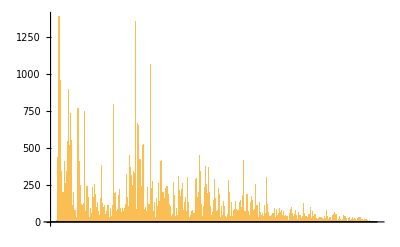

```mathematica
BarChart[Counts[Flatten[StringCases[htmlList,"../Mathematicians/"~~Shortest[a__]~~".html"->a]]]]
```

## Counting String Length

```mathematica
ClearAll[x];

getBodyBio [ htmlString_String ] := StringCases[ htmlString ,
                                                "<article>" ~~ Shortest[ x__ ] ~~ "</article>" -> x
                                                ];
                                                
deleteHtmlElements [ htmlString_String ] := StringDelete[
                                                          getBodyBio[ htmlString ],
                                                         "<"~~Shortest[__]~~">" 
                                                         ];
                                                         
numberSentences [ htmlString_String ] := Length@First@TextCases[ deleteHtmlElements [ htmlString ] , "Sentence"];

numberWords [ htmlString_String ] := Length@First@TextCases[ deleteHtmlElements [ htmlString ] , "Word"];
```

```mathematica
numberSentences[htmlList[[2]]]
```

22

```mathematica
numberWords[htmlList[[2]]]
```

477

```mathematica
StringCases[htmlList[[2]],"<article>"~~Shortest[x__]~~"</article>"->x];
```

{To write a biography of <b>Baudhayana</b> is essentially impossible since nothing is known of him except that he was the author of one of the earliest Sulbasutras. We do not know his dates accurately enough to even guess at a life span for him, which is why we have given the same approximate birth year as death year.
<p>
He was neither a mathematician in the sense that we would understand it today, nor a scribe who simply copied manuscripts like <a href="../Mathematicians/Ahmes.html" onclick="javascript:win1('../Mathematicians/Ahmes.html',400,400); return false;">Ahmes</a>. He would certainly have been a man of very considerable learning but probably not interested in mathematics for its own sake, merely interested in using it for religious purposes. Undoubtedly he wrote the Sulbasutra to provide rules for religious rites and it would appear an almost certainty that Baudhayana himself would be a Vedic priest. 
<p>
The mathematics given in the Sulbasutras is there to enable the accurate construction of altars needed for sacrifices. It is clear from the writing that Baudhayana, as well as being a priest, must have been a skilled craftsman. He must have been himself skilled in the practical use of the mathematics he described as a craftsman who himself constructed sacrificial altars of the highest quality. 
<p>
The Sulbasutras are discussed in detail in the article <a href="../HistTopics/Indian_sulbasutras.html">Indian Sulbasutras</a>. Below we give one or two details of Baudhayana's Sulbasutra, which contained three chapters, which is the oldest which we possess and, it would be fair to say, one of the two most important.
<p>
The Sulbasutra of Baudhayana contains geometric solutions (but not algebraic ones) of a linear equation in a single unknown. Quadratic equations of the forms <i>ax</i><sup>2</sup> = <i>c</i> and <i>ax</i><sup>2</sup> + <i>bx</i> = <i>c</i> appear.
<p>
Several values of &#960; occur in Baudhayana's Sulbasutra since when giving different constructions Baudhayana uses different approximations for constructing circular shapes. Constructions are given which are equivalent to taking &#960; equal to <sup>676</sup>/<sub>225</sub> (where <sup>676</sup>/<sub>225</sub> = 3.004), <sup>900</sup>/<sub>289</sub> (where <sup>900</sup>/<sub>289</sub> = 3.114) and to <sup>1156</sup>/<sub>361</sub> (where <sup>1156</sup>/<sub>361</sub> = 3.202). None of these is particularly accurate but, in the context of constructing altars they would not lead to noticeable errors.
<p>
An interesting, and quite accurate, approximate value for &#8730;2 is given in Chapter 1 verse 61 of Baudhayana's Sulbasutra. The Sanskrit text gives in words what we would write in symbols as<br>
<div style="margin:1em 0 1em 40px";>
&#8730;2 = 1 + <sup>1</sup>/<sub>3</sub> + <sup>1</sup>/<sub>(3&#215;4)</sub> - <sup>1</sup>/<sub>(3&#215;4&#215;34)</sub> = <sup>577</sup>/<sub>408</sub> <br>
</div>
which is, to nine places, 1.414215686. This gives &#8730;2 correct to five decimal places. This is surprising since, as we mentioned above, great mathematical accuracy did not seem necessary for the building work described. If the approximation was given as <br>
<div style="margin:1em 0 1em 40px";>
&#8730;2 = 1 + <sup>1</sup>/<sub>3</sub> + <sup>1</sup>/<sub>(3&#215;4)</sub><br>
</div>
then the error is of the order of 0.002 which is still more accurate than any of the values of &#960;. Why then did Baudhayana feel that he had to go for a better approximation?
<p>
See the article <a href="../HistTopics/Indian_sulbasutras.html">Indian Sulbasutras</a> for more information.
<p>
<p><font color=purple><b>Article by:</b> <i>J J O'Connor</i> and <i>E F Robertson</i></font>
}

```mathematica
MathematicianBodyBiographies = Map[getBodyBio,htmlList[]]
```

{6706,8997,7335,26071,13163,8342,33967,14134,17034,14494,13304,28030,15557,2749,21861,14801,22484,22907,25464,32564,25656,28923,20469,22478,15680,26396,25787}[]
 |  |  |  |

```mathematica
StringDelete[getBodyBio[htmlList[[2]]],"<"~~Shortest[__]~~">"]
```

```mathematica
StringDelete[%,"<"~~Shortest[__]~~">"]
```

{To write a biography of Baudhayana is essentially impossible since nothing is known of him except that he was the author of one of the earliest Sulbasutras. We do not know his dates accurately enough to even guess at a life span for him, which is why we have given the same approximate birth year as death year.

He was neither a mathematician in the sense that we would understand it today, nor a scribe who simply copied manuscripts like Ahmes. He would certainly have been a man of very considerable learning but probably not interested in mathematics for its own sake, merely interested in using it for religious purposes. Undoubtedly he wrote the Sulbasutra to provide rules for religious rites and it would appear an almost certainty that Baudhayana himself would be a Vedic priest. 

The mathematics given in the Sulbasutras is there to enable the accurate construction of altars needed for sacrifices. It is clear from the writing that Baudhayana, as well as being a priest, must have been a skilled craftsman. He must have been himself skilled in the practical use of the mathematics he described as a craftsman who himself constructed sacrificial altars of the highest quality. 

The Sulbasutras are discussed in detail in the article Indian Sulbasutras. Below we give one or two details of Baudhayana's Sulbasutra, which contained three chapters, which is the oldest which we possess and, it would be fair to say, one of the two most important.

The Sulbasutra of Baudhayana contains geometric solutions (but not algebraic ones) of a linear equation in a single unknown. Quadratic equations of the forms ax2 = c and ax2 + bx = c appear.

Several values of &#960; occur in Baudhayana's Sulbasutra since when giving different constructions Baudhayana uses different approximations for constructing circular shapes. Constructions are given which are equivalent to taking &#960; equal to 676/225 (where 676/225 = 3.004), 900/289 (where 900/289 = 3.114) and to 1156/361 (where 1156/361 = 3.202). None of these is particularly accurate but, in the context of constructing altars they would not lead to noticeable errors.

An interesting, and quite accurate, approximate value for &#8730;2 is given in Chapter 1 verse 61 of Baudhayana's Sulbasutra. The Sanskrit text gives in words what we would write in symbols as

&#8730;2 = 1 + 1/3 + 1/(3&#215;4) - 1/(3&#215;4&#215;34) = 577/408 

which is, to nine places, 1.414215686. This gives &#8730;2 correct to five decimal places. This is surprising since, as we mentioned above, great mathematical accuracy did not seem necessary for the building work described. If the approximation was given as 

&#8730;2 = 1 + 1/3 + 1/(3&#215;4)

then the error is of the order of 0.002 which is still more accurate than any of the values of &#960;. Why then did Baudhayana feel that he had to go for a better approximation?

See the article Indian Sulbasutras for more information.

Article by: J J O'Connor and E F Robertson
}

```mathematica
TextCases[%297,"Sentence"]
```

```mathematica
{{"To write a biography of Baudhayana is essentially impossible since nothing is known of him except that he was the author of one of the earliest Sulbasutras.","We do not know his dates accurately enough to even guess at a life span for him, which is why we have given the same approximate birth year as death year.","He was neither a mathematician in the sense that we would understand it today, nor a scribe who simply copied manuscripts like Ahmes.","He would certainly have been a man of very considerable learning but probably not interested in mathematics for its own sake, merely interested in using it for religious purposes.","Undoubtedly he wrote the Sulbasutra to provide rules for religious rites and it would appear an almost certainty that Baudhayana himself would be a Vedic priest. \n\nThe mathematics given in the Sulbasutras is there to enable the accurate construction of altars needed for sacrifices.","It is clear from the writing that Baudhayana, as well as being a priest, must have been a skilled craftsman.","He must have been himself skilled in the practical use of the mathematics he described as a craftsman who himself constructed sacrificial altars of the highest quality. \n\nThe Sulbasutras are discussed in detail in the article Indian Sulbasutras.","Below we give one or two details of Baudhayana's Sulbasutra, which contained three chapters, which is the oldest which we possess and, it would be fair to say, one of the two most important.","The Sulbasutra of Baudhayana contains geometric solutions (but not algebraic ones) of a linear equation in a single unknown.","Quadratic equations of the forms ax2 = c and ax2 + bx = c appear.","Several values of &#960; occur in Baudhayana's Sulbasutra since when giving different constructions Baudhayana uses different approximations for constructing circular shapes.","Constructions are given which are equivalent to taking &#960; equal to 676/225 (where 676/225 = 3.004), 900/289 (where 900/289 = 3.114) and to 1156/361 (where 1156/361 = 3.202).","None of these is particularly accurate but, in the context of constructing altars they would not lead to noticeable errors.","An interesting, and quite accurate, approximate value for &#8730;2 is given in Chapter 1 verse 61 of Baudhayana's Sulbasutra.","The Sanskrit text gives in words what we would write in symbols as\n\n&#8730;2 = 1 + 1/3 + 1/(3&#215;4)","- 1/(3&#215;4&#215;34) = 577/408 \n\nwhich is, to nine places, 1.414215686.","This gives &#8730;2 correct to five decimal places.","This is surprising since, as we mentioned above, great mathematical accuracy did not seem necessary for the building work described.","If the approximation was given as \n\n&#8730;2 = 1 + 1/3 + 1/(3&#215;4)\n\nthen the error is of the order of 0.002 which is still more accurate than any of the values of &#960;.","Why then did Baudhayana feel that he had to go for a better approximation?","See the article Indian Sulbasutras for more information.","Article by: J J O'Connor and E F Robertson\n"}}[[1]]//Length
```

22

## Wikipedia Data

```mathematica
ClearAll[b]
```

Make Wikipedia Queries, accept results that are unique and pass through interpreter if multiple entries

```mathematica
findWikiBioIDs[name_]:=With[{wikiSearch = WikipediaSearch[name]},
If[Length[wikiSearch]<2,wikiSearch,Interpreter["Person"][name]]]
```

Filter out wikipedia Queries that returned a biography page

```mathematica
wikiBioChecker[wikiResults_]:=With[{trueEntries=Select[findWikiBioIds[wikiResults],Not@*FailureQ]},{trueEntries}]
```

Return list of mathematicians without a matching wiki-page

```mathematica
wikiBlackBox[wikiResults_]:=Complement[Select[wikiResults,FailureQ==True]]
```

Check black box entries with (mathematician) label. Drop results that are still undecidable.

```mathematica
wikiCodeMathematicians= Map[WikipediaData[#<>" (mathematician)","ArticleWikicode"] &,fullNames[[30;;40]]];
```

```mathematica
someBios = Map[wikiBioChecker,fullNames[[3;;150]]]
```

{{{}},{{Thales of Miletus}},{{Anaximander of Miletus}},{{}},{{Pythagoras of Samos}},{{Pāṇini}},{{Anaxagoras of Clazomenae}},{{Empedocles of Acragas}},{{Oenopides of Chios}},{{Zeno of Elea}},{{Antiphon the Sophist}},{{Leucippus of Miletus}},{{Hippocrates of Chios}},{{Theodorus of Cyrene}},{{Democritus of Abdera}},{{Hippias of Elis}},{{Bryson of Heraclea}},{{Archytas of Tarentum}},{{Plato}},{{Theaetetus of Athens}},{{Eudoxus of Cnidus}},{{}},{{Thymaridas of Paros}},{{Xenocrates of Chalcedon}},{{Dinostratus}},{{Heraclides of Pontus}},{{Aristotle}},{{Menaechmus}},{{Aristaeus the Elder}},{{Callippus of Cyzicus}},{{Autolycus of Pitane}},{{Eudemus of Rhodes}},{{Euclid of Alexandria}},{{Aristarchus of Samos}},{{Archimedes of Syracuse}},{{Chrysippus of Soli}},{{Conon of Samos}},{{Nicomedes}},{{Philo of Byzantium}},{{Eratosthenes of Cyrene}},{{Apollonius of Perga}},{{}},{{Diocles of Carystus}},{{}},{{}},{{Hipparchus of Rhodes}},{{Hypsicles of Alexandria}},{{}},{{Theodosius of Bithynia}},{{Zeno of Sidon}},{{Posidonius of Rhodes}},{{}},{{Marcus Vitruvius Pollio}},{{Geminus}},{{}},{{Hero of Alexandria}},{{Nicomachus of Gerasa}},{{Menelaus of Alexandria}},{{Theon of Smyrna}},{{Zhang Heng}},{{Claudius Ptolemy}},{{Yavaneśvara}},{{Liu Hong}},{{}},{{Diophantus of Alexandria}},{{Liu Hui}},{{}},{{Sporus of Nicaea}},{{Pappus of Alexandria}},{{}},{{Serenus of Antinouplis}},{{Theon of Alexandria}},{{Hypatia of alexandria}},{{Sun Tzu}},{{}},{{Proclus Diadochus}},{{Domninus of Larissa}},{{Zu Chongzhi}},{{Zhang Qiujian Suanjing}},{{Marinus of Neapolis}},{{Zu Gengzhi}},{{Anthemius of Tralles}},{{}},{{Anicius manlius severinus boethius}},{{Eutocius of Ascalon}},{{Simplicius Of Cilicia}},{{Yativrsabha}},{{Varāhamihira}},{{}},{{Brahmagupta}},{{}},{{Li Chunfeng}},{{}},{{Alcuin of York}},{{Abū Jaʿfar Muḥammad ibn Mūsā al-Khwārizmī}},{{Al-Abbas ibn Said Al-Jawhari}},{{Banu Musa brothers}},{{Jafar Muhammad Banu Musa}},{{Govindasvāmi}},{{Mahavira}},{{Abu Yusuf Yaqub ibn Ishaq al-Sabbah Al-Kindi}},{{Ahmad Banu Musa}},{{Abu Zayd Hunayn ibn Ishaq al-Ibadi}},{{Al-Hasan Banu Musa}},{{Abu Abd Allah Muhammad ibn Isa Al-Mahani}},{{Prthudakasvami}},{{Ahmad ibn Yusuf al-Misri}},{{}},{{}},{{Abu Kamil Shuja ibn Aslam ibn Muhammad ibn Shuja}},{{Abu Abdallah Mohammad ibn Jabir Al-Battani}},{{C. V. Sridhar}},{{Abu'l Abbas al-Fadl ibn Hatim Al-Nayrizi}},{{}},{{Abu Jafar Muhammad ibn al-Hasan Al-Khazin}},{{Ibrahim ibn Sinan ibn Thabit ibn Qurra}},{{Abu'l Hasan Ahmad ibn Ibrahim Al-Uqlidisi}},{{}},{{}},{{Abu Mahmud Hamid ibn al-Khidr Al-Khujandi}},{{Abu Sahl Waijan ibn Rustam al-Quhi}},{{}},{{Abu Said Ahmad ibn Muhammad Al-Sijzi}},{{Gerbert of Aurillac}},{{}},{{Abu Bekr ibn Muhammad ibn al-Husayn Al-Karaji}},{{Abu Ali al-Hasan ibn al-Haytham}},{{Abu Nasr Mansur ibn Ali ibn Iraq}},{{Kushyar ibn Labban}},{{Abu Arrayhan Muhammad ibn Ahmad al-Biruni}},{{Abu Mansur ibn Tahir Al-Baghdadi}},{{}},{{Abu Abd Allah Muhammad ibn Muadh Al-Jayyani}},{{Abu l'Hasan Ali ibn Ahmad Al-Nasawi}},{{}},{{Hermann of Reichenau}},{{}},{{}},{{Omar Khayyam}},{{}},{{Abraham bar Hiyya Ha-Nasi}},{{Adelard of Bath}},{{Acharya Hemchandra}},{{Abraham Ben Meir ibn Ezra}},{{Al-Ishbili Abu Muhammad Jabir ibn Aflah}},{{Bhāskara II}},{{Gherard of Cremona}},{{Ibn Yahya al-Maghribi Al-Samawal}}}

```mathematica
Map[wikiBlackBox,fullNames[[3;;150]]]//Length (*question: are there geographic trends in biogra phies that are missing from Wikipedia?*)
```

148

Count Mentions Across All Wikipedia Pages (*hypothesize why the reach of certain mathematicians went beyond their disciplines?*)

```mathematica
macroCounter[mathematicians_]:=Length@WikipediaSearch["Content"->mathematicians]
```

```mathematica
Map[macroCounter,fullNames]
```

URLFetch::invhttp: Recv failure: Connection was reset.

Lookup::invrl: The argument Null is not a valid Association or a list of rules.

URLFetch::invhttp: Could not resolve host: en.wikipedia.org.

Lookup::invrl: The argument Null is not a valid Association or a list of rules.

URLFetch::invhttp: Could not resolve host: en.wikipedia.org.

General::stop: Further output of URLFetch::invhttp will be suppressed during this calculation.

Lookup::invrl: The argument Null is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

<|50→1447,18→26,20→27,13→32,40→12,45→7,38→13,3→89,47→6,27→13,10→36,23→17,28→21,19→24,26→20,30→11,16→19,7→52,25→17,11→39,0→89,15→21,6→45,29→16,48→11,9→41,14→27,5→50,2→86,1→87,17→25,4→48,8→47,49→15,39→9,12→36,21→27,24→19,37→12,46→12,36→17,32→10,31→12,41→8,33→12,22→15,43→10,42→10,44→8,35→11,34→11|>

Extract number of mentions from Wikipedia Data

```mathematica
wikiMentions[names_]:= Intersection[WikipediaData[names,"LinksList"],Flatten[fullNames]]
```

```mathematica
Map[wikiMentions,Flatten[someBios]]
```

{{Bartel Leendert van der Waerden,Carl Benjamin Boyer},{Anicius Manlius Severinus Boethius},{Albert Einstein,Alfred North Whitehead,Johannes Kepler,John Dee,Nicolaus Copernicus},{Bibhutibhushan Datta,Jagannatha Samrat,Narayana Pandit,Nilakantha Somayaji},{},{},{},{},{},{},{},{},{},{},{},{},{Albert Einstein,Alfred North Whitehead,Alfred Tarski,Alonzo Church,Benjamin Franklin,Charles Sanders Peirce,Galileo Galilei,George Berkeley,Hans Reichenbach,Imre Lakatos,Karl Pearson,Nicolas Malebranche,Pierre Gassendi,René Descartes,Roger Bacon,Thomas Hobbes,Willard Van Orman Quine,William of Ockham,William Whewell},{George Johnston Allman},{},{},{},{Carl Benjamin Boyer},{Otto Neugebauer},{Albert Einstein,Alfred North Whitehead,Charles Sanders Peirce,Galileo Galilei,George Berkeley,Hans Reichenbach,Imre Lakatos,James Hutton,Karl Pearson,Nicolas Malebranche,Pierre Gassendi,René Descartes,Robert Hooke,Roger Bacon,Thomas Hobbes,Willard Van Orman Quine,William of Ockham,William Whewell},{Carl Benjamin Boyer},{},{},{Carl Benjamin Boyer},{},{Bartel Leendert van der Waerden,Carl Benjamin Boyer,Claudius Ptolemy,Dirk Jan Struik,Morris Kline,Nicolas Bourbaki},{Giordano Bruno,Johannes Kepler,Nicolaus Copernicus,Tycho Brahe},{Carl Benjamin Boyer,Galileo Galilei,John Wallis,René Descartes},{},{},{},{},{},{Carl Benjamin Boyer,Edmond Halley,François Viète,Henry Aldrich,Henry Burchard Fine,Isaac Barrow,Jacobus Golius,René Descartes,Robert Simson},{},{Jean Baptiste Joseph Delambre,Johannes Kepler,Nicolaus Copernicus,Otto Neugebauer,Tycho Brahe},{Carl Benjamin Boyer},{Francesco Maurolico},{},{},{Charles Hutton,Filippo Brunelleschi,Leone Battista Alberti},{},{Pierre de Fermat},{},{Francesco Maurolico},{Otto Neugebauer},{},{Carl Benjamin Boyer,Galileo Galilei},{},{},{Carl Benjamin Boyer,Hermann Hankel,Pierre de Fermat,Rafael Bombelli},{},{},{David Eugene Smith,Michel Chasles,Paul Guldin},{},{},{Paul Tannery},{Benjamin Franklin,Nicolas Malebranche,Thomas Hobbes},{Anicius Manlius Severinus Boethius,Nicholas of Cusa},{Paul Tannery},{John Machin,William Shanks},{},{},{},{Carl Benjamin Boyer},{Blaise Pascal,Giordano Bruno,Nasir al-Din al-Tusi,Nicolas Malebranche,Nicole Oresme,Ramon Llull,René Descartes,Robert Grosseteste,Roger Bacon,William Kingdon Clifford,William of Ockham,William Whewell},{Carl Benjamin Boyer},{},{Bibhutibhushan Datta,Jagannatha Samrat,Narayana Pandit,Nilakantha Somayaji},{Bibhutibhushan Datta,Jagannatha Samrat,Narayana Pandit,Nilakantha Somayaji},{Bibhutibhushan Datta,Jagannatha Samrat,Narayana Pandit,Nilakantha Somayaji},{},{Blaise Pascal,Nasir al-Din al-Tusi,Nicholas of Cusa,Nicolas Malebranche,Nicole Oresme,Pierre Gassendi,Ramon Llull,René Descartes,Robert Grosseteste,Roger Bacon,William of Ockham},{Carl Benjamin Boyer,Claudius Ptolemy,Dirk Jan Struik,Florian Cajori,Heinrich Suter,Nasir al-Din al-Tusi,Omar Khayyam,Otto Neugebauer},{Nasir al-Din al-Tusi,Omar Khayyam},{Nasir al-Din al-Tusi,Omar Khayyam,Roger Bacon},{Nasir al-Din al-Tusi,Omar Khayyam,Roger Bacon},{Bibhutibhushan Datta,Jagannatha Samrat,Narayana Pandit,Nilakantha Somayaji},{},{Nasir al-Din al-Tusi,Omar Khayyam,Robert Grosseteste,Roger Bacon},{Nasir al-Din al-Tusi,Omar Khayyam,Roger Bacon},{},{Nasir al-Din al-Tusi,Omar Khayyam,Roger Bacon},{Nasir al-Din al-Tusi,Omar Khayyam},{},{Luca Pacioli,Nasir al-Din al-Tusi,Omar Khayyam,Thomas Bradwardine},{Nasir al-Din al-Tusi,Omar Khayyam},{Nasir al-Din al-Tusi,Nicolaus Copernicus,Omar Khayyam,Tycho Brahe},{},{Nasir al-Din al-Tusi,Omar Khayyam},{Nasir al-Din al-Tusi,Omar Khayyam},{Nasir al-Din al-Tusi,Omar Khayyam},{Nasir al-Din al-Tusi,Omar Khayyam},{Nasir al-Din al-Tusi,Omar Khayyam},{Nasir al-Din al-Tusi,Omar Khayyam},{Nasir al-Din al-Tusi,Omar Khayyam},{},{Galileo Galilei,Johannes Kepler,Nasir al-Din al-Tusi,Omar Khayyam},{Christiaan Huygens,Galileo Galilei,Jacob Bronowski,Johannes Kepler,Leonhard Euler,Nasir al-Din al-Tusi,Omar Khayyam,René Descartes,Robert Grosseteste,Roger Bacon},{Nasir al-Din al-Tusi,Omar Khayyam},{Nasir al-Din al-Tusi,Omar Khayyam},{Nasir al-Din al-Tusi,Omar Khayyam},{John Dee,Nasir al-Din al-Tusi,Omar Khayyam},{Nasir al-Din al-Tusi,Omar Khayyam},{Nasir al-Din al-Tusi,Omar Khayyam},{},{David Eugene Smith,Dirk Jan Struik,John Wallis,Nasir al-Din al-Tusi,Scipione del Ferro},{},{Robert Grosseteste,Roger Bacon},{},{},{Nasir al-Din al-Tusi,Omar Khayyam},Missing[NotAvailable]∩{Ahmes,Baudhayana ,Manava ,Thales of Miletus ,Anaximander of Miletus ,Apastamba ,Pythagoras of Samos ,Panini ,Anaxagoras of Clazomenae ,Empedocles of Acragas ,Oenopides of Chios ,Zeno of Elea ,Antiphon the Sophist,Leucippus of Miletus ,Hippocrates of Chios ,Theodorus of Cyrene ,Democritus of Abdera ,Hippias of Elis ,Bryson of Heraclea ,Archytas of Tarentum ,Plato ,Theaetetus of Athens ,Eudoxus of Cnidus ,Gan De ,Thymaridas of Paros ,Xenocrates of Chalcedon ,Dinostratus ,Heraclides of Pontus ,Aristotle ,Menaechmus ,Aristaeus the Elder ,Callippus of Cyzicus ,Autolycus of Pitane ,Eudemus of Rhodes ,Euclid of Alexandria ,Aristarchus of Samos ,Archimedes of Syracuse ,Chrysippus of Soli ,Conon of Samos ,Nicomedes ,Philon of Byzantium ,Eratosthenes of Cyrene ,Apollonius of Perga ,Dionysodorus ,Diocles of Carystus,Katyayana ,Zenodorus ,Hipparchus of Rhodes ,Hypsicles of Alexandria ,Perseus ,Theodosius of Bithynia ,Zeno of Sidon ,Posidonius of Rhodes ,Luoxia Hong ,Marcus Vitruvius Pollio,Geminus ,Cleomedes ,Heron of Alexandria ,Nicomachus of Gerasa ,Menelaus of Alexandria ,Theon of Smyrna , Zhang Heng,Claudius Ptolemy,Yavanesvara ,Liu Hong ,Xu Yue ,Diophantus of Alexandria ,Liu Hui ,Porphyry Malchus ,Sporus of Nicaea ,Pappus of Alexandria ,Pandrosion of Alexandria ,Serenus ,Theon of Alexandria ,Hypatia of Alexandria ,Sun Zi ,Xiahou Yang ,Proclus Diadochus ,Domninus of Larissa ,Zu Chongzhi ,Zhang Qiujian ,Marinus of Neapolis ,Zu Geng ,Anthemius of Tralles ,Aryabhata the Elder ,Anicius Manlius Severinus Boethius,Eutocius of Ascalon ,Simplicius ,Yativrsabha ,Varahamihira ,Wang Xiaotong ,Brahmagupta ,Bhaskara I,Li Chunfeng ,Lalla ,Alcuin of York ,Abu Ja'far Muhammad ibn Musa Al-Khwarizmi,al-Abbas ibn Said Al-Jawhari,Banu Musa brothers,Jafar Muhammad Banu Musa,Govindasvami ,Mahavira ,Abu Yusuf Yaqub ibn Ishaq al-Sabbah Al-Kindi,Ahmad Banu Musa,Abu Zayd Hunayn ibn Ishaq al-Ibadi,al-Hasan Banu Musa,Abu Abd Allah Muhammad ibn Isa Al-Mahani,Prthudakasvami ,Ahmed ibn Yusuf  al-Misri ,Al-Sabi Thabit ibn Qurra al-Harrani,Sankara Narayana,Abu Kamil Shuja ibn Aslam ibn Muhammad ibn Shuja , Abu Abdallah Mohammad ibn Jabir Al-Battani,Sridhara ,Abu'l Abbas al-Fadl ibn Hatim Al-Nayrizi,Abu Said Sinan ibn Thabit ibn Qurra,Abu Jafar Muhammad ibn al-Hasan Al-Khazin, Ibrahim ibn Sinan  ibn Thabit ibn Qurra,Abu'l Hasan Ahmad ibn Ibrahim Al-Uqlidisi,Aryabhata II ,Abu'l-Wafa,Abu Mahmud Hamid ibn al-Khidr Al-Khujandi, Abu Sahl Waijan ibn Rustam al-Quhi,Vijayanandi ,Abu Said Ahmad ibn Muhammad Al-Sijzi,Gerbert of Aurillac,Abu'l-Hasan Ali ibn Abd al-Rahman ibn Yunus,Abu Bekr ibn Muhammad ibn al-Husayn Al-Karaji, Abu Ali al-Hasan ibn al-Haytham, Abu Nasr Mansur ibn Ali ibn Iraq,Kushyar ibn Labban, Abu Arrayhan Muhammad ibn Ahmad al-Biruni,Abu Mansur ibn Tahir Al-Baghdadi, Abu Ali al-Husain ibn Abdallah ibn Sina (Avicenna),Abu Abd Allah Muhammad ibn Muadh Al-Jayyani,Abu l'Hasan Ali ibn Ahmad Al-Nasawi,Jia Xian ,Hermann of Reichenau,Sripati ,Shen Kua ,Omar Khayyam,Brahmadeva ,Abraham bar Hiyya Ha-Nasi ,Adelard of Bath ,Acharya Hemchandra, Abraham ben Meir ibn Ezra,al-Ishbili Abu Muhammad Jabir ibn Aflah,Bhaskara ,Gherard of Cremona ,Ibn Yahya al-Maghribi Al-Samawal,Sharaf al-Din al-Muzaffar al-Tusi,Reinher of Paderborn ,Robert Grosseteste,Leonardo Pisano Fibonacci,Michael Scot,Li Zhi ,Johannes de Sacrobosco, Saint Albertus Magnus,Nasir al-Din al-Tusi,Qin Jiushao ,Roger Bacon,Muhyi l'din al-Maghribi,Campanus of Novara ,Jordanus Nemorarius,Guo Shoujing ,Ramon Llull,Jacob ben Machir ibn Tibbon,Yang Hui ,Shams al-Din ibn Ashraf Al-Samarqandi,al-Marrakushi ibn Al-Banna,Kamal al-Din Abu'l Hasan Muhammad Al-Farisi,Zhu Shijie ,Zhao Youqin,Levi ben Gerson ,William of Ockham,Thomas Bradwardine,Albert of Saxony ,Shams al-Din Abu Abdallah Al-Khalili,Nicole Oresme,Mahendra Suri ,Narayana Pandit,Madhava of Sangamagramma,Qadi Zada al-Rumi,Paramesvara ,Filippo Brunelleschi,Ghiyath al-Din Jamshid Mas'ud al-Kashi,Ulugh Beg ,Abu Abdallah Yaish ibn Ibrahim Al-Umawi,Nicholas of Cusa,Leone Battista Alberti, Abu'l Hasan ibn Ali al Qalasadi,Piero della Francesca,Georg Peurbach,Piero Borgi,Johann Müller Regiomontanus,Nilakantha Somayaji,Nicolas Chuquet,Luca Pacioli,Leonardo da Vinci ,Johannes Widman,Scipione del Ferro,Johann Werner,John Maior,Estienne de La Roche,Charles de Bouvelles,Albrecht Dürer,Nicolaus Copernicus,Cuthbert Tunstall,Juan de Ortega,Gaspar Lax,Michael Stifel,Adam Ries,Oronce Fine,Francesco Maurolico,Petrus Apianus,Christoff Rudolff,Jyesthadeva ,Nicolo Tartaglia,Girolamo Cardano,Pedro Nunes Salaciense,Frederico Commandino,Regnier Gemma Frisius,Robert Recorde,Gerardus Mercator,Georg Joachim von Lauchen Rheticus,Peter Ramus,Lodovico Ferrari,Rafael Bombelli,John Dee,Giovanni Battista Benedetti,Cheng Dawei ,Giambattista Della Porta,Egnatio Pellegrino Rainaldi Danti,Franciscus Barocius,Christopher Clavius,Thomas Allen,Ludolph Van Ceulen,François Viète,Guidobaldo Marchese del Monte,Tycho Brahe,Thomas Digges,Paul Wittich,Baha' ad-Din al-Amili,Giordano Bruno,Pietro Antonio Cataldi,Simon Stevin, Sir Henry Savile,Michael Mästlin,John Napier,Jost Bürgi,Matteo Ricci,Luca Valerio,João Delgado,João Baptista Lavanha,Giovanni Antonio Magini,Thomas Harriot,Henry Briggs,Thomas Fincke,Johan Philip van Lansberge,Bartholomeo Pitiscus,Adriaan van Roomen,Xu Guangqi ,Galileo Galilei,Giuseppe Biancani,Marino Ghetaldi,Johannes Kepler,Simon Mayr,Christoph Scheiner,William Oughtred,Paul Guldin,Benedetto Antonio Castelli,Johann Faulhaber,Pierre Hérigone,Willebrord van Royen Snell,Claude Gaspar Bachet de Méziriac,Edmund Gunter,Jean-Baptiste Morin,Gregorius Saint-Vincent,Pierre Vernier,Claude Mydorge,Peter Turner,Joachim Jungius,Benjamin Bramer,Thomas Hobbes,Marin Mersenne,Étienne Pascal,Jean Beaugrand, Girard Desargues,Pierre Gassendi,Wilhelm Schickard,Pierre Petit,Albert Girard,René Descartes,Jacobus Golius,Henry Gellibrand,Jean Charles de La Faille,Bonaventura Francesco Cavalieri,Claude Hardy,Giovanni Battista Riccioli,Pierre de Carcavi,Richard Delamain,Adriaan Vlacq,Florimond de Beaune,Pierre de Fermat,Jacques de Billy,John Greaves,Gilles Personne de Roberval,Bernard Frenicle de Bessy,Ismael Boulliau,Juan Caramuel y Lobkowitz,Maria Cunitz,Giovanni Alfonso Borelli,Honoré Fabri,Evangelista Torricelli,Jacques Alexandre Le Tenneur,Jan Jansz de Jonge Stampioen,Johannes Hevelius,John Pell,Antoine Arnauld,Andrea Tacquet,Henry More,John Wilkins,Frans van Schooten,Kamalakara ,John Wallis,Seth Ward,Francesco Maria Grimaldi,Jeremiah Horrocks,Gabriel Mouton,Claude Mylon,Michelangelo Ricci,William Brouncker,Nicolaus Mercator,Jean Picard,Claude François Milliet Dechales,Adrien Auzout,Johann Heinrich Rahn,René François Walter de Sluze,Vincenzo Viviani,Stefano degli Angeli,Blaise Pascal,John Collins,Guarino Guarini,János Apáczai Csere,Erasmus Bartholin, Giovanni Domenico Cassini,Jan de Witt,Pietro Mengoli,Robert Boyle,Jonas Moore,Johann van Waveren Hudde,Christiaan Huygens,Isaac Barrow,Jean Richer,Edward Cocker,Sir Christopher Wren,Mei Wending,Hendrik van Heuraet,Robert Hooke,William Neile,James Gregory,Nicolas Malebranche,Philippe de La Hire,Bernard Lamy,Georg Mohr,Jacques Ozanam,Takakazu Shinsuke Seki,Sir Isaac Newton,Carlos de Siguenza y Gongora,John Flamsteed,Gottfried Wilhelm von Leibniz,Giovanni Benedetto Ceva,Catherina Elisabetha Koopman Hevelius,Denis Papin,Henry Aldrich,Tommaso Ceva,Ehrenfried Walter von Tschirnhaus, Jean Le Fèvre,Michel Rolle,Abraham Sharp,Pierre Varignon,Jacob (Jacques) Bernoulli,Edmond Halley,William Molyneux,Charles René Reyneau,Bernard le Bovier de Fontenelle,David Gregory,Joseph Saurin,Thomas Fantet de Lagny,De_L'Hopital,Louis Carré,John Craig,Takebe Katahiro,John Arbuthnot,Johann Bernoulli,Abraham de Moivre,Giovanni Girolamo Saccheri,William Whiston,Joseph Raphson,Leonty Filippovich Magnitsky,Maria Margarethe Winckelmann Kirch,Luigi Guido Grandi,John Keill,Eustachio Manfredi,Samuel Clarke,William Jones,Jacopo Francesco Riccati,Jacques Cassini, Johann Gabriel Doppelmayr,Joseph Privat de Molières,Charles Hayes,Jakob Hermann,Pierre Rémond de Montmort,John Colson,John Machin,Gabriele Manfredi,Mei Juecheng,Roger Cotes, Giulio Carlo Fagnano dei Toschi,John Hadley,Nicholas Saunderson,Giovanni Poleni,George Berkeley,Brook Taylor,Nicolaus(I) Bernoulli,Robert Simson,Louis Bertrand Castel,Roger Paman,Willem Jacob 'sGravesande,Samuel Molyneux,Christian Goldbach,Jagannatha Samrat,James Stirling,Nicolaus(II) Bernoulli,Pierre Bouguer, Colin Maclaurin,Pierre Louis Moreau de Maupertuis, Charles Étienne Louis Camus,Daniel Bernoulli,Nathaniel Bliss, William Braikenridge,Edmund Stone,William Emerson,Charles Marie de La Condamine,Thomas Bayes,Antoine Deparcieux,Johann Francesco Melchiore Salvemini Castillon, Gabriel Cramer,Alexis Fontaine des Bertins,Johann Andreas von Segner, Gabrielle Émilie Le Tonnelier de  Breteuil Marquise du Châtelet,Benjamin Franklin, Georges Louis Leclerc Comte de Buffon,Leonhard Euler,Vincenzo Riccati,Benjamin Robins,Johann(II) Bernoulli,Thomas Fuller,Thomas Simpson,Laura Maria Catarina Bassi,Ruggero Giuseppe Boscovich,Johann Samuel König,Alexis Claude Clairaut,César-François Cassini de Thury,Alexander Wilson,Giovanni Francesco Fagnano dei Toschi,D'Alembert,Matthew Stewart,Maria Gaëtana Agnesi,István Hatvani, Abraham Gotthelf Kästner,John Landen,Nicole-Reine Etable de Labrière Lepaute,Tobias Mayer,Richard Price, Franz Maria Ulrich Theodosius Aepinus,Patrick d'Arcy,Jean Étienne Montucla,James Hutton,Paolo Frisi,Johann Heinrich Lambert,Louis Antoine de Bougainville,Étienne Bézout,Charles Bossut,Benjamin Banneker,Gian Francesco Malfatti,Francis Maseres,Chokuyen Naonobu Ajima,Wenceslaus Johann Gustav Karsten,Joseph-Jérôme Lefrançais de Lalande,Nevil Maskelyne,David Rittenhouse,Jean Charles de Borda,Achille Pierre Dionis du Séjour,José Monteiro da Rocha,Antonio Maria Lorgna,Jesse Ramsden,Alexandre-Théophile Vandermonde,Erland Samuel Bring,Charles Augustin de Coulomb,Joseph-Louis Lagrange, Johannes Nikolaus Tetens,Edward Waring,Charles Hutton,Nicolas Vilant,Frederick William Herschel,Georg Simon Klügel, Anders Johan Lexell,Carl Friedrich Hindenburg,John Wilson,Marie Jean Antoine Nicolas de  Caritat Condorcet,Johann(III) Bernoulli,José Anastácio da Cunha,Pierre François-André Méchain,George Atwood,Caspar Wessel, Gaspard Monge,William Trail,Aida Yasuaki ,Jean-Dominique Comte de Cassini,John Playfair,D'Amondans Charles de Tinseau,Jean Baptiste Joseph Delambre,John Hellins,Pierre-Simon Laplace,James Glenie,Caroline Lucretia Herschel,Simon Antoine Jean Lhuilier,Lorenzo Mascheroni,William Morgan,John Bonnycastle,Adrien-Marie Legendre,Lazare Nicolas Marguérite Carnot,Nicola Fergola,Dugald Stewart,Edward Troughton,Nicolas-François Canard,Georg Freiherr von Vega,Gaspard Clair François Marie  Riche de Prony,Nicolaus Fuss,Marc-Antoine Parseval des Chênes,John West,Louis François Antoine Arbogast,Jacob(II) (Jacques(II)) Bernoulli,Pietro Paoli,Christian Kramp, Ferdinand François Désiré Budan de Boislaurent,Ruan Yuan ,Pierre Simon Girard,Sir James Ivory,Sylvestre François Lacroix,Timofei Fedorovic Osipovsky,Johann Friedrich Pfaff,Paolo Ruffini,John Mortimer Brinkley,John Farey,John Leslie,Alexis Bouvard,Jean Robert Argand,Jean Baptiste Joseph Fourier,François Joseph Français,Marie-Jeanne Amélie Harlay,Li Rui ,Pietro Abbati Marescotti,François Joseph Servois,William Wallace,Johann Christian Martin Bartels,Annibale Giuseppe Nicolò Giordano,Jean Nicolas Pierre Hachette,Louis Puissant,Joseph Diaz Gergonne,Antoine-André-Louis Reynaud,Robert Haldane,Bartholomew Lloyd, Nathaniel Bowditch,Johann Karl Burckhardt,Louis Benjamin Francoeur,Robert Woodhouse,Thomas Young,Jean Baptiste Biot,Olinthus Gilbert Gregory,Karl Brandan Mollweide,Robert Adrain,André Marie Ampère,Farkas Wolfgang Bolyai,Jacques Frédéric Français,Étienne Louis Malus,Peter Barlow,Marie-Sophie Germain,Barnabé Brisson,Johann Carl Friedrich Gauss,Daniel Friedrich Hecht,Louis Poinsot,William Spence,Jozéf-Maria Hoëné de Wronski,Benjamin Gompertz,August Leopold Crelle, Mary Fairfax Greig Somerville,Giovanni Giorgio Bidone, Bernard Placidus Johann  Nepomuk Bolzano,Giovanni Antonio Amedeo Plana,Siméon Denis Poisson,Vincenzo Flauti,Charles Julien Brianchon,Claude Louis Mathieu,Friedrich Wilhelm Bessel,Pierre Charles François Dupin,Claude Louis Marie Henri Navier,Dominique François Jean Arago,Jacques Philippe Marie Binet,William George Horner,Jean-Nicolas Nicollet,James Thomson,John Walsh,Louis Lefébure de Fourcy,Enno Heeren Dirksen,Augustin Jean Fresnel,William Stirling Hamilton,Jean Victor Poncelet,Antonio Maria Bordoni,Augustin Louis Cauchy,Georg Simon Ohm,Jean-Baptiste Charles Joseph Bélanger,August Ferdinand Möbius,Theodore Strong,Charles Hughes Terrot,Charles Babbage,Michael Faraday,Victor Amédée Lebesgue,C V Mourey,George Peacock,Alexis Thérèse Petit,Félix Savart,Gaspard Gustave de Coriolis,John Frederick William Herschel, Nikolai Ivanovich Lobachevsky,Martin Ohm,Michel Chasles,George Green,William Hopkins,Jakob Philipp Kulik,Théodore Olivier,Germinal Pierre Dandelin,Franz Adolph Taurinus,William Whewell,Thomas Carlyle,Bernt Michael Holmboe,Gabriel Lamé,Émile Léger,Arthur Jules Morin,Louis Paul Emile Richard,Benjamin Olinde Rodrigues,Charles Matthew Whish,Irenée-Jules Bienaymé,Nikolai Dmetrievich Brashman,Sadi Nicolas Léonard Carnot,Lambert Adolphe Jacques Quetelet,Jakob Steiner,Jean Marie Constant Duhamel,Pierre-Joseph-Étienne Finck, Adhémar Jean Claude Barré de Saint-Venant,Felix Savary,Étienne E Bobillier,Christoph Gudermann,Franz Ernst Neumann,Heinrich Ferdinand Scherk,Karl Georg Christian von Staudt,Benoit Paul Émile Clapeyron,Karl Heinrich Gräffe,Karl Wilhelm Feuerbach,Stephen de Gurbs,Humphrey Lloyd,William Henry Fox Talbot,George Biddell Airy,Thomas Clausen,Antoine Augustin Cournot,Mikhail Vasilevich Ostrogradski, Joseph Antoine Ferdinand Plateau,Julius Plücker,Joseph Ludwig Raabe,Niels Henrik Abel,János Bolyai,Jean-Baptiste Brasseur,Giusto Bellavitis,Christian Andreas Doppler,Count Guglielmo Libri Carucci dalla Sommaja,Christian Heinrich von Nagel,Jacques Charles François Sturm,Viktor Yakovlevich Bunyakovsky, Carl Gustav Jacob Jacobi,George Birch Jerrard,Pierre François Verhulst,Wilhelm Eduard Weber, Johann Peter Gustav Lejeune Dirichlet,Sir William Rowan Hamilton,Edward Sang,James Booth,Augustus De Morgan,John Thomas Graves,Thomas Penyngton Kirkman,Ernst Ferdinand Adolf Minding,Robert Murphy,Julius Lugwig Weisbach,Józeph Miksa Petzval,Moritz Abraham Stern,Louis Victoire Athanase Dupré,Philip Kelland,Johann Benedict Listing,John Scott Russell,Hermann Günter Grassmann,Joseph Liouville,James MacCullagh, Luigi Federico Menabrea,Benjamin Peirce,John Henry Pratt,Oliver Byrne,Ernst Eduard Kummer,Évariste Galois,Andrew Searle Hart,Ludwig Otto Hesse,Urbain Jean Joseph Le Verrier,Li Shanlan ,John James Waterston,Gustav Adolph Göpel,Charles Graves,William Shanks,Robert Richard Anstice,Duncan Farquharson Gregory,Pierre Alphonse Laurent,Eugène Charles Catalan,John William Colenso,Daniel Augusto da Silva,Franc Mocnik,Matthew O'Brien,Ferdinando Pio Rosellini,Ludwig Schläfli,James Joseph Sylvester,Pierre Laurent Wantzel, George Boole, Augusta Ada King, countess of Lovelace,Osip Ivanovich Somov,Karl Theodor Wilhelm Weierstrass,Charles Eugene Delaunay,Jean Frédéric Frenet,Johann Georg Rosenhain,Johann Rudolf Wolf,Carl Wilhelm Borchardt,Charles Auguste Briot,William Ferrel,Angelo Genocchi,Ole Jacob Broch,Joel Evans Hendricks,Ferdinand Joachimsthal,John Couch Adams,Siegfried Heinrich Aronhold,Pierre Ossian Bonnet,Jean Claude Bouquet,James Cockle,Armand-Hippolyte-Louis Fizeau,Jean Bernard Léon Foucault,George Salmon,Joseph Alfred Serret,George Gabriel Stokes,John Casey,William Chauvenet,Ernest Jean Philippe Fauque de Jonquières,Florence Nightingale,Victor Alexandre Puiseux,William John Macquorn Rankine,Isaac Todhunter,Arthur Cayley,Pafnuty Lvovich Chebyshev,Samuel Haughton, Heinrich Eduard Heine, Hermann Ludwig Ferdinand von Helmholtz, Ramchundra,Philipp Ludwig von Seidel, Joseph Louis François Bertrand,Rudolf Julius Emmanuel Clausius, Francis Galton,Charles Hermite,Jules Antoine Lissajous,William Oughter  Lonie,Jacob Amsler,Enrico Betti,Hugh Blackburn,August Yulevich Davidov,Ferdinand Gotthold Max Eisenstein,Guillaume Jules Hoüel,Leopold Kronecker,Oscar Xaver Schlömilch,George Johnston Allman,Francesco Brioschi,Delfino Codazzi,Johann Martin Zacharias Dase,Gustav Robert Kirchhoff, William Thomson (Lord Kelvin),Johann Jakob Balmer,Carl Anton Bjerknes,Francesco da Paola Virgilio Secondo Maria Faà di Bruno,William Spottiswoode,Mikhail Egorovich Vashchenko-Zakharchenko,John James Walker,Giuseppe Battaglini,Morgan William Crofton,Daniel Friedrich Ernst Meissel,Georg Friedrich Bernhard Riemann,Henry John Stephen Smith, Ludwig Christian Wiener,Lajos Martin, Charles Watkins Merrifield,Samuel Roberts,Henry William Watson,Giuseppe Bruno,Karl Mikhailovich Peterson,Moritz Benedikt Cantor,Elwin Bruno Christoffel,Robert McNair Ferguson,Norman Macleod Ferrers,Heinrich Eduard Schröter,Joseph Wolstenholme,Antonio Luigi Gaudenzio  Giuseppe Cremona,Thomas Archer Hirst,Thomas Bond Sprague,Dorothea Beale,Julius Wilhelm Richard Dedekind, Paul David Gustav du Bois-Reymond,Victor Mayer Amédée Mannheim,James Clerk Maxwell, Edward John Routh,Georg Joseph Sidler,Peter Guthrie Tait,Mary Everest Boole,Edmond Bour,Charles Lutwidge Dodgson, Otto Wilhelm Fiedler,Rudolf Otto Sigismund Lipschitz,Carl Gottfried Neumann,Eugène Rouché,Peter Ludwig Mejdell Sylow,Robert Tucker,Johann Georg Zehfuss,Rudolf Friedrich Alfred Clebsch,Henri Auguste Delannoy,François-Jacques-Philippe Folie,Lazarus Immanuel Fuchs,Erastus Lyman De Forest,William Jack, Edmond Nicolas Laguerre, John Venn,John Howard Van Amringe,Eugenio Beltrami,Felice Casorati,William Stanley Jevons,Artemas Martin,Émile Léonard Mathieu, Hugues Charles Robert Méray,James Moriarty, Simon Newcomb,John Purser,Josef Stefan,Julius Weingarten,Paul Gustav Heinrich Bachmann,Hermann Bleuler,Nicolai Vasilievich Bugaev,Paul Albert Gordan,Leo Königsberger,Aleksandr Nikolaevich Korkin,Wilhelm Lexis,Hugh MacColl, Joseph Marie de Tilly,Edwin Abbott Abbott,Frank Stephen Baldwin,George William Hill,Jeno Hunyadi, Marie Ennemond Camille Jordan,Karl Theodor Reye,Thorvald Nicolai Thiele,Joseph Émile Barbier,James Bolam,Josiah Willard Gibbs,Hermann Hankel,Adolph Mayer,Charles Sanders Peirce,Julius Peter Christian Petersen,Gustav Roch,Francesco Siacci,Hieronymous Georg Zeuthen,Ernst Abbe,Robert Stawell Ball, Olaus Magnus Friedrich Erdmann Henrici,Émile Michel Hyacinthe Lemoine,John Emory McClintock,Franz Carl Joseph Mertens,Joseph Jean Baptiste Neuberg,Johann Jakob Rebstein, Carl Johannes Thomae,William Woolsey Johnson, Matthieu Paul Hermann Laurent, Samuel Loyd,Friedrich Wilhelm Karl Ernst Schröder,Friedrich Otto Rudolf Sturm,Giuseppe Basso,Joseph Valentin Boussinesq,Alexander Wilhelm von Brill,Agnes Mary Clerke,Jean Gaston Darboux,D'Ovidio,Marius Sophus Lie, François Édouard Anatole Lucas,William Davidson Niven,John William Strutt  (Lord Rayleigh),Osborne Reynolds,Jakob Rosanes,Yulian-Karl Vasilievich Sokhotsky,Otto Stolz,George Thom,Heinrich Martin Georg Friedrich Weber,Ernst Mauritz Dahlin,Karl Friedrich Geiser,John Sturgeon Mackay,Moritz Pasch,Hermann Amandus Schwarz,James Stuart,Paul Tannery,Gaston Tarry,Heinrich Friedrich Weber,Ludwig Boltzmann,George Henri Halphen,Jacob Lüroth,Paul Mansion, Thomas Muir,Max Noether,Ágoston Scholtz,Friedrich Heinrich Albert Wangerin,Albert Victor Bäcklund, Pierre René Jean Baptiste Henri Brocard,Georg Ferdinand Ludwig Philipp Cantor,William Kingdon Clifford,George Howard Darwin,Ulisse Dini, Francis Ysidro Edgeworth,Salomon Eduard Gubler,Vaclav Jerabek,Charles Niven,François-Félix Tisserand,Eugenio Bertini,Henry C Heaton,Magnus Gösta Mittag-Leffler,Eugen Otto Erwin Johannes Netto,Platon Sergeevich Poretsky,Mór Réthy,Pieter Hendrik Schoute,Enoch Beery Seitz,Cesare Arzelà,Carlo Alberto Castigliano,Gyula Farkas,Achille Marie Gaston Floquet,Andrew Gray,Alfred George Greenhill,Wilhelm Karl Joseph Killing,Christine Ladd-Franklin,Washington Irving Stringham,John Wilson,Nikolai Egorovich Zhukovsky,Egor Ivanovich Zolotarev,Konstantin Alekseevich Andreev, Ernst Heinrich Bruns,Lóránd Baron von Eötvös,Friedrich Ludwig Gottlob Frege,James Whitbread Lee Glaisher,Adam Wilhelm Siegmund Günther,Diederik Johannes Korteweg,Hermann Cäsar Hannibal Schubert,Heinrich Suter,Jules Tannery,Emil Weyr,Andrew Jeffrey Gunion Barclay,Ferdinand Georg Frobenius,Leopold Bernhard Gegenbauer,John Hopkinson,Alfred Bray Kempe, Felix Christian Klein,Julius König, Horace Lamb,Robert Forsyth Scott, Nikolay Yakovlevich Sonin,Robert Simpson Woodward,Walter William Rouse Ball,Sophie Willock Bryant,Jorgen Pedersen Gram, Oliver Heaviside,Sofia Vasilyevna Kovalevskaya,Alfred Pringsheim,Peter Redford Scott Lang,William Edward Story,Adolphe-Louis Jacques Bertillon, George Chrystal,Emanuel Czuber,Samuel Dickstein,Edwin Bailey Elliott,George Francis FitzGerald,Julius Gysel,Spiru Haret,Karl Gustav Axel von Harnack,Ellen Amanda Hayes,William James Macdonald,Friedrich Hermann Schottky,James Taylor,Francisco Gomes Teixeira,Adolf Weiler,William Burnside,François Nicolas Cosserat,Giovanni Frattini,Johann Heinrich Graf,Walter Gröbli,Albin Herzog,Andrei Petrovich Kiselev,Constantin Marie Michel Hubert Jérôme Le Paige,Carl Louis Ferdinand von Lindemann,Francis Robbins Upton,Eduard Weyr,Fabian Franklin, George Bruce Halsted,John Guthrie Kerr, Hendrik Antoon Lorentz,Heinrich Maschke,Salvatore Pincherle,Gregorio Ricci-Curbastro,Arthur Moritz Schönflies,Phoebe Sarah Hertha Marks Ayrton,Christian Beyel,Marcel Louis Brillouin,Leopold Klug, Percy Alexander MacMahon,Robert Hjalmar Mellin,Benjamin Osgood Peirce,Robert Philip,Jules Henri Poincaré,Johannes Robert Rydberg,Ivan Vladislavovich &#346;leszy&#324;ski,Giuseppe Veronese,Paul Emile Appell, Sir Charles Vernon Boys,Alfredo Capelli,Thomas Craig,Giovanni Battista Guccia,Christian Sophus Juel,Pierre Henri Puiseux,Karl Friedrich Wilhelm Rohn,John Edward Aloysius Steggall,Gyula Vályi,Ernst Eduard Wiltheiss,Luigi Bianchi,Arnold Droz-Farny, Ernest William Hobson,Cargill Gilston Knott,Donald Macmillan,Andrei Andreyevich Markov,Friedrich Wilhelm Franz Meyer,Giacinto Morera,Charles Émile Picard,Ferdinand Rudio,Carl David Tolmé Runge, Thomas Jan Stieltjes,William Thomson,Walther Franz Anton von Dyck,Oskar Bolza, Henry Ernest Dudeney,Alexander Yule Fraser,Heinrich Rudolf Hertz,Adolf Kiefer,Sir Joseph Larmor,Aleksandr Mikhailovich Lyapunov,Karl Pearson,Alexander Pell,Hermann Ludwig Gustav Wiener,Henry Burchard Fine, Andrew Russell Forsyth,Francesco Gerbaldi,George Alexander Gibson,Édouard Jean-Baptiste Goursat,William Ernest Johnson,Gabriel Xavier Paul Koenigs,Giuseppe Peano, Max Karl Ernst Ludwig Planck,Charlotte Angas Scott,Boris Yakovlevic Bukreev,Florian Cajori,Ernesto Cesàro,Alfonso Maria Del Re,Jérôme Franel,Karl Heun,Ludwig Otto Hölder,Marie Georges Humbert,Adolf Hurwitz, Johan Ludwig William Valdemar Jensen, Ivan Vsevolodovich Meshchersky,Georg Alexander Pick,Samuil Osipovich Shatunovsky,Giulio Benedetto Isacco Vivanti,Charles Chree,Karl Friedrich August Gutzmer,Herman Hollerith,Matyá&#353; Lerch,Alexander Morgan,Frank Morley,Robert Franklin Muirhead,Mario Pieri,John Robertson Pullar,David Eugene Smith,Alicia Boole Stott,Thompson_D'Arcy,Samuel Giuseppe Vito Volterra,Walter Frank Raphael Weldon,John Alison,Ivar Otto Bendixson,Cesare Burali-Forti,Heinrich Friedrich Karl Ludwig Burkhardt,John Brown Clark,Frank Nelson Cole,Pierre Maurice Marie Duhem,Friedrich Engel,Ernst Fiedler,Robert Karl Emanuel Fricke,William John Greenstreet, Thomas Little Heath, Percy John Heawood,Kurt Hensel,George Ballard Mathews,Theodor Molien,William Peddie,Herbert Ellsworth Slaught,Henry Seely White,Alfred North Whitehead,Robert Edgar Allardice,James Archibald,Vilhelm Frimann Koren Bjerknes,Fritz Bützberger,John Edward Campbell,D'Ocagne,Ruth Ellen Gentry,David Hilbert,Adolf Kneser,Marius Lacombe,Gino Benedetto Loria,Francis Sowerby Macaulay,Roberto Marcolongo ,Winifred Edgerton Merrill,Eliakim Hastings Moore,Jules Antoine Richard,Leonard James Rogers,Paul Gustav Samuel Stäckel,Christian Hugo Eduard Study,James MacPherson Wattie,August Adler,Luigi Berzolari,John Watt Butters, John Charles Fields,Dmitry Aleksandrovich Grave,Aleksei Nikolaevich Krylov, Augustus Edward Hough Love,John McCowan,William Henry Metzler,John Henry Michell,George Abram Miller,Kelly Miller,Domenico Montesano,John Todd Morrison, Henri Eugène Padé, Paul Painlevé,Lars Edvard Phragmén,Lászlo Rátz,Herbert William Richmond,Corrado Segre,William Fleetwood Sheppard,Axel Thue,Giovanni Vailati,Edward Burr Van Vleck,James Watt,William Henry Young,Stanis&#322;aw Zaremba,Cristoforo Vincenzo Francesco Alasia,Robert Purves Hardie,József Kürschák,Hermann Minkowski,William Fogg Osgood,Ludwig Schlesinger,Vladimir Andreevich Steklov,Wilhelm Carl Werner Otto Fritz  Franz Wien,Giuseppe Bagnera,Piers Bohl,Guido Castelnuovo, Alfred Cardew Dixon,Benjamin Franklin Finkel,Thomas Scott Fiske,Jacques Salomon Hadamard,Aleksandr Petrovich Kotelnikov,Georg Landsberg, Hector Munro Macdonald,Niels Nielsen,Ernesto Pascal,Flora Philip,John Alexander Third,David Tweedie,Ernest-Paulin-Joseph Vessiot,Anders Wiman,Wilhelm Wirtinger,Henry Frederick Baker,John Carruthers Beattie,Ettore Bortolotti, Ernest William Brown,Mineo Chini,Eugène Maurice Pierre Cosserat,Gustav de Vries,Erik Ivar Fredholm,Arthur Hirsch,William McFadden Orr,James P Pierpont,Ralph Allen Sampson,Georg Wilhelm Scheffers,Thomas Jefferson Jackson See,Alfred Tauber,Charles Jean Gustave Nicolas Baron de la Vallée Poussin,Kazimierz Zorawski,Maxime Bôcher,Lawrence Crawford,Hendrik de Vries,Arthur Lee Dixon,John Dougall,Gury Vasilievich Kolosov,Martin Wilhelm Kutta,Derrick Norman Lehmer,Charles Albert Noble,Dmitrii Matveevich Sintsov,John Robinson Airey,Geoffrey Thomas Bennett, Ladislaus Josephowitsch Bortkiewicz,Anne Lucy Bosworth Focke,Grace Chisholm Young,Peter Comrie,Louis Couturat,James Ireland Craig,Charles Shirra Dougall,Philippa Garrett Fawcett,Alice Bache Gould,Felix Hausdorff, Emanuel Lasker,Henrietta Swan Leavitt ,James Alexander Macdonald,James Alexander McBride,Donald Cameron McIntosh,Alessandro Padoa,Arnold Johannes Wilhelm Sommerfeld,William Leslie Thomson,Charles Tweedie,Georgy Fedoseevich Voronoy,Élie Joseph Cartan,Sergei Alekseevich Chaplygin,Dimitri Fedorovich Egorov,Friederich Pius Philipp Furtwängler,Benjamin Fedorovich Kagan,Ada Isabel Maddison,Emilie Norton Martin,Mary Frances Winston Newson,Virgil Snyder,Louis Bachelier,Agnes Sime Baxter,Horatio Scott Carslaw,Ellice Martin Horsburgh,Frank Hilton Jackson,Niels Fabian Helge von Koch,George Lawson,George James Lidstone,Ernst Leonard Lindelöf,Robert de Montessus de Ballore,Peter Pinkerton,David Jackson Tweedie,V Ramaswami Aiyar,Ernst Julius Amberg,Félix Edouard Justin Émile Borel,Jules Joseph Drach,Abramo Giulio Umberto Federigo Enriques,Paul Epstein,Gino Fano,Boris Grigorievich Galerkin,Poul Heegaard,John Miller,James Mitchell,Ernst Steinitz,John Turner,George Udny Yule,Ernst Friedrich Ferdinand Zermelo,Wilhelm Ernst Martin Georg Ahrens,Alexander George Burgess,Gustave Dumas,Volodymyr Levytsky,Jessie Chrystal MacMillan,John George Brotchie Meiklejohn,George Lowe Moffat,Forest Ray Moulton,Onorato Nicoletti,Georgii Yurii Vasilovich Pfeiffer,Bertrand Arthur William Russell,Alexander Durie Russell,Willem de Sitter,Marian Smoluchowski,Mary Ann Elizabeth Stephansen,Giovanni Enrico Eugenio Vacca,Hans Frederick Blichfeldt,Constantin Carathéodory, Julian Lowell Coolidge,Maximilian Ernst Richard Fuchs,Zoárd Geöcze,Patrick Alexander Sinclair Hardie,Tullio Levi-Civita,Alfred Loewy,Alfreds Arnolds Adolfs Meders,Josip Plemelj,Dimitrie Pompeiu, Karl Schwarzschild,Karl Frithiof Sundman, Edmund Taylor Whittaker,Alfred Young,René-Louis Baire,Ernest Barnes,Mihály Bauer,D'Adhemar,Leonard Eugene Dickson,Friedrich Moritz Hartogs, Edward Vermilye Huntington,Fredrik Carl Mulertz St&#248;rmer,Gheorghe &#538;i&#539;eica,Max Abraham,Ugo Amaldi,Raymond Clare Archibald,Edward Blades, Thomas John I'Anson Bromwich,Francesco Paolo Cantelli,Andre-Louis Cholesky,Arthur William Conway,Michele de Franchis,Ernst Sigismund Fischer,Henri Léon Lebesgue,Beppo Levi,Archibald Milne,Ludwig Prandtl,Issai Schur,Teiji Takagi,Giuseppe Vitali,Robert John Tainsh Bell, Gilbert Ames Bliss,Ludwig Otto Blumenthal,Tatiana Ehrenfest-Afanassjewa,Luther Pfahler Eisenhart,Ernest Benjamin Esclangon, William Sealy Gosset,James Gordon Gray,Earle Raymond Hedrick,Heinrich Wilhelm Ewald Jung,Anderson Gray McKendrick,Paul Antoine Aristide Montel,Erhard Schmidt,Bernardino Gaetano Scorza,Ernest Julius Wilczynski,Charles Glover Barkla,Tommaso Boggio,Alexander Brown,Luigi Brusotti,David Drysdale,Georg Faber,William Gentle,Thomas Hakon Grönwall,Georg Karl Wilhelm Hamel, Godfrey Harold Hardy,Sir James Hopwood Jeans,David Moncrieff Johnstone,Edmund Georg Hermann Landau,Charles Max Mason,Carl Schoy,Edwin Plimpton Adams,Felix Bernstein,Matteo Bottasso,Arthur Byron Coble,Max Wilhelm Dehn,George Samuel Eastwood,Agner Krarup Erlang,Pierre Joseph Louis Fatou, René Maurice Fréchet,Duilio Gigli,Marcel Grossmann,Louis Charles Karpinski,Edward Kasner,Oliver Dimon Kellogg,Leon Lichtenstein,Leopold Löwenheim,Jan &#321;ukasiewicz,Anton Dimitrija Bilimovic,Robert Daniel Carmichael,Albert Einstein,Guido Fubini,Hans Hahn,Philip Edward Bertrand Jourdain,Nikolai Mitrofanovich Krylov,Dougald Black McQuistan,David Kennedy Picken,Peter Ramsay,Francesco Severi,Duncan MacLaren Young Sommerville,Edwin Bidwell Wilson,Sergei Natanovich Bernstein, Pierre Léon Boutroux,George Alexander Carse,Michele Cipolla,Paul Ehrenfest,Lipót Fejér, Karl Rudolf Fueter,Filadelfo Insolera,Alexander Johnson Merriles,Oskar Perron,Frigyes Riesz,Evgeny Evgenievich Slutsky,Heinrich Franz Friedrich Tietze,Oswald Veblen,Samuel Beatty,Luitzen Egbertus Jan Brouwer, Ebenezer Cunningham,Lajos Dávid,Gustav Herglotz,Hilda Phoebe Hudson,Theodore von Kármán,William Proctor Milne,Lewis Fry Richardson,Archibald Read Richardson,Edward Burns Ross,George Waddel Snedecor,Otto Toeplitz,Theodor Anghelu&#539;&#259;,Tadeusz Banachiewicz,Kazimierz Wladyslaw Bartel, Harry Bateman, Max Born,Jean François Chazy,Éamon de Valera,Clement Vavasor Durell,Arthur Stanley Eddington,Ernst Jacobsthal,Konrad Hermann Theodor Knopp,Paul Koebe,Robert Lee Moore,Emmy Amalie Noether,Wac&#322;aw Sierpi&#324;ski,Harry Schultz Vandiver,Joseph Henry Maclagen Wedderburn,Eric Temple Bell,Ludwig Berwald,Albert Châtelet,Francisco José Duarte,David Gibb,Ernst David Hellinger,John Maynard Keynes,Eugenio Elia Levi,Clarence Irving Lewis,Nikolai Nikolaevich Luzin,Neil McArthur,James Mercer, Richard von Mises,Aleksandr Ivanovich Nekrasov,Jan Arnoldus Schouten,Anna Johnson Pell Wheeler,Frances Chick Wood,Nicolae Abramescu,George David Birkhoff,Francesco Cecioni,Arnaud Denjoy,David Enskog,Philipp Frank,Corrado Gini,Eduard Helly,Dénes König,Solomon Lefschetz,Thomas Murray MacRobert,Fritz Alexander Ernst Noether,Frieda Nugel,Henry Thomas Herbert Piaggio,Sotero Prieto Rodríguez,Heinrich Scholz,Otto Szász,Georges Jean Marie Valiron,William Watson,Charles Ernest Weatherburn,John Raymond Wilton,Wilhelm Winkler,Frederick Francis Percival Bisacre, Wilhelm Johann Eugen Blaschke,Niels Henrik David Bohr,Viggo Brun,Salvatore Cherubino,William Barron Coutts, Erwin Finlay Freundlich,Alfréd Haar,Theodor Franz Eduard Kaluza,John Edensor Littlewood,John McWhan,Niels Erik Norlund,Mauro Picone,Michel Plancherel,Karel Rychlik,Andreas Speiser,Pauline Sperry,Leonida Tonelli,Herbert Westren Turnbull, Hermann Klaus Hugo Weyl,Karlis Zalts,Aurel Angelescu,Ludwig Georg Elias Moses Bieberbach,Walter Brown,Annibale Comessatti,Michael Fekete,Lester Randolph Ford,Alexander Barrie Grieve,Stanis&#322;aw Le&#347;niewski,Paul Pierre Lévy,James Balfour Lockhart,Pia Maria Nalli,Marcel Riesz,Geoffrey Ingram Taylor, George Neville Watson,Oskar Johann Viktor Anderson,Guido Ascoli, Harald August Bohr,Charles Galton Darwin, Griffith Conrad Evans,Otto Haupt,Erich Hecke,Gustav Ludwig Hertz,John Jackson,Otton Marcin Nikodym,George Pólya,Johann Radon,Srinivasa Aiyangar Ramanujan, Erwin Rudolf Josef Alexander Schrödinger,Thoralf Albert Skolem,Vladimir Ivanovich Smirnov,Hugo Dyonizy Steinhaus,Simion Stoilow,James Waddell Alexander,Archie Alphonso Alexander,Louis Auguste Antoine,Paul Isaac Bernays,William Edward Hodgson Berwick,William Brash,Selig Brodetsky,Raymond Keiller Butchart, Sydney Chapman,Richard Courant,Georges Darmois,Bibhutibhushan Datta,Aleksandr Aleksandrovich Friedmann,Archibald Goldie,Dunham Jackson,Zygmunt Janiszewski,David Kennedy-Fraser,Hermann Kober,John Mackie, Stefan Mazurkiewicz,Louis Joel Mordell,Robert Erich Remak,Julio Rey Pastor,Giovanni Sansone,Jacob David Tamarkin,William Richard Maximilian Hugo Threlfall,William Lloyd Garrison Williams,Enrico Bompiani,Oscar Chisini,Percy John Daniell,Robert Taylor Dunbar,Henry George Forder,Ralph Fowler,René Eugène Gateaux,Hans Ludwig Hamburger,Edwin Powell Hubble,Ralph Lent Jeffery,Hyman Levy,Andrei Mikhailovich Razmadze,Vyacheslaw Vassilievich Stepanov,Anton Kazimirovich Suschkevich,Balthasar van der Pol, Ludwig Josef Johann Wittgenstein,Thomas Lancaster Wren,Sewall Green Wright,Eustachy Karol &#379;yli&#324;ski,Giacomo Albanese,Bevan Braithwaite Baker,Raymond Woodard Brink,Harry Clyde Carver,Boris Nikolaevich Delone,Georg Feigl, Sir Ronald Aylmer Fisher,Martha Euphemia Lofton Haynes,Olive Clio Hazlett,Jakob Nielsen,Joseph Jean Camille Pérès ,Glenny Smeal,Philip Bernard Stein,Abram Samoilovitch Besicovitch,James Cassels,Jen&#337; Elek Egerváry,Adolf Abraham Halevi Fraenkel,Pierre Humbert,Edward Lindsay Ince,George Barker Jeffery,Harold Jeffreys,Louis Melville Milne-Thomson,Ivan Ivanovich Privalov,Hans Reichenbach,Otto Yulyevich Schmidt,Walter Andrew Shewhart,Lorna Mary Swain,Leopold Vietoris,Ivan Matveevich Vinogradov,Andrew White Young,A A Krishnaswami Ayyangar, Stefan Banach,Carlo Emilio Bonferroni,Louis Victor Pierre Raymond duc de Broglie,Joseph Langley Burchnall,Torsten Carleman,Gustav Doetsch,Mykhailo Pilipovich Krawtchouk,Dmitrii Evgenevich Menshov, Harold Calvin Marston Morse,Leo Félix Pollaczek,Hans Rademacher,Arnold Walfisz,André Bloch,Thomas Arnold Brown, Eduard &#268;ech,Carl Harald Cramér,William Leonard Ferrar,Hilda Geiringer von Mises,Gaston Maurice Julia,Cornelius Lanczos,Charles Loewner,Mohammed Reda Madwar,Prasanta Chandra Mahalanobis,Anna Margaret Mullikin,Francis Dominic Murnaghan,Jason John Nassau,Alexander Markowich Ostrowski,Kurt Werner Friedrich Reidemeister,Joseph Fels Ritt,Petre Sergescu,Mikhail Fedorovich Subbotin,William Arthur, Satyendranath Bose,Alfred Theodor Brauer,Nikolai Grigorievich Chebotaryov,Paul Finsler,Jacov Il'ich Frenkel,Einar Carl Hille,Heinz Hopf,Aleksandr Yakovlevich Khinchin,Oskar Klein,Hendrik Anthony Kramers,Cypra Cecilia Krieger Dunaij,Georges Henri-Joseph-Edouard Lemaître, Jerzy Neyman,Werner Wolfgang Rogosinski,John Harry Schmidt,Agnes Mary Scott,Dirk Jan Struik,Mikhail Yakovlevich Suslin,Warren Weaver, Norbert Wiener,Dorothy Maud Wrinch, Alexander Craig Aitken,Ole Peder Arvesen,Stefan Bergman,Charles Bernard Childs,Elbert Frank Cox,Leslie Bennet Craigie Cunningham, Richard Buckminster Fuller,Harold Hotelling,Stefan Marian Kaczmarz,Thomas Arnot Lumsden,Cyrus Colton MacDuffee,Rolf Herman Nevanlinna,Egon Sharpe Pearson,Tibor Radó,Karl August Reinhardt,Erich Hans Rothe,Wilhelm Süss,Gábor Szeg&#337;,Joseph Leonard Walsh,Wilhelm Ackermann,Pavel Sergeevich Aleksandrov,Nora Isobel Calderwood,Robert Charles Geary,David Jack,Sof'ja Aleksandrovna Janovskaja,Kazimierz Kuratowski,Ivo Lah,Edward Arthur Milne,Vernon Charles Morton,Eleanor Pairman, Leopold Alexander Pars,Ernst Paul Heinz Prüfer,Evgeny Yakovlevich Remez,Carl Ludwig Siegel,Yurii Dmitrievich Sokolov,Tadeusz Wa&#380;ewski,Raymond Louis Wilder,Bertram Martin Wilson,Gertrude Blanch,Jesse Douglas,Charles Fox,William Michael Herbert Greaves, Douglas Rayner Hartree,Vojt&#283;ch Jarník,Myron Mathisson,Maxwell Herman Alexander Newman,Annie Hutton Numbers,Edwin James George Pitman,Emil Leon Post,Stanis&#322;aw Saks,Josif Zakharovich Shtokalo,John Lighton Synge,Francesco Giacomo Tricomi,Alexander Weinstein,Emil Artin,Heinrich Behnke,Erich Bessel-Hagen,Thomas Macfarland Cherry,Maurits Cornelius Escher,Vladimir Aleksandrovich Fock,Philip Franklin,Helmut Hasse,Arend Heyting,Leopold Infeld,Béla Kerékjártó,Hellmuth Kneser,Edwin Glenn Olds,Raphaël Salem,Zyoiti Suetuna,Mary Taylor Slow,Pavel Samuilovich Urysohn,Kenneth Kilpatrick Weatherhead,John Wishart,Tomás Rodríguez Bachiller,Salomon Bochner,Otakar Boruvka,Otto Martin Karl Dörge,Lois Wilfred Griffiths,Maximilian Jacob Herzberger,Pelageia Yakovlevna Polubarinova Kochina,Wolfgang Krull,Szolem Mandelbrojt,Henri Paul Mineur,Otto Neugebauer,&#216;ystein Ore,Hildegard Rothe-Ille, Juliusz Pawel Schauder,Robert Schlapp,Edward Charles Titchmarsh,Oscar Zariski,Howard Hathaway Aiken,Frederick Bath,John Charles Burkill,Dame Mary Lucy Cartwright,Wilhelm Cauer, Edward Foyle Collingwood,Gertrude Mary Cox,Haskell Brooks Curry,David van Dantzig, Albert Edward Ingham,Hendrik Douwe Kloosterman,Mikhail Alekseevich Lavrentev,Wolfgang Ernst Pauli,Cecilia Helena Payne-Gaposchkin,Abraham Ezechiel Plessner,Pedro Puig Adam,László Rédei,Ida Rhodes,George Eugene Uhlenbeck,Gheorghe Vr&#259;nceanu,William John Youden,Antoni Szczepan Zygmund,Naum Il'ich Akhiezer,Nina Karlovna Bari,Raj Chandra Bose, Richard Dagobert Brauer, Edward Thomas Copson,Winifred Margaret Deans,Machgielis Euwe,Luigi Fantappiè,Enrico Fermi,Kurt Otto Friedrichs,Semyon Aranovich Gershgorin,Richard Lloyd Gwilt,Werner Karl Heisenberg,Nikolai Evgrafovich Kochin,Ugo Morin,Petr Sergeevich Novikov,Kiyoshi Oka,Ivan Georgievich Petrovsky,Richard Alexander Robb,Friedrich Karl Schmidt,Otto Schreier,Mary Constance Simpson,Alfred Tarski,George Frederick James Temple,Steven Vajda,William Marvin Whyburn,John Williamson,Édouard Zeckendorf,Reinhold Baer,Gheorghe  Calug&#259;re&#259;nu,Stefan Emmanuilovich Cohn-Vossen,Paul Adrien Maurice Dirac,Wallace John Eckert,Theodor Estermann,Gilbert Leslie Frewin,Stanislaw Golab,Marion Cameron Gray,Wolfgang Siegfried Haack,Eberhard Frederich Ferdinand Hopf,Ernst Pascual Jordan,Edna Ernestine Kramer Lassar,Karl Menger,Hans Petersson,Mina Spiegel Rees,Hans Wilhelm Eduard Schwerdtfeger,Kenjiro Shoda,Abraham Wald,Hubert Stanley Wall,Udo Hugo Helmuth Wegner,Eugene Paul Wigner,Frank Yates,Kazimierz Zarankiewicz,Zygmunt William Birnbaum, Lancelot Stephen Bosanquet,Thomas Arthur Alan Broadbent,Alonzo Church,Georges de Rham,Jean Frédéric Auguste Delsarte,Patrick Du Val,Irmgard Flügge-Lotz,Robert Pollock Gillespie,Sydney Goldstein,William Vallance Douglas Hodge,Bertha Swirles Jeffreys,Andrey Nikolaevich Kolmogorov,Dudley Ernest Littlewood,Gladys Isabel Mackenzie,Kurt Mahler,Taro Morishima,Alexander Oppenheim,W&#322;adys&#322;aw Orlicz,James Paton,William Prager,Cadambathur Tiruvenkatacharlu Rajagopal,Frank Plumpton Ramsey,Howard Percy Robertson,Yves-André Rocard,Hans Rohrbach,Isaac Jacob Schoenberg,Beniamino Segre,Catherine Cassels Steele,Marshall Harvey Stone,Geoffrey Timms,Jan Tinbergen,Bartel Leendert van der Waerden, John von Neumann, Aurel Friedrich Wintner,Georgi Delchev Bradistilov,Alexander Fairley Buchan,Renato Caccioppoli,Henri Paul Cartan,Nikolai Grigor'evich Chudakov,Evan Tom Davies,Paul Dubreil,William Leonard Edge,Donald Birkby Eperson,Cecil John Alvin Evelyn,Gottfried Wilhelm Flügge,Alfred Leon Foster,Helmut Grunsky,Philip Hall,Alston Scott Householder ,Witold Hurewicz,Lyudmila Vsevolodovna Keldysh,Jurjen Ferdinand Koksma,Jacob Levitzki,Hans Lewy,Adolf Lindenbaum,Karl Peter Heinrich Maruhn,William Hunter McCrea,Edward James McShane,George Cunliffe McVittie,Giovanni Ricci,Leonard Roth,Arnold Scholz, John Greenlees Semple,Jerzy S&#322;upecki,Stefan E Warschawski, John Henry Constantine Whitehead,Gordon Thomas Whyburn,Frantisek Wolf,Abraham Adrian Albert,Arne Carl-August Beurling,Karol Borsuk,Margaret Edward Boyle,Marie-Louise Dubreil-Jacotin,Charles Ehresmann,Hans Freudenthal,Thomas Smith Graham,William Gilmour Guthrie,Anna Adelaide Stafford Henriques,László Kalmár,Dattatreya Ramachandra Kaprekar,Gottfried Maria Hugo Köthe,Sigekatu Kuroda,Derrick Henry Lehmer,Eizens Leimanis,Edward Hubert Linfoot,Wilhelm Ljunggren,Stanis&#322;aw Meiczyslaw Mazur,Ruth Moufang,Rózsa Péter,Tiberiu Popoviciu,Lucien Alexandre Charles René de Possel,Marian Adam Rejewski,Harold Stanley Ruse,Winifred Lydia Caunden Sargent,Lev Genrikhovich Shnirelman,Emanuel Sperner,Ernst Carl Gerlach Stueckelberg,Albert William Tucker,Alexander Doniphan Wallace,John Macnaghten Whittaker,Laurence Chisholm Young,Leo Zippin,Edwin Ford Beckenbach,Hans Albrecht Bethe,Carl Benjamin Boyer,Thomas George Cowling,Bruno de Finetti, Jean Alexandre Eugène Dieudonné,Vera Nikolaevna Faddeeva,Mary Celine Fasenmyer,William Srecko Feller,Hans Fitting,Robert Wertheimer Frucht,Aleksandr Osipovich Gelfond, Kurt Gödel,Kurt Hirsch,Grace Brewster Murray Hopper,Shokichi Iyanaga,Erich Kähler,Eduard Ott-Heinrich Keller,Emma Markovna Trotskaia Lehmer,Jean Leray,Boris Yakovlevich Levin,Yaroslav Borisovich Lopatynsky,Eugene Lukacs,Gheorghe Mihoc,Grigore C Moisil,Albert Cyril Offord,Ernst Peschl,Richard Rado,Franz Rellich,Gilbert de Beauregard Robinson,Samarendra Nath Roy, Daniel Edwin Rutherford,John Humphrey Smith,Olga Taussky-Todd,Andrei Nikolaevich Tikhonov,Samuel Verblunsky,André Abraham Weil,William Gordon Welchman,Samuel Stanley Wilks,Edward Maitland Wright,Adolph Andrei Pavlovich Yushkevich,Max August Zorn,Lars Valerian Ahlfors,Leonard Carlitz,Sarvadaman Chowla,Harold Scott MacDonald Coxeter, Harold Davenport,Max F Deuring,Dmitrii Konstantinovich Faddeev,Hermann Arthur Jahn,Maurice George Kendall,Mark Grigorievich Krein,Duro Kurepa,Edgar Raymond Lorch,Hans Heinrich Wilhelm Magnus,Edward Marczewski,John William Mauchly,Raymond Edward Alan Christopher Paley,Rudolf Ernst Peierls,Gheorghe Pic,Henry Scheffé,Karl Johannes Herbert Seifert,Wilhelm Otto Ludwig Specht,Ilya Nestorovich Vekua,Hassler Whitney,Hannes Olof Gösta Alfvén,Jacob Bronowski,Gianfranco Luigi Giuseppe Cimmino,William Waldron Schieffelin Claytor,Alfred Hoblitzelle Clifford,Alexander Dinghas,Erik Gustav Elfving, Arthur Erdélyi,Ivor Malcolm Haddon Etherington,Herta Taussig Freitag,Aldo Ghizzetti,Hans Arnold Heilbronn,Jacques Herbrand,Morris Kline,Aleksandr Gennadievich Kurosh,Brian Kuttner,Lev Davidovich Landau,Archibald James Macintyre,Solomon Grigoryevich Mikhlin,Theodore Samuel Motzkin,Lev Semenovich Pontryagin,Willard Van Orman Quine,Hans Reichardt,Guglielmo Righini,Hermann Ludwig Schmid,Hans Herbert Schubert,Sergei Lvovich Sobolev,Marceli Stark,John Arthur Todd,Viktor Vladimirovich Vagner,Egbert Rudolf van Kampen,Henryk Micha&#322; Zygalski,Conel Hugh O'Donel Alexander,Friedrich Bachmann,Max Black,Nikolai Nikolaevich Bogolyubov,Claude Chevalley,William Gemmell Cochran,Fabio Conforto,Florence Nightingale David,Gerhard Gentzen,Béla Gyires,Ralph Duncan James,Stephen Cole Kleene,Leslie Saunders Mac Lane,Anatoly Ivanovich Malcev,Deane Montgomery,Mark Aronovich Naimark,Bernhard Hermann Neumann,William George Penney,Werner Romberg,Eduard L Stiefel,Feodor Theilheimer,Stanislaw Marcin Ulam,Ottó Varga,Arthur Geoffrey Walker,Karl Heinrich Weise,Cahit Arf,Maurice Stevenson Bartlett,Lamberto Cesari,Subrahmanyan Chandrasekhar,Lothar Collatz,Charles Alfred Coulson,Joseph Leo Doob,Nikolai Vladimirovich Efimov,Ernests Fogels,Marshall Hall Jr,Clarisse Doris Hellman,Pao-Lu Hsu,Loo-Keng Hua,Nathan Jacobson,Fritz John,Floyd Burton Jones,Tjalling Charles Koopmans,George G Lorentz,Sheila Scott Macintyre,Józef Marcinkiewicz,Ernst Max Mohr ,Daniel Pedoe,Charles Pisot,Norman Earl Steenrod,Paul Turán,Helmut Wielandt,Jacob Wolfowitz,Konrad Zuse,Eizens Arins,Felix Adalbert Behrend,Garrett Birkhoff,Shiing-shen Chern,Wei-Liang Chow,Emil Klaus Julius Fuchs,Abraham Markham Gelbart,Emanuels Grinbergs,Wolfgang Hahn,Shizuo Kakutani,Mstislav Vsevolodovich Keldysh,Walter Ledermann,Enzo Martinelli,Raphael Mitchel Robinson,Luis Antonio Santaló Sors,Robert Schatten,Menahem Max Schiffer,Theodor Schneider,George Szekeres,John Todd,Ernst Witt,Aleksandr Danilovic Aleksandrov,Rafael Georg Artzy,Ralph Philip Boas Jr,David Gawen Champernowne,Sergei Nikolaevich Chernikov,Clifford Hugh Dowker,Martin Eichler,Boris Vladimirovich Gnedenko, Reuben Louis Goodstein,Emil Grosswald,Andrew Paul Guinand,Caius Iacob,Leonid Vitalyevich Kantorovich,Norman Levinson,Demetrios G Magiros,Carlo Miranda,Tadashi Nakayama,Kathleen Timpson Ollerenshaw,Shigeo Sasaki,Noel Bryan Slater,Frank Smithies,Donald Clayton Spencer,Ferran Sunyer i Balaguer,Alan Mathison Turing,Kentaro Yano,Hans Julius Zassenhaus,Doris Mary Cannell,Emma Castelnuovo,Ernest Corominas,Mischa Cotlar,Samuel Eilenberg,Paul Erd&#337;s,Alessandro Faedo,Ralph Hartzler Fox,Israil Moiseevic Gelfand,Herman Heine Goldstine,Jan Geniusz Mikusinski,Andrzej Mostowski,Giuseppe Pompilj,Sixto Ríos García,Paul Julius Oswald Teichmüller,Muriel Kennett Wales,Shaun Wylie,Adriaan Cornelis Zaanen,Pedro Abellanas Cebollero,Emilio Baiada,Edward Griffith Begle, Lipman Bers,R H Bing,Marjorie Lee Browne,Federico Cafiero,Edward Colin Cherry,William Wager Cooper,George Dantzig,Johannes de Groot,Robert Palmer Dilworth,Jacques Feldbau,Martin Gardner,Wassily Hoeffding,Rufus Philip Isaacs,Mark Kac,Lev Arkad'evich Kaluznin ,Evgeny Sergeevich Lyapin,Walter Samuel McAfee,Hanna Neumann,Harry Raymond Pitt,Georgii Nikolaevich Polozii,Vladimir Petrovich Potapov,András Rapcsák,Stefan Schwarz,José Sebastiao e Silva,Tadeusz Boleslaw &#346;lebarski,Lyman Spitzer,Gustave Alfred Arthur Choquet,Jacob Lionel Bakst Cooper,Wolfgang Doeblin,Alberto Dou i Mas de Xexas,Richard Wesley Hamming,Sir Fred Hoyle,Chuan-Chih Hsiung,Kiyosi Ito,Paul Joseph Kelly,Kunihiko Kodaira,André Lichnerowicz,Evgenii Mikhailovich Lifshitz,Yuri Vladimirovich Linnik,Lee Alexander Lorch,Kenneth Ownsworth May,James Robert McConnell,Mollie Orshansky,Aleksandr Yakovlevich Povzner,Robert Alexander Rankin,Herbert Ellis Robbins,Alice Turner Schafer,Laurent Moise Schwartz,John Wilder Tukey,Roger Apéry,Frederick Valentine Atkinson,David Robert Bates,John Crank,Aryeh Dvoretzky,Sheila May Edmonds,Nathan Jacob Fine,Albrecht Fröhlich,Irving John Good,Paul Richard Halmos,Gilbert Agnew Hunt,Ellis Robert Kolchin,George Whitelaw Mackey,Elliott Waters Montroll,Charles Frederick Mosteller,Douglas Geoffrey Northcott,Hans Samelson,Abraham Seidenberg,Claude Elwood Shannon,Andrzej Tadeusz Alexiewicz,Joan Elisabeth Lowther Clarke Murray,Beno Eckmann,István Feny&#337;,Sergei Vasilovich Fomin,George Elmer Forsythe,Leonard Gillman,Graham Higman,Kenkichi Iwasawa,Henry Jack,Irving Kaplansky,Tosio Kato,Nikolai Sergeevitch Krylov,Mikhail Samuilovich Livsic,Edward Norton Lorenz,Roger Conant Lyndon,Nathan Saul Mendelsohn,Yurii Alekseevich Mitropolskii,Phyllis Nicolson,Helena Rasiowa,Leonard Jimmie Savage,Elizabeth Leonard Scott,Atle Selberg,William Thomas Tutte,Nicolaas Govert de Bruijn,Naum Il'ich Feldman,Jacqueline Ferrand,Richard  Phillips Feynman,Mario Fiorentini,Leslie Fox,David Gilbarg,John William Jamieson Herivel,Katherine Coleman Goble Johnson,David George Kendall,Geoffrey Thomas Kneebone,Yudell Leo Luke,Leon Mirsky,David Rees,Abraham Robinson,Heinz Rutishauser,Julian Seymour Schwinger,Irving Ezra Segal,Tibor Szele,Wanda Montlak Szmielew,Sheila Christina Power Tinney,Ivan Vidav,Hsien Chung Wang,David Harold Blackwell,Hermann Bondi,George Edward Pelham Box,John Presper Eckert,Erwin Nick Hiebert,William Henry Kruskal,Paulette Libermann,Aleksei Vasilevich Pogorelov,Julia Hall Bowman Robinson,Vladimir Abramovich Rokhlin,Alexander Andreevich Samarskii,Leopold Schmetterer,Johan Jacob Seidel,Raymond Merrill Smullyan,Ian Naismith Sneddon,Georgii Dmitrievic Suvorov,Clifford Ambrose Truesdell III,Magnus Joseph Wenninger,James Hardy Wilkinson,Wen-Tsun Wu,George Keith Batchelor,Richard Ernest Bellman,Frank Featherstone Bonsall,William Werner Boone,Alberto Pedro Calderón,Anne Philippa Cobbe,Herbert Federer,Wolfgang Gaschütz,Alfred William Goldie,John Michael Hammersley,Roman Stanislaw Ingarden,Krasnosel'skii,Vera Nikolaevna Kublanovskaya,Nicolaas Hendrik Kuiper,Jerzy Maria Micha&#322; &#321;o&#347;,Donald Cecil Pack,K C Sreedharan Pillai,Kollagunta Gopalaiyer Ramanathan,Calyampudi Radhakrishna Rao,Georges Henri Reeb,Basil Cameron Rennie,Claude Ambrose Rogers,Marcel Paul Schützenberger,Roman Sikorski,Udita Narayana Singh,Ernst Paul Specker,Shimshon Avraham Amitsur,Kathleen Rita McNulty Mauchly Antonelli,Iacopo Barsotti,Bent Christiansen,David Gale,Henri Georges Garnir,Andrew Mattei Gleason,Roger Godement,Frank Harary,Jean-Louis Koszul,Jonas Kubilius,Martin Hugo Löb,Edith Hirsch Luchins,Yozo Matsushima,Andrew Ronald Mitchell,Leo Moser,Ferenc Radó,Alfréd Rényi,Walter Rudin,Pierre Samuel,Edwin Henry Spanier,Horst Tietz,Boris Avraamovich Trakhtenbrot,Asger Hartvig Aaboe,John William Scott Cassels,Gaetano Fichera,Lazar Matveevich Gluskin,Jan Kalicki,Olga Alexandrovna Ladyzhenskaya,Imre Lakatos,Anneli Cahn Lax,Vladimir Aleksandrovich Marchenko,Rimhak Ree,Ambrosius Paul Speiser,Guido Stampacchia,Ernst Gabor Straus,Jack Warga,Leslie Colin Woods,Tom Mike Apostol,Armand Borel,Raoul Bott,Kuo Tsai Chen,Herman Chernoff,Yvonne Suzanne Marie-Louise Choquet-Bruhat,Jacob Willem Cohen,Aleksei Alekseevich Dezin,Freeman John Dyson,Thomas Muirhead Flett,Dionisio Gallarati,Daniel Gorenstein,Christine Mary Hamill,Harish-Chandra ,Peter K Henrici ,Israel Nathan Herstein,Peter John Hilton,Mikhail Iosiphovich Kadets,Joseph Bishop Keller,Georg Kreisel,Alexander Murray Macbeath,Enrico Magenes,Cathleen Synge Morawetz,Gloria Olive,Igor Rostislavovich Shafarevich,René Thom,Fritz Joseph Ursell,Vasilii Sergeevich Vladimirov,Jesse Ernest Wilkins Jr.,Hidehiko Yamabe,Aldo Andreotti,Karl Egil Aubert,John Warner Backus,Betty Jean Jennings Bartik,Paul Moritz Cohn,Jacques Dixmier,Eugene Borisovich Dynkin,Evelyn Boyd Granville,Arnljot H&#248;yland,Samuel Karlin,Jack Carl Kiefer,Wilhelm Paul Albert Klingenberg,Nikolai Nikolaevich Krasovskii,Lucien Marie Le Cam,Michael James Lighthill,Benoit Mandelbrot,Elena Moldovan Popoviciu,Irving Reiner,Linards Eduardovich Reizins,Mary Ellen Rudin,Isadore Manuel Singer,Ottó Steinfeld,Germund Dahlquist,Nathan Joseph Harry Divinsky,Shanti Swarup Gupta,Hans-Jürgen Hoehnke,Martin David Kruskal,Olli Erkki Lehto,Louis Nirenberg,Olga Arsen'evna Oleinik,John Anthony Pople,Renfrey Burnard Potts,Gordon Bamford Preston,Giovanni Prodi,Klaus Friedrich Roth, Keith Stewartson,John Torrence Tate,Erik Christopher Zeeman,John Aitchison,Maurice Auslander,Ivo Milan Babuska,Claude Jacques Roger Berge,Hans-Joachim Bremermann,James Gourlay Clunie,Henry Abel Dye,James Eells,Miroslav Fiedler,James Alexander Green,Jaroslav Hájek,Colin Brian Haselgrove,Walter Kurt Hayman,Masatoshi Gündüz Ikeda,Carol Ruth Karp,John Kemeny,Peter David Lax,John Leech,Albert Nijenhuis,Kristen Nygaard,Zdzis&#322;aw Ignacy Pawlak,Jean-Pierre Albert Achille Serre,James Burton Serrin,John Cedric Shepherdson,David Allan Spence,Tonny Albert Springer,Michio Suzuki,Sydney Rex Tims,Calogero Vinti,Joan Sylvia Lyttle Birman,John Leslie Britton,Felix Earl Browder,Brian Griffiths,Friedrich Ernst Peter Hirzebruch,Friedrich Josef Maria Horn,Serge Lang,Heinrich-Wolfgang Leopoldt,Frank Levin,Carlos Benjamin de Lyra,James Peter Hymers Mackay,Gyula Iulius Maurer,Benjamin Lawrence Moiseiwitsch,William Oscar Jules Moser,Masayoshi Nagata,Mikhail Mikhailovich Postnikov,Horst Sachs,Allen Lowell Shields,Alexander Ivanovich Skopin,Dimitrie D Stancu,Yutaka Taniyama,Hans Wussing,Iain Thomas Arthur Carpenter Adamson,Louis Auslander,Heinz Bauer,John Stewart Bell,Errett Albert Bishop,Paul Leo Butzer,Lennart Axel Edvard Carleson,Martin David Davis,Ennio  De Giorgi,Ann Elizabeth Hammer Fennema,Israel Gohberg,Alexander Grothendieck,Karl Walter Gruenberg,Ioan Mackenzie James,Joseph Bernard Kruskal, Jr.,Jacques-Louis Lions,Bernard Malgrange,Jürgen Kurt Moser,John Forbes Nash,Andrew Gordon Speedie Pask,Paulo Ribenboim,Norman Arthur Routledge,Mikio Sato,Manuel Valdivia Urena,Richard Steven Varga,Marion Ilse Walter,Michael Francis Atiyah,Thomas Brooke Benjamin,François Georges René Bruhat,Elliott Ward Cheney,Patrick Brendan Kennedy,Andor Kertész,Elemér Kiss,Aleksei Ivanovich Kostrikin,John Bryce McLeod,Walter Douglas Munn,Volodymyr Petryshyn,Ilya Iosifovich Piatetski-Shapiro,Yurii Vasilevich Prokhorov,Madan Lal Puri,Anthony James Merrill Spencer,Shreeram Shankar Abhyankar,John Frank Adams,Norman Larrabee Alling,Edsger Wybe Dijkstra,Walter Feit,David James Foulis,Anatolii Asirovich Goldberg,Hans Grauert,Rudolf Emil Kalman,Bruce Kellogg,Gregory Maxwell Kelly,Keith William Morton,John Charlton Polkinghorne,Jacob T Schwartz,Reinhard Selten,Goro Shimura,Anatolii Volodymyrovych Skorokhod,Stephen Smale,Satoshi Suzuki,Jacques Tits,Kazimierz Urbanik,Yuan Wang,Sergei Ivanovich Adian,Valentina Mikhailovna Borok,Heisuke Hironaka,Lars Valter Hörmander,Igor Stefan Kluvánek,Stanislaw Knapowski,Alan Mercer,John Willard Milnor,James Dickson Murray,Czes&#322;aw Olech,Roger Penrose,Vera Pless,Elias Menachem Stein,Robert Charles Thompson,Eléna Wexler-Kreindler,Herbert Saul Wilf,Kenneth Ira Appel,Hyman Bass,Louis de Branges de Bourcia,Pierre Emile Jean Cartier,Gene Howard Golub,Taira Honda,John Trevor Lewis,Vivienne Malone-Mayes,Crispin St John Alvah Nash-Williams,John Robert Ringrose,Gian-Carlo Rota,Donald Moiseyevitch Solitar,Marian &#538;arin&#259;,John Griggs Thompson,Jacobus Hendricus van Lint,Siobhan O'Shea Vernon,Mary Wynne Warner,Derek Thomas Whiteside,Frederick Justin Almgren,Richard Askey,Moshe (Ehezkel) Carmeli,Etta Zuber Falconer,Mikhail Moiseevich Lesokhin,Lochlainn O'Raifeartaigh,Gary Roach,Michael Artin,William Browder,Paul Joseph Cohen,Roy Patrick Kerr,Paul-André Meyer,Donald Samuel Ornstein,Iossif Vladimirovich Ostrovskii,William Parry,James Wiegold,Nicolas Bourbaki,Hillel Furstenberg,Ronald Lewis Graham,Bronius Grigelionis,Louise Schmir Hay,Gloria Conyers Hewitt,John A Hildebrant,Marek Kuczma,Hitoshi Kumano-Go,Yakov Grigorevich Sinai,Bhama Srinivasan,John Robert Stallings,Graham Robert Allan,Dmitrii Viktorovich Anosov,Leone Minna Gold Burton,Judita Cofman,Peter Ladislaw Hammer,John Mackintosh Howie,Alexandre Aleksandrovich Kirillov,László György Kovács,Robert Phelan Langlands,Richard Herbert Schelp,Oleksandr Mikolaiovich Sharkovsky,Volker Strassen,Pavel Tichy,Argelia Velez-Rodriguez,Charles Terence Clegg Wall,Vladimir Igorevich Arnold,Johannes Boersma,Ronald Vernon Book,John Horton Conway,Moshé Flato,David Herbert Fowler,David Ryan Hayes,Barry Edward Johnson,Evgenii Yakovlevich Khruslov,Yuri Ivanovich Manin,Barry Charles Mazur,Vladimir Gilelevich Maz'ya,Horace Yomishi Mochizuki,David Bryant Mumford,Leonid Andreevich Pastur,Charles Coffin Sims,George W Eyre Andrews, Fischer Black,Donald Earle Carlson,Phillip Augustus Griffiths,Detlef Gromoll,Robion Cromwell Kirby,Donald Ervin Knuth,Sergei Petrovich Novikov,Chidambaram Padmanabhan Ramanujam,Marina Ratner,Anatoly Mykhailovych Samoilenko,Bella Abramovna Subbotovskaya,Hideo Tanaka,Alan Baker,Carlo Cercignani,Mary Lee Wheat Gray,Brian Hartley,John Frank Charles Kingman,Herbert Pahlings,Doris Jean Wood Schattschneider,Marjorie Lee Wikler Senechal,Richard Alfred Tapia,Enrico Bombieri,Linda Goldway Keen,Daniel Gray Quillen,Cora Susana Sadosky,Franciszek Hugon Szafraniec,Endre Szemerédi,Sathamangalam Ranga Iyengar Srinivasa Varadhan,Richard Alan Day,László Filep,Ivor Owen Grattan-Guinness,Peter Stefan,Dennis Parnell Sullivan,Domokos Szász,Derek Arthur Waller,Thierry Émilien Flavien Aubin,Lenore Blum,Gavin Brown,David George Crighton,Vitaly Vitalievich Fedorchuk,Stephen William Hawking,Patrick Keast,Alexandru Ioan Lupas,Stephen James Rallis,Neil Sidney Trudinger,Karen Keskulla Uhlenbeck,Béla Bollobás,Mikhael Leonidovich Gromov,Evelyn Merle Roden Nelson,Steven Alan Orszag,Pierre René Deligne,Mitchell Jay Feigenbaum,Krystyna Maria Trybulec Kuperberg,Margaret Hilary Ashworth Millington,Avraham Naumovich Trahtman,Leonard Adleman,John Henry Coates,Persi Warren Diaconis,Wilbur Richard Knorr,Margaret Dusa Waddington McDuff,Vijay Kumar Patodi,Saharon Shelah,Leon Melvyn Simon,Paul Charles William Davies,Anzelm Iwanik,Nigel John Kalton,Jean-Louis Loday,George Lusztig,Gregori Aleksandrovic Margulis,William Paul Thurston,Ovide Arino,Robert Edward Bowen,Alain Connes,David Eisenbud,András P Huhn,Yuri Vladimirovich Matiyasevich,Uriel George Rothblum,John Carr,Sun-Yung Alice Chang,Philippe Flajolet,Chandra Mohan Rao Kintala,László Lovász,Gerard John Murphy,Cheryl Elisabeth Praeger,Fan Rong K Chung Graham,Charles Louis Fefferman,Fritz Alfred Joachim Grunewald,Daniel Jay Rudolph,Leslie Gabriel Valiant,Shing-Tung Yau,Andrei Andreevich Bolibrukh,David S Broomhead,Viktor Aleksandrovich Gorbunov,Jean Georges Gilles Pisier,Richard Melvin Schoen,Michael Hartley Freedman,Shigefumi Mori,Stein Arild Stromme,Edward Witten,Emilio Cafaro,Vaughan Frederick Randal Jones,Robert Wayne Thomason,Lai-Sang Young,Zoltán Tibor Balogh,Andrew John Wiles,Jean Bourgain,Ingrid Daubechies,Vladimir Gershonovich Drinfeld,Gerd Faltings,Pavel Krej&#269;í,Bernadette Perrin-Riou,Efim Isaakovich Zelmanov,Andreas Floer,Pierre-Louis Lions,Simon Kirwan Donaldson,Jean-Christophe Yoccoz,Curtis Tracy McMullen,Akos Seress,Abigail A Thompson,Richard Ewen Borcherds,Lene Vestergaard Hau,Juha Heinonen,Oded Schramm,Rajeev Motwani,William Timothy Gowers,Art&#363;ras Dubickas,Maxim Lvovich Kontsevich,Sijue Wu,Karen Ellen Smith,Svetlana Yakovlevna Jitomirskaya,Laurent Lafforgue,Grigori Yakovlevich Perelman,Vladimir Aleksandrovich Voevodsky,Ruth Ingrid Michler,Wendelin Werner,David Cariolaro,Andrei Yuryevich Okounkov,Terence Chi-Shen Tao,Maryam Mirzakhani},{},{Nasir al-Din al-Tusi,Omar Khayyam}}

```mathematica
{}
```

{}

## Mental Health Disorders List

```mathematica
mentalDisorders = Import["list_of_mental_disorders.js","List"];
```

```mathematica
expandedDisorders=Join[{"fatigue","dementia"},mentalDisorders];
```

# Extracting Symbols

```mathematica
text=Import["https://en.wikipedia.org/wiki/Table_of_mathematical_symbols_by_introduction_date","Data"];
```

```mathematica
table=Dataset[Cases[text,{_,_,_,_},∞]]
```

Dataset[<>]